# Preliminary

```mathematica
ClearAll["Global`*"]
(*~ MacOS ~*)
main="/Users/mikhailgaerlan/Box Sync/Education/MSU/Research/Radiation Thickness/Data";

SetDirectory[main];
$Line=0;
```

## Data Import

## Source 12-Hour

$SPEC_ID:
Molnar Range
$SPEC_REM:
DET# 1
DETDESC# HPGe Detector 1
AP# GammaVision Version 6.07
$DATE_MEA:
10/13/2015 16:31:54
$MEAS_TIM:
43200 44835
$DATA:
0 8191
       0
       0
       0

4
       4
$ROI:
0
$PRESETS:
Live Time
43200
0
$ENER_FIT:
0.137869 0.366631
$MCA_CAL:
3
1.378689E-001 3.666307E-001 -4.415950E-008 keV
$SHAPE_CAL:
3
2.301834E+000 9.195991E-004 -5.357180E-008

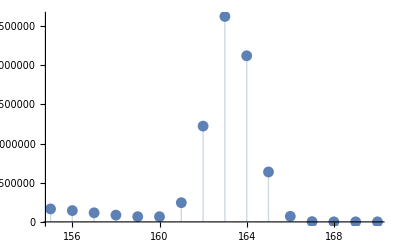

```mathematica
imported=Import["Am-241-12hr.Spe","Data"];
imported[[;;15]]//TableForm
imported[[-16;;]]//TableForm
freq=ToExpression[imported[[13;;-15]]];
sourcedata[1]=Table[{i,freq[[i]]},{i,Length[freq]}];
ListPlot[sourcedata[1][[155;;170]],PlotRange->All,Filling->Bottom]
```

## Data Analysis

## Equations

```mathematica
F[x_,mu_,sigma_,a_]:=Abs[a]*Exp[-1/2*((x-mu)/sigma)^2]
F2[x_,mu_,sigma_,a_]:=a*Exp[-1/2*((x-mu)/sigma)^2]
G[x_,mu_,sigma_,a_]:=Sum[F[x,mu[[i]],sigma[[i]],a[[i]]],{i,1,Length[mu]}]

chisq2[data_,mu_,sigma_,a_]:=Sum[(data[[i,2]]-G[data[[i,1]],mu,sigma,a])^2,{i,Length[data]}]

err[F_,w__]:={F[Map[First,List[w]]/.List->Sequence],Block[{parms=Table[Unique[],{x,1,Length[List[w]]}],values=Table[List[w][[i,1]],{i,1,Length[List[w]]}],errors=Table[List[w][[i,2]],{i,1,Length[List[w]]}]},Sqrt[Total[Table[(D[F[parms/.List->Sequence],parms[[i]]]*errors[[i]])^2,{i,1,Length[values]}]/.Table[parms[[i]]->values[[i]],{i,1,Length[values]}]]]]}
```

## Source 1-hr Trial 1

### Data Selection

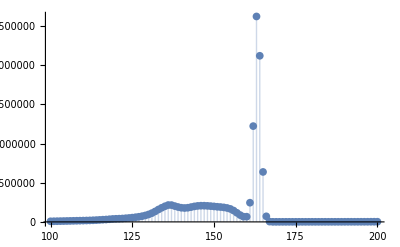

```mathematica
ListPlot[sourcedata[1][[100;;200]],Filling->Bottom,PlotRange->All]
```

### NonlinearModelFit bins

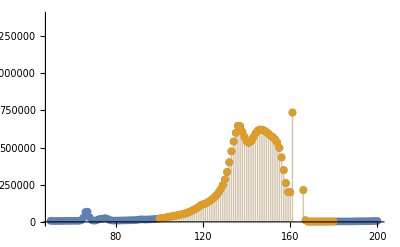

```mathematica
bkgdata=sourcedata[1][[100;;180]];
viewingdata=sourcedata[1][[50;;200]];
ListPlot[{viewingdata,bkgdata},Filling->Bottom,PlotRange->Automatic]
```

| Estimate | Standard Error | t-Statistic | P-Value
mu1 | 132.461 | 1.08348 | 122.255 | 1.63535×10^-79
mu2 | 136.362 | 0.157028 | 868.392 | 1.19948×10^-135
mu3 | 145.442 | 0.232201 | 626.361 | 2.77116×10^-126
mu4 | 153.28 | 0.353727 | 433.327 | 1.00161×10^-115
mu5 | 163.285 | 0.00105708 | 154467. | 3.73536×10^-284
sigma1 | 13.986 | 0.497555 | 28.1094 | 1.89837×10^-38
sigma2 | 3.72583 | 0.131102 | 28.4193 | 9.72259×10^-39
sigma3 | 3.38182 | 0.25291 | 13.3716 | 1.86461×10^-20
sigma4 | 4.1196 | 0.219609 | 18.7588 | 3.77167×10^-28
sigma5 | 1.0054 | 0.00118518 | 848.307 | 5.61932×10^-135
a1 | 180310. | 8848.18 | 20.3782 | 3.52873×10^-30
a2 | 449505. | 14706.5 | 30.5651 | 1.11342×10^-40
a3 | 405620. | 30143.2 | 13.4564 | 1.37175×10^-20
a4 | 468520. | 24448.3 | 19.1637 | 1.14264×10^-28
a5 | 8.14909×10^6 | 7650.16 | 1065.22 | 1.67382×10^-141

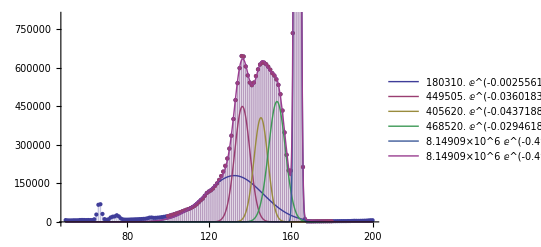

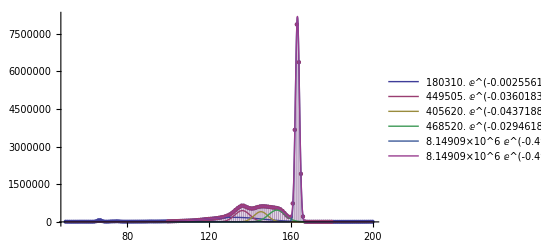

```mathematica
mu={131.6,135.3,144.6,152.5,162.3};sigma={14.2,3.6,3.6,4.0,1.0};
a={100000,200000,200000,200000,8149089};n=Length[mu];

model=NonlinearModelFit[bkgdata,G[x,Table[Symbol["mu"<>ToString[i]],{i,1,n}],Table[Symbol["sigma"<>ToString[i]],{i,1,n}],Table[Symbol["a"<>ToString[i]],{i,1,n}]],Join[Table[{Symbol["mu"<>ToString[i]],mu[[i]]},{i,1,n}],Table[{Symbol["sigma"<>ToString[i]],sigma[[i]]},{i,1,n}],Table[{Symbol["a"<>ToString[i]],a[[i]]},{i,1,n}]],x,ConfidenceLevel->0.999];
model["ParameterTable"]
params=model["BestFitParameters"];
paramerrors=model["ParameterErrors"];

theme="Classic";
Show[ListPlot[{viewingdata,bkgdata},Filling->Bottom,PlotTheme->theme,PlotRange->All],Plot[Evaluate@Join[Table[F[x,params[[i,2]],params[[i+n,2]],params[[i+2n,2]]],{i,1,n}],{G[x,params[[;;n,2]],params[[n+1;;2n,2]],params[[2n+1;;3n,2]]]}],{x,50,200},PlotRange->All,PlotTheme->theme,PlotLegends->"Expressions"],PlotRange->{Automatic,{0,800000}}]
Show[ListPlot[{viewingdata,bkgdata},Filling->Bottom,PlotTheme->theme,PlotRange->All],Plot[Evaluate@Join[Table[F[x,params[[i,2]],params[[i+n,2]],params[[i+2n,2]]],{i,1,n}],{G[x,params[[;;n,2]],params[[n+1;;2n,2]],params[[2n+1;;3n,2]]]}],{x,50,200},PlotRange->All,PlotTheme->theme,PlotLegends->"Expressions"],PlotRange->All]
```

### Conclusion

```mathematica
Table[{params[[i,2]],paramerrors[[i]],100*paramerrors[[i]]/params[[i,2]]},{i,{5,10,15}}]//TableForm
background=Table[err[F2,{i[[1]],0},{params[[5,2]],paramerrors[[5]]},{params[[10,2]],paramerrors[[10]]},{params[[15,2]],paramerrors[[15]]}],{i,bkgdata}];
counts[1]=Total[background[[All,1]]];countserror[1]=Sqrt[Total[(background[[All,2]])^2]];{counts[1],countserror[1],100countserror[1]/counts[1]}
```

163.285 | 0.00105708 | 0.000647388
1.0054 | 0.00118518 | 0.117882
8.14909×10^6 | 7650.16 | 0.0938775

{2.0537×10^7,17112.2,0.0833238}

### NonlinearModelFit+Cubic bins

```mathematica
(*bkgdata=sourcedata[1][[143;;170,{1,3}]];
viewingdata=sourcedata[1][[50;;200,{1,3}]];
ListPlot[{viewingdata,bkgdata},Filling->Bottom,PlotRange->Automatic]*)
```

```mathematica
(*model=NonlinearModelFit[bkgdata,F[x,mu1,sigma1,height]+a0+a1 x+a2 x^2+a3 x^3,{{mu1,162},{sigma1,1},{height,650000},a0,a1,a2,a3},x];
params=model["BestFitParameters"];
paramerrors=model["ParameterErrors"];
model["ParameterTable"]

theme="Classic";
Show[ListPlot[{viewingdata,bkgdata},Filling->Bottom,PlotTheme->theme,PlotRange->All],Plot[model[x],{x,50,200}],PlotRange->{Automatic,{0,60000}}]
Show[ListPlot[{viewingdata,bkgdata},Filling->Bottom,PlotTheme->theme,PlotRange->All],Plot[model[x],{x,50,200}],PlotRange->All]*)
```

```mathematica
(*Table[{params[[i,2]],paramerrors[[i]],100*paramerrors[[i]]/params[[i,2]]},{i,{1,2,3}}]//TableForm
background=Table[err[F,{i[[1]],0},{params[[1,2]],paramerrors[[1]]},{params[[2,2]],paramerrors[[2]]},{params[[3,2]],paramerrors[[3]]}],{i,bkgdata}];
testcounts[1]=Total[background[[All,1]]];testcountserror[1]=Sqrt[Total[(background[[All,2]])^2]];{testcounts[1],testcountserror[1],100testcountserror[1]/testcounts[1]}*)
```

### NonlinearModelFit

```mathematica
(*bkgdata=sourcedata[1][[100;;180,{2,3}]];
viewingdata=sourcedata[1][[50;;200,{2,3}]];
ListPlot[{viewingdata,bkgdata},Filling->Bottom,PlotRange->Automatic]*)
```

```mathematica
(*mu={47,49,53,58,60};sigma={3,0.5,1.5,1.5,0.5};
a={10000,30000,30000,35000,600000};n=Length[mu];

model=NonlinearModelFit[bkgdata,G[x,Table[Symbol["mu"<>ToString[i]],{i,1,n}],Table[Symbol["sigma"<>ToString[i]],{i,1,n}],Table[Symbol["a"<>ToString[i]],{i,1,n}]],Join[Table[{Symbol["mu"<>ToString[i]],mu[[i]]},{i,1,n}],Table[{Symbol["sigma"<>ToString[i]],sigma[[i]]},{i,1,n}],Table[{Symbol["a"<>ToString[i]],a[[i]]},{i,1,n}]],x];
model["ParameterTable"]
params=model["BestFitParameters"];
paramerrors=model["ParameterErrors"];

theme="Classic";
Show[ListPlot[{viewingdata,bkgdata},Filling->Bottom,PlotTheme->theme,PlotRange->All],Plot[Evaluate@Join[Table[F[x,params[[i,2]],params[[i+n,2]],params[[i+2n,2]]],{i,1,n}],{G[x,params[[;;n,2]],params[[n+1;;2n,2]],params[[2n+1;;3n,2]]]}],{x,30,70},PlotRange->All,PlotTheme->theme,PlotLegends->"Expressions"],PlotRange->{Automatic,{0,60000}}]
Show[ListPlot[{viewingdata,bkgdata},Filling->Bottom,PlotTheme->theme,PlotRange->All],Plot[Evaluate@Join[Table[F[x,params[[i,2]],params[[i+n,2]],params[[i+2n,2]]],{i,1,n}],{G[x,params[[;;n,2]],params[[n+1;;2n,2]],params[[2n+1;;3n,2]]]}],{x,0,80},PlotRange->All,PlotTheme->theme,PlotLegends->"Expressions"],PlotRange->All]*)
```

### NonlinearModelFit+Cubic

```mathematica
(*bkgdata=sourcedata[1][[100;;180,{2,3}]];
viewingdata=sourcedata[1][[50;;200,{2,3}]];
ListPlot[{viewingdata,bkgdata},Filling->Bottom,PlotRange->Automatic]*)
```

```mathematica
(*model=NonlinearModelFit[bkgdata,F[x,mu1,sigma1,height]+a0+a1 x+a2 x^2+a3 x^3,{{mu1,60},{sigma1,0.5},{height,650000},a0,a1,a2,a3},x];model["ParameterTable"]

theme="Classic";
Show[ListPlot[{viewingdata,bkgdata},Filling->Bottom,PlotTheme->theme,PlotRange->All],Plot[model[x],{x,0,80}],PlotRange->{Automatic,{0,60000}}]
Show[ListPlot[{viewingdata,bkgdata},Filling->Bottom,PlotTheme->theme,PlotRange->All],Plot[model[x],{x,0,80}],PlotRange->All]*)
```

### Gaussian Method

```mathematica
(*mu={47,49,53,58,60};sigma={3,0.5,1.5,1.5,0.5};
a={10000,30000,30000,30000,600000};n=Length[mu];


params=FindMinimum@@Join[{chisq2[bkgdata,Table[Symbol["mu"<>ToString[i]],{i,1,n}],Table[Symbol["sigma"<>ToString[i]],{i,1,n}],Table[Symbol["a"<>ToString[i]],{i,1,n}]]},Table[{Symbol["mu"<>ToString[i]],mu[[i]]},{i,1,n}],Table[{Symbol["sigma"<>ToString[i]],sigma[[i]]},{i,1,n}],Table[{Symbol["a"<>ToString[i]],a[[i]]},{i,1,n}]];ArrayReshape[{params[[2,All,2]]},{3,n}]//MatrixForm

(*A=Table[Join[Table[D[G[x,Table[Symbol["mu"<>ToString[i]],{i,1,n}],Table[Symbol["sigma"<>ToString[i]],{i,1,n}],Table[Symbol["a"<>ToString[i]],{i,1,n}]],j],{j,Table[Symbol["mu"<>ToString[i]],{i,1,n}]}],Table[D[G[x,Table[Symbol["mu"<>ToString[i]],{i,1,n}],Table[Symbol["sigma"<>ToString[i]],{i,1,n}],Table[Symbol["a"<>ToString[i]],{i,1,n}]],j],{j,Table[Symbol["sigma"<>ToString[i]],{i,1,n}]}],Table[D[G[x,Table[Symbol["mu"<>ToString[i]],{i,1,n}],Table[Symbol["sigma"<>ToString[i]],{i,1,n}],
Table[Symbol["a"<>ToString[i]],{i,1,n}]],j]/.Abs'[j]->1,{j,Table[Symbol["a"<>ToString[i]],{i,1,n}]}]]/.params[[2]]/.x->i[[1]],{i,bkgdata}];
b=Transpose[{Table[i[[2]]-G[i[[1]],params[[2,;;n,2]],params[[2,n+1;;2n,2]],params[[2,2n+1;;3n,2]]],{i,bkgdata}]}];
alpha=Transpose[A].A;
beta=Transpose[A].b;
paramerrors=Inverse[alpha].beta;ArrayReshape[paramerrors,{3,n}]//MatrixForm*)

theme="Classic";
Show[ListPlot[{viewingdata,bkgdata},Filling->Bottom,PlotTheme->theme,PlotRange->All],Plot[Evaluate@Join[Table[F[x,params[[2,i,2]],params[[2,i+n,2]],params[[2,i+2n,2]]],{i,1,n}],{G[x,params[[2,;;n,2]],params[[2,n+1;;2n,2]],params[[2,2n+1;;3n,2]]]}],{x,30,70},PlotRange->All,PlotTheme->theme,PlotLegends->"Expressions"],PlotRange->{Automatic,{0,60000}}]
Show[ListPlot[{viewingdata,bkgdata},Filling->Bottom,PlotTheme->theme,PlotRange->All],Plot[Evaluate@Join[Table[F[x,params[[2,i,2]],params[[2,i+n,2]],params[[2,i+2n,2]]],{i,1,n}],{G[x,params[[2,;;n,2]],params[[2,n+1;;2n,2]],params[[2,2n+1;;3n,2]]]}],{x,0,80},PlotRange->All,PlotTheme->theme,PlotLegends->"Expressions"],PlotRange->All]*)
```

### Estimated Background Method

```mathematica
(*estbkgdata=Join[Transpose[{viewingdata[[All,1]]}],Transpose[{EstimatedBackground[viewingdata[[All,2]]]}],2];
basedata=Join[Transpose[{viewingdata[[All,1]]}],Transpose[{viewingdata[[All,2]]-EstimatedBackground[viewingdata[[All,2]]]}],2];
ListLinePlot[{viewingdata,estbkgdata,basedata},PlotRange->All]*)
```

```mathematica
(*model=NonlinearModelFit[basedata,F[x,mu1,sigma1,height],{{mu1,60},{sigma1,0.5},{height,650000}},x];model["ParameterTable"]

theme="Classic";
Show[ListPlot[{viewingdata,basedata},Filling->Bottom,PlotTheme->theme,PlotRange->All],Plot[model[x],{x,0,80},PlotTheme->theme,PlotRange->All],PlotRange->{Automatic,{0,60000}}]
Show[ListPlot[{viewingdata,basedata},Filling->Bottom,PlotTheme->theme,PlotRange->All],Plot[model[x],{x,0,80},PlotTheme->theme,PlotRange->All],PlotRange->All]*)
```

### Conclusion (Old)

```mathematica
(*peaks[1]=params[[-1,2]]
peakerror[1]=paramerrors[[-1]]
counts[1]=NIntegrate[F[x,params[[5,2]],params[[5+5,2]],params[[5+2*5,2]]],{x,params[[5,2]]-10params[[5+5,2]],params[[5,2]]+10params[[5+5,2]]}]*)
```

# Data Set 1 (Excel)

```mathematica
ClearAll["Global`*"]
(*~ MacOS ~*)
main="/Users/mikhailgaerlan/Box Sync/Education/MSU/Research/Radiation Thickness/Data";

SetDirectory[main];
$Line=0;
```

## Data Import

## Thick Film

Channel | Energy | Counts
0. | 0.137869 | 0.
1. | 0.5045 | 0.
2. | 0.871131 | 0.
3. | 1.23776 | 0.
4. | 1.60439 | 1948.
5. | 1.97102 | 2046.
6. | 2.33766 | 1183.
7. | 2.70429 | 838.
8. | 3.07092 | 743.

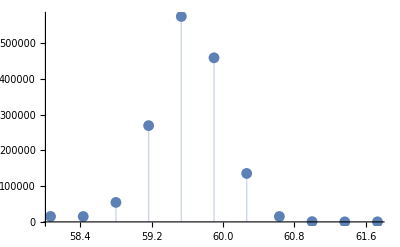

```mathematica
thickdata[1]=Import["Am-241-ThickFilm-1Hr.xlsx",{"Data",1}];
thickdata[1][[1;;10]]//TableForm
ListPlot[thickdata[1][[160;;170,{2,3}]],PlotRange->All,Filling->Bottom]
```

## Thin Film

Channel | Energy | Counts
0. | 0.137869 | 0.
1. | 0.5045 | 0.
2. | 0.871131 | 0.
3. | 1.23776 | 0.
4. | 1.60439 | 1821.
5. | 1.97102 | 2191.
6. | 2.33766 | 1173.
7. | 2.70429 | 887.
8. | 3.07092 | 772.

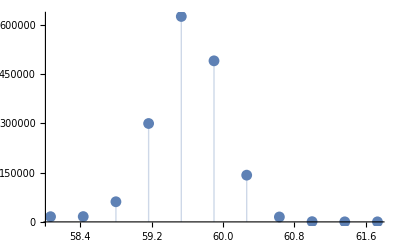

```mathematica
thindata[1]=Import["Am-241-ThinFilm-1Hr.xlsx",{"Data",1}];
thindata[1][[1;;10]]//TableForm
ListPlot[thindata[1][[160;;170,{2,3}]],PlotRange->All,Filling->Bottom]
```

## Data Analysis

## Equations

```mathematica
F[x_,mu_,sigma_,a_]:=a*Exp[-1/2*((x-mu)/sigma)^2]
G[x_,mu_,sigma_,a_]:=Sum[F[x,mu[[i]],sigma[[i]],a[[i]]],{i,1,Length[mu]}]

chisq2[data_,mu_,sigma_,a_]:=Sum[(data[[i,2]]-G[data[[i,1]],mu,sigma,a])^2,{i,Length[data]}]

err[F_,w__]:={F[Map[First,List[w]]/.List->Sequence],Block[{parms=Table[Unique[],{x,1,Length[List[w]]}],values=Table[List[w][[i,1]],{i,1,Length[List[w]]}],errors=Table[List[w][[i,2]],{i,1,Length[List[w]]}]},Sqrt[Total[Table[(D[F[parms/.List->Sequence],parms[[i]]]*errors[[i]])^2,{i,1,Length[values]}]/.Table[parms[[i]]->values[[i]],{i,1,Length[values]}]]]]}
```

## Source 1-hr Trial 1

### Data Selection

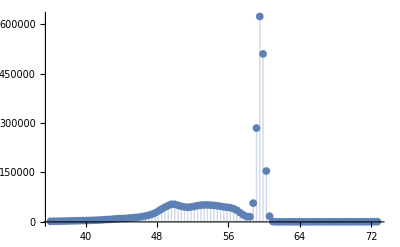

```mathematica
ListPlot[sourcedata[1][[100;;200,{2,3}]],Filling->Bottom,PlotRange->All]
```

### NonlinearModelFit bins

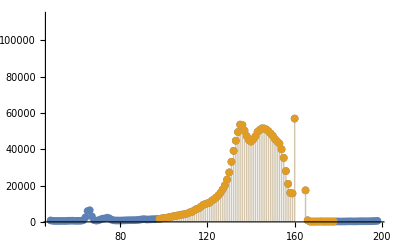

```mathematica
bkgdata=sourcedata[1][[100;;180,{1,3}]];
viewingdata=sourcedata[1][[50;;200,{1,3}]];
ListPlot[{viewingdata,bkgdata},Filling->Bottom,PlotRange->Automatic]
```

| Estimate | Standard Error | t-Statistic | P-Value
mu1 | 131.648 | 1.09767 | 119.934 | 5.76352×10^-79
mu2 | 135.277 | 0.186003 | 727.281 | 1.44993×10^-130
mu3 | 144.587 | 0.317564 | 455.302 | 3.83033×10^-117
mu4 | 152.542 | 0.481389 | 316.88 | 9.27107×10^-107
mu5 | 162.298 | 0.00120771 | 134385. | 3.66668×10^-280
sigma1 | 14.1615 | 0.506593 | 27.9544 | 2.65974×10^-38
sigma2 | 3.6388 | 0.142959 | 25.4535 | 7.69558×10^-36
sigma3 | 3.59898 | 0.344186 | 10.4565 | 1.21976×10^-15
sigma4 | 4.00913 | 0.270497 | 14.8213 | 1.1143×10^-22
sigma5 | 1.00182 | 0.00135448 | 739.633 | 4.77176×10^-131
a1 | 14976.5 | 756.24 | 19.8039 | 1.79279×10^-29
a2 | 36802.4 | 1378.93 | 26.6892 | 4.4262×10^-37
a3 | 35562.4 | 2828.05 | 12.5749 | 3.48568×10^-19
a4 | 35923.9 | 2762.17 | 13.0057 | 7.08455×10^-20
a5 | 647764. | 696.511 | 930.012 | 1.30058×10^-137

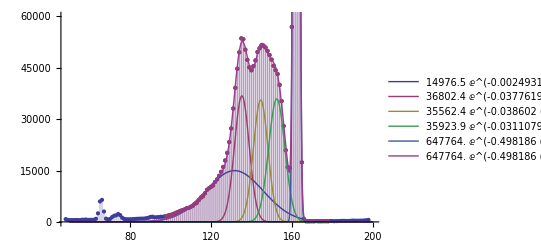

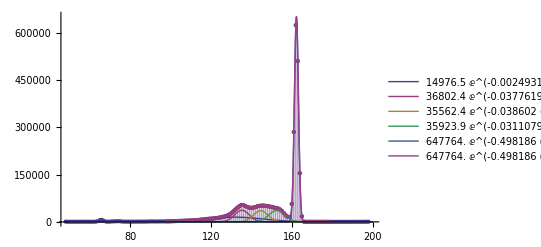

```mathematica
mu={131,134,146,154,162};sigma={10,5,5,5,1};
a={10000,30000,30000,35000,600000};n=Length[mu];

model=NonlinearModelFit[bkgdata,G[x,Table[Symbol["mu"<>ToString[i]],{i,1,n}],Table[Symbol["sigma"<>ToString[i]],{i,1,n}],Table[Symbol["a"<>ToString[i]],{i,1,n}]],Join[Table[{Symbol["mu"<>ToString[i]],mu[[i]]},{i,1,n}],Table[{Symbol["sigma"<>ToString[i]],sigma[[i]]},{i,1,n}],Table[{Symbol["a"<>ToString[i]],a[[i]]},{i,1,n}]],x];
model["ParameterTable"]
params=model["BestFitParameters"];
paramerrors=model["ParameterErrors"];

theme="Classic";
Show[ListPlot[{viewingdata,bkgdata},Filling->Bottom,PlotTheme->theme,PlotRange->All],Plot[Evaluate@Join[Table[F[x,params[[i,2]],params[[i+n,2]],params[[i+2n,2]]],{i,1,n}],{G[x,params[[;;n,2]],params[[n+1;;2n,2]],params[[2n+1;;3n,2]]]}],{x,50,200},PlotRange->All,PlotTheme->theme,PlotLegends->"Expressions"],PlotRange->{Automatic,{0,60000}}]
Show[ListPlot[{viewingdata,bkgdata},Filling->Bottom,PlotTheme->theme,PlotRange->All],Plot[Evaluate@Join[Table[F[x,params[[i,2]],params[[i+n,2]],params[[i+2n,2]]],{i,1,n}],{G[x,params[[;;n,2]],params[[n+1;;2n,2]],params[[2n+1;;3n,2]]]}],{x,50,200},PlotRange->All,PlotTheme->theme,PlotLegends->"Expressions"],PlotRange->All]
```

### Conclusion

```mathematica
Table[{params[[i,2]],paramerrors[[i]],100*paramerrors[[i]]/params[[i,2]]},{i,{5,10,15}}]//TableForm
background=Table[err[F,{i[[1]],0},{params[[5,2]],paramerrors[[5]]},{params[[10,2]],paramerrors[[10]]},{params[[15,2]],paramerrors[[15]]}],{i,bkgdata}];
counts[1]=Total[background[[All,1]]];countserror[1]=Sqrt[Total[(background[[All,2]])^2]];{counts[1],countserror[1],100countserror[1]/counts[1]}
```

162.298 | 0.00120771 | 0.000744129
1.00182 | 0.00135448 | 0.135202
647764. | 696.511 | 0.107525

{1.62666×10^6,1556.2,0.0956687}

## Source 1-hr Trial 2

### Data Selection

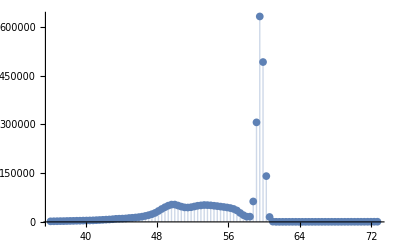

```mathematica
ListPlot[sourcedata[2][[100;;200,{2,3}]],Filling->Bottom,PlotRange->All]
```

### NonlinearModelFit bins

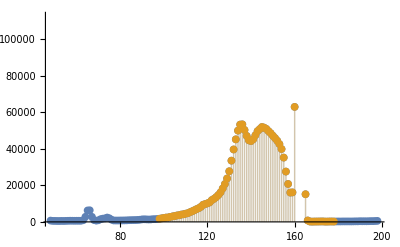

```mathematica
bkgdata=sourcedata[2][[100;;180,{1,3}]];
viewingdata=sourcedata[2][[50;;200,{1,3}]];
ListPlot[{viewingdata,bkgdata},Filling->Bottom,PlotRange->Automatic]
```

| Estimate | Standard Error | t-Statistic | P-Value
mu1 | 131.346 | 1.18555 | 110.79 | 1.05386×10^-76
mu2 | 135.278 | 0.17551 | 770.772 | 3.13903×10^-132
mu3 | 144.517 | 0.277669 | 520.463 | 5.627×10^-121
mu4 | 152.393 | 0.434917 | 350.395 | 1.22196×10^-109
mu5 | 162.244 | 0.00121599 | 133426. | 5.88371×10^-280
sigma1 | 14.0481 | 0.545351 | 25.7598 | 3.75228×10^-36
sigma2 | 3.70767 | 0.143513 | 25.8351 | 3.14837×10^-36
sigma3 | 3.47213 | 0.296381 | 11.7151 | 8.97902×10^-18
sigma4 | 4.05584 | 0.259017 | 15.6586 | 6.54024×10^-24
sigma5 | 1.00424 | 0.00135936 | 738.759 | 5.15923×10^-131
a1 | 14844.2 | 790.158 | 18.7863 | 3.47529×10^-28
a2 | 37221.4 | 1351.26 | 27.5458 | 6.51738×10^-38
a3 | 35196.7 | 2777.3 | 12.673 | 2.41958×10^-19
a4 | 36811.8 | 2442.48 | 15.0715 | 4.73245×10^-23
a5 | 648228. | 700.083 | 925.929 | 1.7388×10^-137

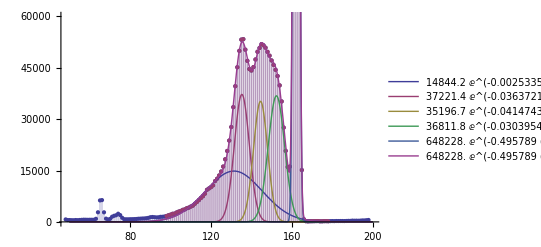

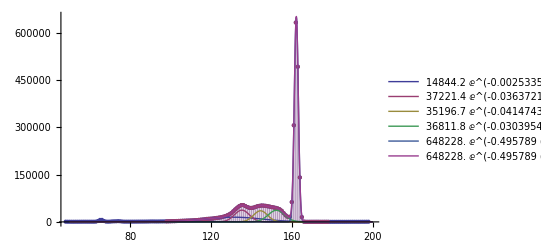

```mathematica
mu={131,134,146,154,162};sigma={10,5,5,5,1};
a={10000,30000,30000,35000,600000};n=Length[mu];

model=NonlinearModelFit[bkgdata,G[x,Table[Symbol["mu"<>ToString[i]],{i,1,n}],Table[Symbol["sigma"<>ToString[i]],{i,1,n}],Table[Symbol["a"<>ToString[i]],{i,1,n}]],Join[Table[{Symbol["mu"<>ToString[i]],mu[[i]]},{i,1,n}],Table[{Symbol["sigma"<>ToString[i]],sigma[[i]]},{i,1,n}],Table[{Symbol["a"<>ToString[i]],a[[i]]},{i,1,n}]],x];
model["ParameterTable"]
params=model["BestFitParameters"];
paramerrors=model["ParameterErrors"];

theme="Classic";
Show[ListPlot[{viewingdata,bkgdata},Filling->Bottom,PlotTheme->theme,PlotRange->All],Plot[Evaluate@Join[Table[F[x,params[[i,2]],params[[i+n,2]],params[[i+2n,2]]],{i,1,n}],{G[x,params[[;;n,2]],params[[n+1;;2n,2]],params[[2n+1;;3n,2]]]}],{x,50,200},PlotRange->All,PlotTheme->theme,PlotLegends->"Expressions"],PlotRange->{Automatic,{0,60000}}]
Show[ListPlot[{viewingdata,bkgdata},Filling->Bottom,PlotTheme->theme,PlotRange->All],Plot[Evaluate@Join[Table[F[x,params[[i,2]],params[[i+n,2]],params[[i+2n,2]]],{i,1,n}],{G[x,params[[;;n,2]],params[[n+1;;2n,2]],params[[2n+1;;3n,2]]]}],{x,50,200},PlotRange->All,PlotTheme->theme,PlotLegends->"Expressions"],PlotRange->All]
```

### Conclusion

```mathematica
Table[{params[[i,2]],paramerrors[[i]],100*paramerrors[[i]]/params[[i,2]]},{i,{5,10,15}}]//TableForm
background=Table[err[F,{i[[1]],0},{params[[5,2]],paramerrors[[5]]},{params[[10,2]],paramerrors[[10]]},{params[[15,2]],paramerrors[[15]]}],{i,bkgdata}];
counts[2]=Total[background[[All,1]]];countserror[2]=Sqrt[Total[(background[[All,2]])^2]];{counts[2],countserror[2],100countserror[2]/counts[2]}
```

162.244 | 0.00121599 | 0.00074948
1.00424 | 0.00135936 | 0.135362
648228. | 700.083 | 0.108

{1.63175×10^6,1564.87,0.0959013}

## Thick Film

### Data Selection

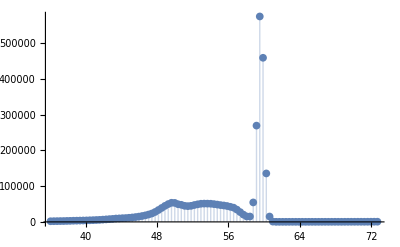

```mathematica
ListPlot[thickdata[1][[100;;200,{2,3}]],Filling->Bottom,PlotRange->All]
```

### NonlinearModelFit bins

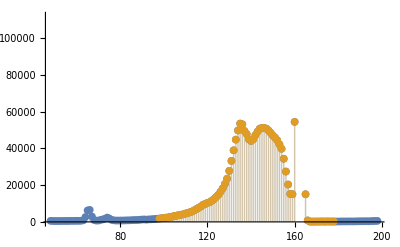

```mathematica
bkgdata=thickdata[1][[100;;180,{1,3}]];
viewingdata=thickdata[1][[50;;200,{1,3}]];
ListPlot[{viewingdata,bkgdata},Filling->Bottom,PlotRange->Automatic]
```

| Estimate | Standard Error | t-Statistic | P-Value
mu1 | 131.595 | 1.06922 | 123.076 | 1.05349×10^-79
mu2 | 135.304 | 0.179973 | 751.802 | 1.62554×10^-131
mu3 | 144.607 | 0.2985 | 484.444 | 6.38852×10^-119
mu4 | 152.442 | 0.447829 | 340.403 | 8.2395×10^-109
mu5 | 162.274 | 0.00128237 | 126542. | 1.94111×10^-278
sigma1 | 14.1571 | 0.491717 | 28.7912 | 4.39093×10^-39
sigma2 | 3.70407 | 0.141957 | 26.0929 | 1.73168×10^-36
sigma3 | 3.53552 | 0.319485 | 11.0663 | 1.10467×10^-16
sigma4 | 3.96019 | 0.253177 | 15.642 | 6.91362×10^-24
sigma5 | 1.00212 | 0.00143296 | 699.341 | 1.92354×10^-129
a1 | 14985.7 | 745.056 | 20.1135 | 7.43297×10^-30
a2 | 36749.7 | 1306.75 | 28.1231 | 1.84306×10^-38
a3 | 35125.7 | 2715.68 | 12.9344 | 9.20695×10^-20
a4 | 35991.9 | 2601.19 | 13.8367 | 3.5035×10^-21
a5 | 593021. | 676.217 | 876.969 | 6.27054×10^-136

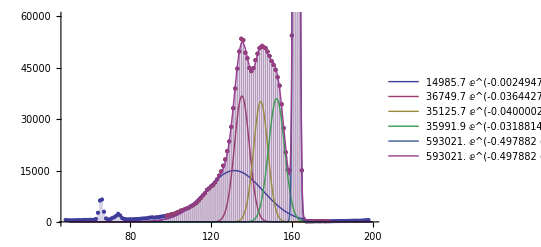

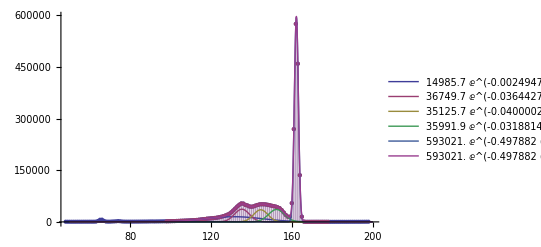

```mathematica
mu={131,134,146,154,162};sigma={10,5,5,5,1};
a={10000,30000,30000,35000,600000};n=Length[mu];

model=NonlinearModelFit[bkgdata,G[x,Table[Symbol["mu"<>ToString[i]],{i,1,n}],Table[Symbol["sigma"<>ToString[i]],{i,1,n}],Table[Symbol["a"<>ToString[i]],{i,1,n}]],Join[Table[{Symbol["mu"<>ToString[i]],mu[[i]]},{i,1,n}],Table[{Symbol["sigma"<>ToString[i]],sigma[[i]]},{i,1,n}],Table[{Symbol["a"<>ToString[i]],a[[i]]},{i,1,n}]],x];
model["ParameterTable"]
params=model["BestFitParameters"];
paramerrors=model["ParameterErrors"];

theme="Classic";
Show[ListPlot[{viewingdata,bkgdata},Filling->Bottom,PlotTheme->theme,PlotRange->All],Plot[Evaluate@Join[Table[F[x,params[[i,2]],params[[i+n,2]],params[[i+2n,2]]],{i,1,n}],{G[x,params[[;;n,2]],params[[n+1;;2n,2]],params[[2n+1;;3n,2]]]}],{x,50,200},PlotRange->All,PlotTheme->theme,PlotLegends->"Expressions"],PlotRange->{Automatic,{0,60000}}]
Show[ListPlot[{viewingdata,bkgdata},Filling->Bottom,PlotTheme->theme,PlotRange->All],Plot[Evaluate@Join[Table[F[x,params[[i,2]],params[[i+n,2]],params[[i+2n,2]]],{i,1,n}],{G[x,params[[;;n,2]],params[[n+1;;2n,2]],params[[2n+1;;3n,2]]]}],{x,50,200},PlotRange->All,PlotTheme->theme,PlotLegends->"Expressions"],PlotRange->All]
```

### Conclusion

```mathematica
Table[{params[[i,2]],paramerrors[[i]],100*paramerrors[[i]]/params[[i,2]]},{i,{5,10,15}}]//TableForm
background=Table[err[F,{i[[1]],0},{params[[5,2]],paramerrors[[5]]},{params[[10,2]],paramerrors[[10]]},{params[[15,2]],paramerrors[[15]]}],{i,bkgdata}];
counts[3]=Total[background[[All,1]]];countserror[3]=Sqrt[Total[(background[[All,2]])^2]];{counts[3],countserror[3],100countserror[3]/counts[3]}
```

162.274 | 0.00128237 | 0.000790253
1.00212 | 0.00143296 | 0.142992
593021. | 676.217 | 0.114029

{1.48964×10^6,1510.09,0.101373}

## Thin Film

### Data Selection

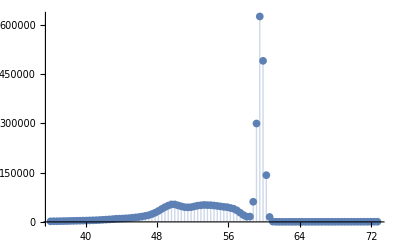

```mathematica
ListPlot[thindata[1][[100;;200,{2,3}]],Filling->Bottom,PlotRange->All]
```

### NonlinearModelFit bins

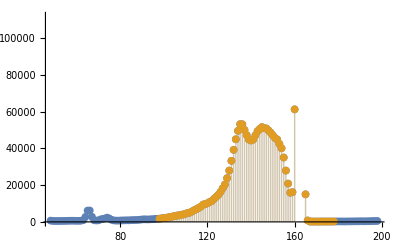

```mathematica
bkgdata=thindata[1][[100;;180,{1,3}]];
viewingdata=thindata[1][[50;;200,{1,3}]];
ListPlot[{viewingdata,bkgdata},Filling->Bottom,PlotRange->Automatic]
```

| Estimate | Standard Error | t-Statistic | P-Value
mu1 | 131.329 | 1.17665 | 111.613 | 6.48329×10^-77
mu2 | 135.327 | 0.177143 | 763.941 | 5.64825×10^-132
mu3 | 144.559 | 0.278944 | 518.237 | 7.46697×10^-121
mu4 | 152.403 | 0.433552 | 351.523 | 9.88611×10^-110
mu5 | 162.254 | 0.00119145 | 136182. | 1.52601×10^-280
sigma1 | 14.0017 | 0.538677 | 25.9927 | 2.18315×10^-36
sigma2 | 3.74631 | 0.143973 | 26.021 | 2.04459×10^-36
sigma3 | 3.47509 | 0.296396 | 11.7245 | 8.66044×10^-18
sigma4 | 4.0646 | 0.256215 | 15.864 | 3.30608×10^-24
sigma5 | 1.00358 | 0.00133381 | 752.42 | 1.53968×10^-131
a1 | 14810.3 | 783.876 | 18.8937 | 2.52862×10^-28
a2 | 37115.8 | 1352.65 | 27.4394 | 8.24537×10^-38
a3 | 34735. | 2820.05 | 12.3172 | 9.14182×10^-19
a4 | 36911.6 | 2449.13 | 15.0713 | 4.73507×10^-23
a5 | 642189. | 680.448 | 943.773 | 4.93352×10^-138

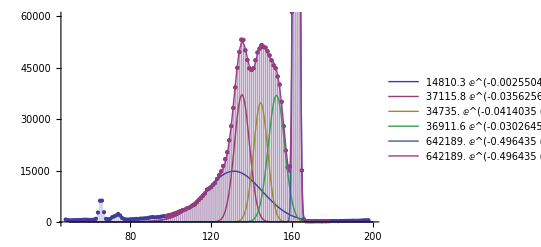

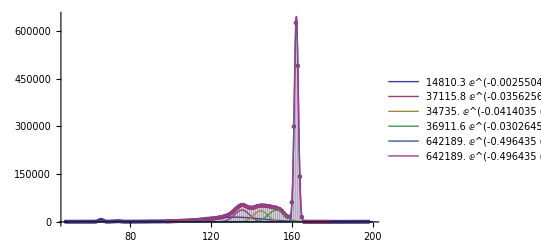

```mathematica
mu={131,134,146,154,162};sigma={10,5,5,5,1};
a={10000,30000,30000,35000,600000};n=Length[mu];

model=NonlinearModelFit[bkgdata,G[x,Table[Symbol["mu"<>ToString[i]],{i,1,n}],Table[Symbol["sigma"<>ToString[i]],{i,1,n}],Table[Symbol["a"<>ToString[i]],{i,1,n}]],Join[Table[{Symbol["mu"<>ToString[i]],mu[[i]]},{i,1,n}],Table[{Symbol["sigma"<>ToString[i]],sigma[[i]]},{i,1,n}],Table[{Symbol["a"<>ToString[i]],a[[i]]},{i,1,n}]],x];
model["ParameterTable"]
params=model["BestFitParameters"];
paramerrors=model["ParameterErrors"];

theme="Classic";
Show[ListPlot[{viewingdata,bkgdata},Filling->Bottom,PlotTheme->theme,PlotRange->All],Plot[Evaluate@Join[Table[F[x,params[[i,2]],params[[i+n,2]],params[[i+2n,2]]],{i,1,n}],{G[x,params[[;;n,2]],params[[n+1;;2n,2]],params[[2n+1;;3n,2]]]}],{x,50,200},PlotRange->All,PlotTheme->theme,PlotLegends->"Expressions"],PlotRange->{Automatic,{0,60000}}]
Show[ListPlot[{viewingdata,bkgdata},Filling->Bottom,PlotTheme->theme,PlotRange->All],Plot[Evaluate@Join[Table[F[x,params[[i,2]],params[[i+n,2]],params[[i+2n,2]]],{i,1,n}],{G[x,params[[;;n,2]],params[[n+1;;2n,2]],params[[2n+1;;3n,2]]]}],{x,50,200},PlotRange->All,PlotTheme->theme,PlotLegends->"Expressions"],PlotRange->All]
```

### Conclusion

```mathematica
Table[{params[[i,2]],paramerrors[[i]],100*paramerrors[[i]]/params[[i,2]]},{i,{5,10,15}}]//TableForm
background=Table[err[F,{i[[1]],0},{params[[5,2]],paramerrors[[5]]},{params[[10,2]],paramerrors[[10]]},{params[[15,2]],paramerrors[[15]]}],{i,bkgdata}];
counts[4]=Total[background[[All,1]]];countserror[4]=Sqrt[Total[(background[[All,2]])^2]];{counts[4],countserror[4],100countserror[4]/counts[4]}
```

162.254 | 0.00119145 | 0.000734311
1.00358 | 0.00133381 | 0.132904
642189. | 680.448 | 0.105958

{1.6155×10^6,1520.6,0.0941258}

## Calculations

```mathematica
thickness=40;thicknesserror=0.01;
Print["Peak Data\n",Table[{counts[i],countserror[i],100*countserror[i]/counts[i]},{i,1,4}]//TableForm,"\n"]
coeff[counts1_,counts3_,thickness_]:=(-Log[counts3/counts1])/thickness;


attencoeff=err[coeff,{counts[1],countserror[1]},{counts[3],countserror[3]},{thickness,thicknesserror}];
thinmeasure=err[coeff,{counts[1],countserror[1]},{counts[4],countserror[4]},attencoeff];Join[thinmeasure,{100*thinmeasure[[2]]/thinmeasure[[1]]}]

attencoeff=err[coeff,{counts[2],countserror[2]},{counts[3],countserror[3]},{thickness,thicknesserror}];
thinmeasure=err[coeff,{counts[2],countserror[2]},{counts[4],countserror[4]},attencoeff];Join[thinmeasure,{100*thinmeasure[[2]]/thinmeasure[[1]]}]
```

Peak Data
1.62666×10^6 | 1556.2 | 0.0956687
1.63175×10^6 | 1564.87 | 0.0959013
1.48964×10^6 | 1510.09 | 0.101373
1.6155×10^6 | 1520.6 | 0.0941258

{3.12887,0.612119,19.5636}

{4.39451,0.593722,13.5106}

```mathematica
attencoeff=err[coeff,{counts[1],countserror[1]},{counts[3],countserror[3]},{thickness,thicknesserror}];
thinmeasure=err[coeff,{counts[1],countserror[1]},{counts[4],countserror[4]},attencoeff];Join[thinmeasure,{100*thinmeasure[[2]]/thinmeasure[[1]]}]
```

{3.12887,0.612119,19.5636}

## Calculations (Old)

```mathematica
(*thickness=40;thicknesserror=0.01;
Print["Peak Data\n",Table[{peaks[i],peakerror[i],100*peakerror[i]/peaks[i]},{i,1,4}]//TableForm,"\n"]
coeff[counts1_,counts3_,thickness_]:=(-Log[counts3/counts1])/thickness;


attencoeff=err[coeff,{peaks[1],peakerror[1]},{peaks[3],peakerror[3]},{thickness,thicknesserror}];
thinmeasure=err[coeff,{peaks[1],peakerror[2]},{peaks[4],peakerror[4]},attencoeff];Join[thinmeasure,{100*thinmeasure[[2]]/thinmeasure[[1]]}]


theorerror=35;100*theorerror/peaks[1]
attencoeff=err[coeff,{peaks[1],theorerror},{peaks[3],theorerror},{thickness,thicknesserror}];
thinmeasure=err[coeff,{peaks[1],theorerror},{peaks[4],theorerror},attencoeff];Join[thinmeasure,{100*thinmeasure[[2]]/thinmeasure[[1]]}]

const=(-Log[counts[3]/counts[1]])/thickness;
(-Log[counts[4]/counts[1]])/const*)
```

# Data Set 1 (Alt)

```mathematica
ClearAll["Global`*"]
(*~ MacOS ~*)
main="/Users/mikhailgaerlan/Box Sync/Education/MSU/Research/Radiation Thickness/Data";

SetDirectory[main];
$Line=0;
```

## Data Import

## Source 1-Hour

### Trial 1

$SPEC_ID:
Molnar Range
$SPEC_REM:
DET# 1
DETDESC# HPGe Detector 1
AP# GammaVision Version 6.07
$DATE_MEA:
10/19/2015 09:56:53
$MEAS_TIM:
3600 3733
$DATA:
0 8191
       0
       0
       0

0
       0
$ROI:
0
$PRESETS:
Live Time
3600
0
$ENER_FIT:
0.137869 0.366631
$MCA_CAL:
3
1.378689E-001 3.666307E-001 -4.415950E-008 keV
$SHAPE_CAL:
3
2.301834E+000 9.195991E-004 -5.357180E-008

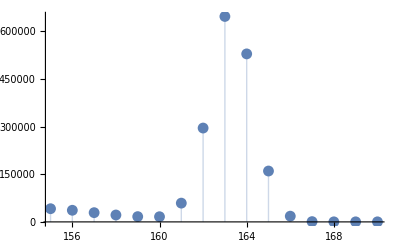

```mathematica
imported=Import["Am-241-1hr-10192015.Spe","Data"];
times=ToExpression[StringSplit[imported[[10]]]];
deadtime=N[Abs[times[[1]]-times[[2]]]/times[[2]]];
imported[[;;15]]//TableForm
imported[[-16;;]]//TableForm
freq=ToExpression[imported[[13;;-15]]]/(1-deadtime);
sourcedata[1]=Table[{i,freq[[i]]},{i,Length[freq]}];
ListPlot[sourcedata[1][[155;;170]],PlotRange->All,Filling->Bottom]
```

### Trial 2

$SPEC_ID:
Molnar Range
$SPEC_REM:
DET# 1
DETDESC# HPGe Detector 1
AP# GammaVision Version 6.07
$DATE_MEA:
10/19/2015 14:15:00
$MEAS_TIM:
3600 3732
$DATA:
0 8191
       0
       0
       0

0
       0
$ROI:
0
$PRESETS:
Live Time
3600
0
$ENER_FIT:
0.137869 0.366631
$MCA_CAL:
3
1.378689E-001 3.666307E-001 -4.415950E-008 keV
$SHAPE_CAL:
3
2.301834E+000 9.195991E-004 -5.357180E-008

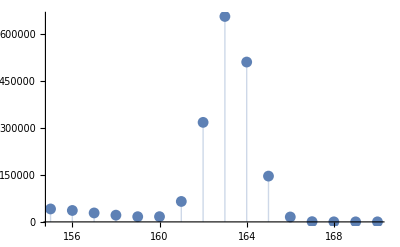

```mathematica
imported=Import["Am-241-1hrTrial2-10192015.Spe","Data"];
times=ToExpression[StringSplit[imported[[10]]]];
deadtime=N[Abs[times[[1]]-times[[2]]]/times[[2]]];
imported[[;;15]]//TableForm
imported[[-16;;]]//TableForm
freq=ToExpression[imported[[13;;-15]]]/(1-deadtime);
sourcedata[2]=Table[{i,freq[[i]]},{i,Length[freq]}];
ListPlot[sourcedata[2][[155;;170]],PlotRange->All,Filling->Bottom]
```

## Thick Film

$SPEC_ID:
Molnar Range
$SPEC_REM:
DET# 1
DETDESC# HPGe Detector 1
AP# GammaVision Version 6.07
$DATE_MEA:
10/19/2015 11:10:33
$MEAS_TIM:
3600 3727
$DATA:
0 8191
       0
       0
       0

0
       0
$ROI:
0
$PRESETS:
Live Time
3600
0
$ENER_FIT:
0.137869 0.366631
$MCA_CAL:
3
1.378689E-001 3.666307E-001 -4.415950E-008 keV
$SHAPE_CAL:
3
2.301834E+000 9.195991E-004 -5.357180E-008

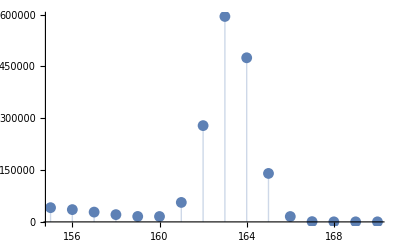

```mathematica
imported=Import["Am-241-ThickFilm-1hr-10192015.Spe","Data"];
times=ToExpression[StringSplit[imported[[10]]]];
deadtime=N[Abs[times[[1]]-times[[2]]]/times[[2]]];
imported[[;;15]]//TableForm
imported[[-16;;]]//TableForm
freq=ToExpression[imported[[13;;-15]]]/(1-deadtime);
thickdata[1]=Table[{i,freq[[i]]},{i,Length[freq]}];
ListPlot[thickdata[1][[155;;170]],PlotRange->All,Filling->Bottom]
```

## Thin Film

$SPEC_ID:
Molnar Range
$SPEC_REM:
DET# 1
DETDESC# HPGe Detector 1
AP# GammaVision Version 6.07
$DATE_MEA:
10/19/2015 13:11:13
$MEAS_TIM:
3600 3732
$DATA:
0 8191
       0
       0
       0

0
       1
$ROI:
0
$PRESETS:
Live Time
3600
0
$ENER_FIT:
0.137869 0.366631
$MCA_CAL:
3
1.378689E-001 3.666307E-001 -4.415950E-008 keV
$SHAPE_CAL:
3
2.301834E+000 9.195991E-004 -5.357180E-008

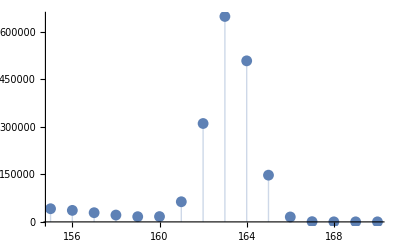

```mathematica
imported=Import["Am-241-ThinFilm-1hr-10192015.Spe","Data"];
times=ToExpression[StringSplit[imported[[10]]]];
deadtime=N[Abs[times[[1]]-times[[2]]]/times[[2]]];
imported[[;;15]]//TableForm
imported[[-16;;]]//TableForm
freq=ToExpression[imported[[13;;-15]]]/(1-deadtime);
thindata[1]=Table[{i,freq[[i]]},{i,Length[freq]}];
ListPlot[thindata[1][[155;;170]],PlotRange->All,Filling->Bottom]
```

## Data Analysis

## Equations

```mathematica
F[x_,mu_,sigma_,a_]:=Abs[a]*Exp[-1/2*((x-mu)/sigma)^2]
F2[x_,mu_,sigma_,a_]:=a*Exp[-1/2*((x-mu)/sigma)^2]
G[x_,mu_,sigma_,a_]:=Sum[F[x,mu[[i]],sigma[[i]],a[[i]]],{i,1,Length[mu]}]

chisq2[data_,mu_,sigma_,a_]:=Sum[(data[[i,2]]-G[data[[i,1]],mu,sigma,a])^2,{i,Length[data]}]
backgroundfunction[x_,mu1_,mu2_,mu3_,mu4_,sigma1_,sigma2_,sigma3_,sigma4_,a1_,a2_,a3_,a4_]:=F2[x,mu1,sigma1,a1]+F2[x,mu2,sigma2,a2]+F2[x,mu3,sigma3,a3]+F2[x,mu4,sigma4,a4];
fwhm[sigma_]:=2*sigma*Sqrt[2*Log[2]];

err[F_,w__]:={F[Map[First,List[w]]/.List->Sequence],Block[{parms=Table[Unique[],{x,1,Length[List[w]]}],values=Table[List[w][[i,1]],{i,1,Length[List[w]]}],errors=Table[List[w][[i,2]],{i,1,Length[List[w]]}]},Sqrt[Total[Table[(D[F[parms/.List->Sequence],parms[[i]]]*errors[[i]])^2,{i,1,Length[values]}]/.Table[parms[[i]]->values[[i]],{i,1,Length[values]}]]]]}
```

## Source 1-hr Trial 1

### Data Selection

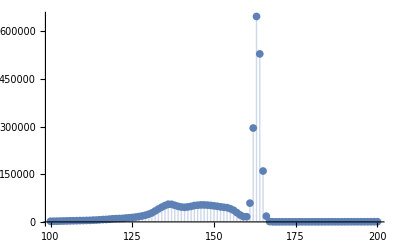

```mathematica
ListPlot[sourcedata[1][[100;;200]],Filling->Bottom,PlotRange->All]
```

### NonlinearModelFit bins

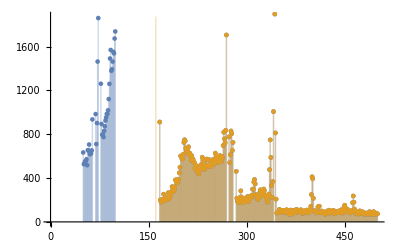

```mathematica
bkgdata=Table[{sourcedata[1][[i,1]],sourcedata[1][[i,2]]},{i,161,500}];
viewingdata=sourcedata[1][[50;;500]];
ListPlot[{viewingdata,bkgdata},Filling->Bottom,PlotRange->Automatic]
```

| Estimate | Standard Error | t-Statistic | P-Value
mu | 163.292 | 0.00122257 | 133564. | 1.53397494038126×10^-1303
sigma | 1.0115 | 0.00122658 | 824.652 | 5.29684938229544×10^-559
a | 673714. | 706.041 | 954.214 | 2.37598762381981×10^-580

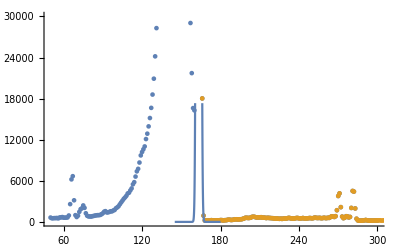

```mathematica
model=NonlinearModelFit[bkgdata,F[x,mu,sigma,a],{{mu,160},{sigma,1},{a,600000}},x];
model["ParameterTable"]
params=model["BestFitParameters"];
paramerrors=model["ParameterErrors"];

Show[ListPlot[{sourcedata[1][[50;;300]],bkgdata}],Plot[model[x],{x,145,180}],PlotRange->{{50,300},{0,30000}}]
```

```mathematica
100*paramerrors[[3]]/params[[3,2]]
```

0.270465

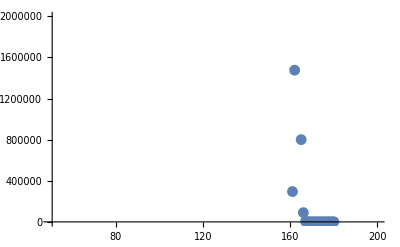

```mathematica
ListPlot[Join[Transpose[{bkgdata[[All,1]]}],Transpose[{model["FitResiduals"]}],2],PlotRange->{{50,200},Automatic}]
```

### Conclusion

```mathematica
Table[{params[[i,2]],paramerrors[[i]],100*paramerrors[[i]]/params[[i,2]]},{i,{5,10,15}}]//TableForm
background=Table[err[F2,{i[[1]],0},{params[[5,2]],paramerrors[[5]]},{params[[10,2]],paramerrors[[10]]},{params[[15,2]],paramerrors[[15]]}],{i,bkgdata}];
counts[1]=Total[background[[All,1]]];countserror[1]=Sqrt[Total[(background[[All,2]])^2]];{counts[1],countserror[1],100countserror[1]/counts[1]}
```

163.298 | 0.00119654 | 0.00073273
1.00184 | 0.00134247 | 0.134001
671704. | 715.798 | 0.106565

{1.68681×10^6,1599.22,0.0948078}

```mathematica
peakbackground=Apply[err,Join[{backgroundfunction,{params[[5,2]],paramerrors[[5]]}},Table[{params[[i,2]],paramerrors[[i]]},{i,1,4}],Table[{params[[i+5,2]],paramerrors[[i]]},{i,1,4}],Table[{params[[i+10,2]],paramerrors[[i]]},{i,1,4}]]]
countsalt[1]=NIntegrate[F2[x,params[[5,2]],params[[5+5,2]],params[[5+10,2]]],{x,params[[5,2]]-2*fwhm[params[[5+5,2]]],params[[5,2]]+2*fwhm[params[[5+5,2]]]}];
countserroralt[1]=Sqrt[paramerrors[[-1]]^2+peakbackground[[2]]^2];
{countsalt[1],countserroralt[1],100*countserroralt[1]/countsalt[1]}
```

{3410.56,1593.73}

{1.6868×10^6,1747.1,0.103575}

## Source 1-hr Trial 2

### Data Selection

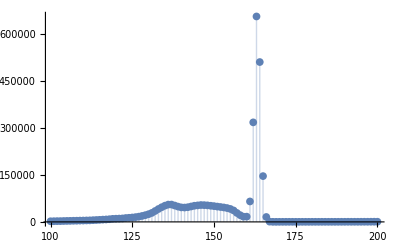

```mathematica
ListPlot[sourcedata[2][[100;;200]],Filling->Bottom,PlotRange->All]
```

### NonlinearModelFit bins

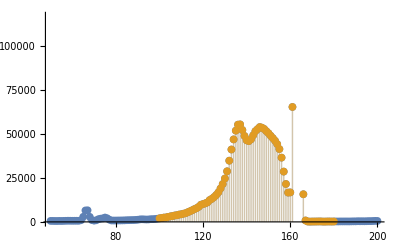

```mathematica
bkgdata=sourcedata[2][[100;;180]];
viewingdata=sourcedata[2][[50;;200]];
ListPlot[{viewingdata,bkgdata},Filling->Bottom,PlotRange->Automatic]
```

| Estimate | Standard Error | t-Statistic | P-Value
mu1 | 132.364 | 1.18318 | 111.871 | 5.57089×10^-77
mu2 | 136.273 | 0.174158 | 782.472 | 1.16148×10^-132
mu3 | 145.514 | 0.276694 | 525.904 | 2.83324×10^-121
mu4 | 153.399 | 0.432565 | 354.627 | 5.53518×10^-110
mu5 | 163.244 | 0.00120292 | 135707. | 1.92227×10^-280
sigma1 | 13.9909 | 0.545685 | 25.6392 | 4.97475×10^-36
sigma2 | 3.6978 | 0.142313 | 25.9836 | 2.22971×10^-36
sigma3 | 3.47955 | 0.295563 | 11.7726 | 7.20434×10^-18
sigma4 | 4.05511 | 0.257241 | 15.7639 | 4.60738×10^-24
sigma5 | 1.00426 | 0.00134534 | 746.471 | 2.59975×10^-131
a1 | 15454.6 | 820.654 | 18.832 | 3.0351×10^-28
a2 | 38513.3 | 1403.66 | 27.4378 | 8.2737×10^-38
a3 | 36526.5 | 2847.74 | 12.8265 | 1.37057×10^-19
a4 | 38144.6 | 2532.23 | 15.0636 | 4.86046×10^-23
a5 | 672006. | 718.227 | 935.645 | 8.73099×10^-138

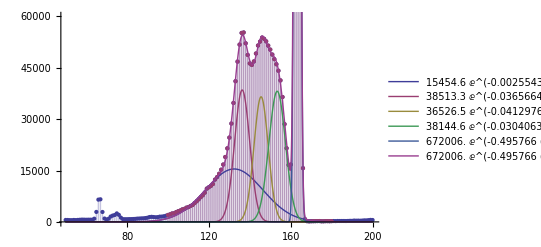

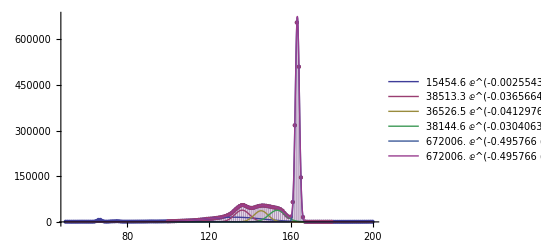

```mathematica
mu={132,136,145,153,163};sigma={10,5,5,5,1};
a={10000,30000,30000,35000,600000};n=Length[mu];

model=NonlinearModelFit[bkgdata,G[x,Table[Symbol["mu"<>ToString[i]],{i,1,n}],Table[Symbol["sigma"<>ToString[i]],{i,1,n}],Table[Symbol["a"<>ToString[i]],{i,1,n}]],Join[Table[{Symbol["mu"<>ToString[i]],mu[[i]]},{i,1,n}],Table[{Symbol["sigma"<>ToString[i]],sigma[[i]]},{i,1,n}],Table[{Symbol["a"<>ToString[i]],a[[i]]},{i,1,n}]],x];
model["ParameterTable"]
params=model["BestFitParameters"];
paramerrors=model["ParameterErrors"];

theme="Classic";
Show[ListPlot[{viewingdata,bkgdata},Filling->Bottom,PlotTheme->theme,PlotRange->All],Plot[Evaluate@Join[Table[F[x,params[[i,2]],params[[i+n,2]],params[[i+2n,2]]],{i,1,n}],{G[x,params[[;;n,2]],params[[n+1;;2n,2]],params[[2n+1;;3n,2]]]}],{x,50,200},PlotRange->All,PlotTheme->theme,PlotLegends->"Expressions"],PlotRange->{Automatic,{0,60000}}]
Show[ListPlot[{viewingdata,bkgdata},Filling->Bottom,PlotTheme->theme,PlotRange->All],Plot[Evaluate@Join[Table[F[x,params[[i,2]],params[[i+n,2]],params[[i+2n,2]]],{i,1,n}],{G[x,params[[;;n,2]],params[[n+1;;2n,2]],params[[2n+1;;3n,2]]]}],{x,50,200},PlotRange->All,PlotTheme->theme,PlotLegends->"Expressions"],PlotRange->All]
```

### Conclusion

```mathematica
Table[{params[[i,2]],paramerrors[[i]],100*paramerrors[[i]]/params[[i,2]]},{i,{5,10,15}}]//TableForm
background=Table[err[F2,{i[[1]],0},{params[[5,2]],paramerrors[[5]]},{params[[10,2]],paramerrors[[10]]},{params[[15,2]],paramerrors[[15]]}],{i,bkgdata}];
counts[2]=Total[background[[All,1]]];countserror[2]=Sqrt[Total[(background[[All,2]])^2]];{counts[2],countserror[2],100countserror[2]/counts[2]}
```

163.244 | 0.00120292 | 0.000736884
1.00426 | 0.00134534 | 0.133964
672006. | 718.227 | 0.106878

{1.69165×10^6,1605.34,0.0948982}

```mathematica
peakbackground=Apply[err,Join[{backgroundfunction,{params[[5,2]],paramerrors[[5]]}},Table[{params[[i,2]],paramerrors[[i]]},{i,1,4}],Table[{params[[i+5,2]],paramerrors[[i]]},{i,1,4}],Table[{params[[i+10,2]],paramerrors[[i]]},{i,1,4}]]]
countsalt[2]=NIntegrate[F2[x,params[[5,2]],params[[5+5,2]],params[[5+10,2]]],{x,params[[5,2]]-2*fwhm[params[[5+5,2]]],params[[5,2]]+2*fwhm[params[[5+5,2]]]}];
countserroralt[2]=Sqrt[paramerrors[[-1]]^2+peakbackground[[2]]^2];
{countsalt[2],countserroralt[2],100*countserroralt[2]/countsalt[2]}
```

{3354.73,1492.56}

{1.69164×10^6,1656.38,0.0979153}

## Thick Film

### Data Selection

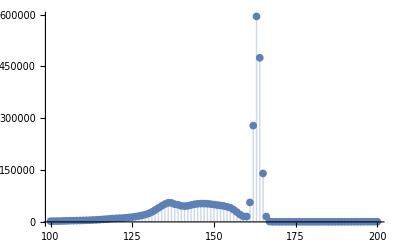

```mathematica
ListPlot[thickdata[1][[100;;200]],Filling->Bottom,PlotRange->All]
```

### NonlinearModelFit bins

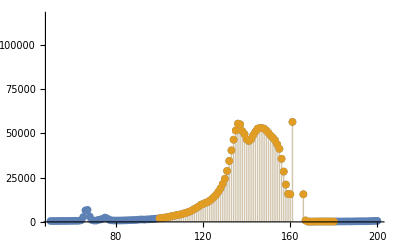

```mathematica
bkgdata=thickdata[1][[100;;180]];
viewingdata=thickdata[1][[50;;200]];
ListPlot[{viewingdata,bkgdata},Filling->Bottom,PlotRange->Automatic]
```

| Estimate | Standard Error | t-Statistic | P-Value
mu1 | 132.618 | 1.06253 | 124.813 | 4.19499×10^-80
mu2 | 136.298 | 0.178116 | 765.219 | 5.05831×10^-132
mu3 | 145.605 | 0.297034 | 490.195 | 2.93246×10^-119
mu4 | 153.45 | 0.44452 | 345.205 | 3.27037×10^-109
mu5 | 163.274 | 0.00126452 | 129119. | 5.13053×10^-279
sigma1 | 14.0959 | 0.489676 | 28.7862 | 4.43733×10^-39
sigma2 | 3.69255 | 0.140292 | 26.3204 | 1.02592×10^-36
sigma3 | 3.54503 | 0.318343 | 11.1359 | 8.42059×10^-17
sigma4 | 3.95885 | 0.250739 | 15.7887 | 4.24307×10^-24
sigma5 | 1.00215 | 0.00141369 | 708.891 | 7.85894×10^-130
a1 | 15590.5 | 770.416 | 20.2365 | 5.25328×10^-30
a2 | 37957.8 | 1351.92 | 28.0769 | 2.03715×10^-38
a3 | 36408. | 2770.28 | 13.1424 | 4.29454×10^-20
a4 | 37228.5 | 2688.71 | 13.8462 | 3.38647×10^-21
a5 | 613953. | 690.61 | 889.002 | 2.5511×10^-136

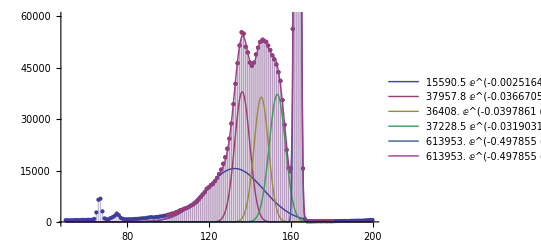

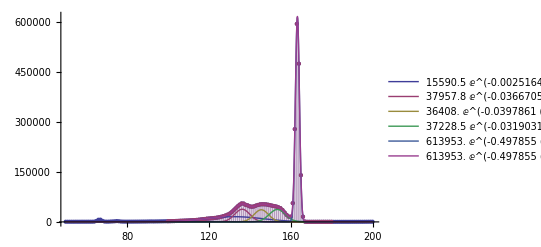

```mathematica
mu={132,136,145,153,163};sigma={10,5,5,5,1};
a={10000,30000,30000,35000,600000};n=Length[mu];

model=NonlinearModelFit[bkgdata,G[x,Table[Symbol["mu"<>ToString[i]],{i,1,n}],Table[Symbol["sigma"<>ToString[i]],{i,1,n}],Table[Symbol["a"<>ToString[i]],{i,1,n}]],Join[Table[{Symbol["mu"<>ToString[i]],mu[[i]]},{i,1,n}],Table[{Symbol["sigma"<>ToString[i]],sigma[[i]]},{i,1,n}],Table[{Symbol["a"<>ToString[i]],a[[i]]},{i,1,n}]],x];
model["ParameterTable"]
params=model["BestFitParameters"];
paramerrors=model["ParameterErrors"];

theme="Classic";
Show[ListPlot[{viewingdata,bkgdata},Filling->Bottom,PlotTheme->theme,PlotRange->All],Plot[Evaluate@Join[Table[F[x,params[[i,2]],params[[i+n,2]],params[[i+2n,2]]],{i,1,n}],{G[x,params[[;;n,2]],params[[n+1;;2n,2]],params[[2n+1;;3n,2]]]}],{x,50,200},PlotRange->All,PlotTheme->theme,PlotLegends->"Expressions"],PlotRange->{Automatic,{0,60000}}]
Show[ListPlot[{viewingdata,bkgdata},Filling->Bottom,PlotTheme->theme,PlotRange->All],Plot[Evaluate@Join[Table[F[x,params[[i,2]],params[[i+n,2]],params[[i+2n,2]]],{i,1,n}],{G[x,params[[;;n,2]],params[[n+1;;2n,2]],params[[2n+1;;3n,2]]]}],{x,50,200},PlotRange->All,PlotTheme->theme,PlotLegends->"Expressions"],PlotRange->All]
```

### Conclusion

```mathematica
Table[{params[[i,2]],paramerrors[[i]],100*paramerrors[[i]]/params[[i,2]]},{i,{5,10,15}}]//TableForm
background=Table[err[F2,{i[[1]],0},{params[[5,2]],paramerrors[[5]]},{params[[10,2]],paramerrors[[10]]},{params[[15,2]],paramerrors[[15]]}],{i,bkgdata}];
counts[3]=Total[background[[All,1]]];countserror[3]=Sqrt[Total[(background[[All,2]])^2]];{counts[3],countserror[3],100countserror[3]/counts[3]}
```

163.274 | 0.00126452 | 0.00077448
1.00215 | 0.00141369 | 0.141065
613953. | 690.61 | 0.112486

{1.54226×10^6,1542.15,0.0999925}

```mathematica
peakbackground=Apply[err,Join[{backgroundfunction,{params[[5,2]],paramerrors[[5]]}},Table[{params[[i,2]],paramerrors[[i]]},{i,1,4}],Table[{params[[i+5,2]],paramerrors[[i]]},{i,1,4}],Table[{params[[i+10,2]],paramerrors[[i]]},{i,1,4}]]]
countsalt[3]=NIntegrate[F2[x,params[[5,2]],params[[5+5,2]],params[[5+10,2]]],{x,params[[5,2]]-2*fwhm[params[[5+5,2]]],params[[5,2]]+2*fwhm[params[[5+5,2]]]}];
countserroralt[3]=Sqrt[paramerrors[[-1]]^2+peakbackground[[2]]^2];
{countsalt[3],countserroralt[3],100*countserroralt[3]/countsalt[3]}
```

{3178.07,1400.42}

{1.54226×10^6,1561.45,0.101244}

## Thin Film

### Data Selection

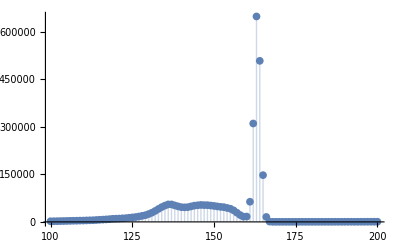

```mathematica
ListPlot[thindata[1][[100;;200]],Filling->Bottom,PlotRange->All]
```

### NonlinearModelFit bins

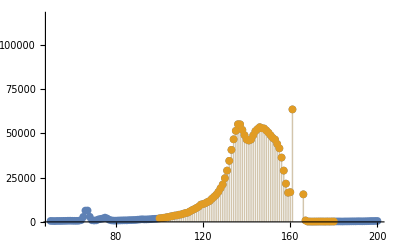

```mathematica
bkgdata=thindata[1][[100;;180]];
viewingdata=thindata[1][[50;;200]];
ListPlot[{viewingdata,bkgdata},Filling->Bottom,PlotRange->Automatic]
```

| Estimate | Standard Error | t-Statistic | P-Value
mu1 | 132.345 | 1.17371 | 112.757 | 3.31735×10^-77
mu2 | 136.322 | 0.175587 | 776.382 | 1.94514×10^-132
mu3 | 145.556 | 0.277581 | 524.373 | 3.43438×10^-121
mu4 | 153.409 | 0.430668 | 356.213 | 4.12367×10^-110
mu5 | 163.254 | 0.00117673 | 138735. | 4.47912×10^-281
sigma1 | 13.9419 | 0.538692 | 25.881 | 2.82902×10^-36
sigma2 | 3.736 | 0.142597 | 26.1998 | 1.35343×10^-36
sigma3 | 3.48282 | 0.295242 | 11.7965 | 6.57509×10^-18
sigma4 | 4.06406 | 0.254127 | 15.9923 | 2.16512×10^-24
sigma5 | 1.00361 | 0.00131793 | 761.503 | 6.97467×10^-132
a1 | 15420.6 | 813.492 | 18.956 | 2.10358×10^-28
a2 | 38402.7 | 1404.51 | 27.3424 | 1.02239×10^-37
a3 | 36052.8 | 2887.47 | 12.486 | 4.85663×10^-19
a4 | 38249.9 | 2536.7 | 15.0786 | 4.61918×10^-23
a5 | 665747. | 696.961 | 955.214 | 2.22739×10^-138

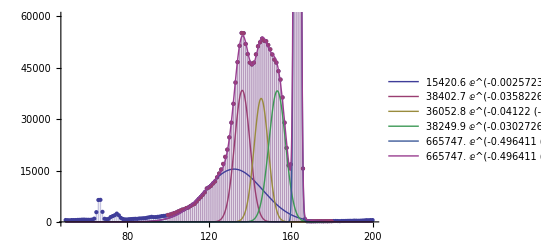

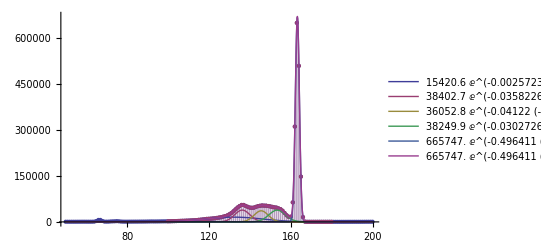

```mathematica
mu={131,134,146,154,163};sigma={15,3,3,4,1};
a={15000,30000,30000,30000,662000};n=Length[mu];

model=NonlinearModelFit[bkgdata,G[x,Table[Symbol["mu"<>ToString[i]],{i,1,n}],Table[Symbol["sigma"<>ToString[i]],{i,1,n}],Table[Symbol["a"<>ToString[i]],{i,1,n}]],Join[Table[{Symbol["mu"<>ToString[i]],mu[[i]]},{i,1,n}],Table[{Symbol["sigma"<>ToString[i]],sigma[[i]]},{i,1,n}],Table[{Symbol["a"<>ToString[i]],a[[i]]},{i,1,n}]],x];
model["ParameterTable"]
params=model["BestFitParameters"];
paramerrors=model["ParameterErrors"];

theme="Classic";
Show[ListPlot[{viewingdata,bkgdata},Filling->Bottom,PlotTheme->theme,PlotRange->All],Plot[Evaluate@Join[Table[F[x,params[[i,2]],params[[i+n,2]],params[[i+2n,2]]],{i,1,n}],{G[x,params[[;;n,2]],params[[n+1;;2n,2]],params[[2n+1;;3n,2]]]}],{x,50,200},PlotRange->All,PlotTheme->theme,PlotLegends->"Expressions"],PlotRange->{Automatic,{0,60000}}]
Show[ListPlot[{viewingdata,bkgdata},Filling->Bottom,PlotTheme->theme,PlotRange->All],Plot[Evaluate@Join[Table[F[x,params[[i,2]],params[[i+n,2]],params[[i+2n,2]]],{i,1,n}],{G[x,params[[;;n,2]],params[[n+1;;2n,2]],params[[2n+1;;3n,2]]]}],{x,50,200},PlotRange->All,PlotTheme->theme,PlotLegends->"Expressions"],PlotRange->All]
```

### Conclusion

```mathematica
Table[{params[[i,2]],paramerrors[[i]],100*paramerrors[[i]]/params[[i,2]]},{i,{5,10,15}}]//TableForm
background=Table[err[F2,{i[[1]],0},{params[[5,2]],paramerrors[[5]]},{params[[10,2]],paramerrors[[10]]},{params[[15,2]],paramerrors[[15]]}],{i,bkgdata}];
counts[4]=Total[background[[All,1]]];countserror[4]=Sqrt[Total[(background[[All,2]])^2]];{counts[4],countserror[4],100countserror[4]/counts[4]}
```

163.254 | 0.00117673 | 0.000720799
1.00361 | 0.00131793 | 0.131319
665747. | 696.961 | 0.104689

{1.6748×10^6,1557.41,0.0929909}

```mathematica
peakbackground=Apply[err,Join[{backgroundfunction,{params[[5,2]],paramerrors[[5]]}},Table[{params[[i,2]],paramerrors[[i]]},{i,1,4}],Table[{params[[i+5,2]],paramerrors[[i]]},{i,1,4}],Table[{params[[i+10,2]],paramerrors[[i]]},{i,1,4}]]]
countsalt[4]=NIntegrate[F2[x,params[[5,2]],params[[5+5,2]],params[[5+10,2]]],{x,params[[5,2]]-2*fwhm[params[[5+5,2]]],params[[5,2]]+2*fwhm[params[[5+5,2]]]}];
countserroralt[4]=Sqrt[paramerrors[[-1]]^2+peakbackground[[2]]^2];
{countsalt[4],countserroralt[4],100*countserroralt[4]/countsalt[4]}
```

{3355.57,1494.28}

{1.6748×10^6,1648.83,0.0984495}

## Calculations

```mathematica
thickness=40;thicknesserror=0.01;
Print["Peak Data\n",Table[{counts[i],countserror[i],100*countserror[i]/counts[i]},{i,1,4}]//TableForm,"\n"]
coeff[counts1_,counts3_,thickness_]:=(-Log[counts3/counts1])/thickness;


attencoeff=err[coeff,{counts[1],countserror[1]},{counts[3],countserror[3]},{thickness,thicknesserror}];
thinmeasure=err[coeff,{counts[1],countserror[1]},{counts[4],countserror[4]},attencoeff];Join[thinmeasure,{100*thinmeasure[[2]]/thinmeasure[[1]]}]

attencoeff=err[coeff,{counts[2],countserror[2]},{counts[3],countserror[3]},{thickness,thicknesserror}];
thinmeasure=err[coeff,{counts[2],countserror[2]},{counts[4],countserror[4]},attencoeff];Join[thinmeasure,{100*thinmeasure[[2]]/thinmeasure[[1]]}]

thick[counts1_,counts2_,counts3_,thickness_]:=thickness Log[counts3/counts1]/Log[counts2/counts1]
thinmeasure=err[thick,{counts[1],countserror[1]},{counts[3],countserror[3]},{counts[4],countserror[4]},{thickness,thicknesserror}];
Join[thinmeasure,{100*thinmeasure[[2]]/thinmeasure[[1]]}]

thinmeasure=err[thick,{counts[2],countserror[2]},{counts[3],countserror[3]},{counts[4],countserror[4]},{thickness,thicknesserror}];
Join[thinmeasure,{100*thinmeasure[[2]]/thinmeasure[[1]]}]
```

Peak Data
1.68681×10^6 | 1599.22 | 0.0948078
1.69165×10^6 | 1605.34 | 0.0948982
1.54226×10^6 | 1542.15 | 0.0999925
1.6748×10^6 | 1557.41 | 0.0929909

{3.18942,0.594975,18.6546}

{4.33021,0.578468,13.3589}

{3.18942,0.570455,17.8859}

{4.33021,0.546009,12.6093}

```mathematica
thickness=40;thicknesserror=0.01;
Print["Peak Data\n",Table[{countsalt[i],countserroralt[i],100*countserroralt[i]/countsalt[i]},{i,1,4}]//TableForm,"\n"]
coeff[counts1_,counts3_,thickness_]:=(-Log[counts3/counts1])/thickness;


attencoeff=err[coeff,{countsalt[1],countserroralt[1]},{countsalt[3],countserroralt[3]},{thickness,thicknesserror}];
thinmeasure=err[coeff,{countsalt[1],countserroralt[1]},{countsalt[4],countserroralt[4]},attencoeff];Join[thinmeasure,{100*thinmeasure[[2]]/thinmeasure[[1]]}]

attencoeff=err[coeff,{countsalt[2],countserroralt[2]},{countsalt[3],countserroralt[3]},{thickness,thicknesserror}];
thinmeasure=err[coeff,{countsalt[2],countserroralt[2]},{countsalt[4],countserroralt[4]},attencoeff];Join[thinmeasure,{100*thinmeasure[[2]]/thinmeasure[[1]]}]

thick[counts1_,counts2_,counts3_,thickness_]:=thickness Log[counts3/counts1]/Log[counts2/counts1]
thinmeasure=err[thick,{countsalt[1],countserroralt[1]},{countsalt[3],countserroralt[3]},{countsalt[4],countserroralt[4]},{thickness,thicknesserror}];
Join[thinmeasure,{100*thinmeasure[[2]]/thinmeasure[[1]]}]

thinmeasure=err[thick,{countsalt[2],countserroralt[2]},{countsalt[3],countserroralt[3]},{countsalt[4],countserroralt[4]},{thickness,thicknesserror}];
Join[thinmeasure,{100*thinmeasure[[2]]/thinmeasure[[1]]}]
```

Peak Data
1.6868×10^6 | 1747.1 | 0.103575
1.69164×10^6 | 1656.38 | 0.0979153
1.54226×10^6 | 1561.45 | 0.101244
1.6748×10^6 | 1648.83 | 0.0984495

{3.18942,0.64012,20.0701}

{4.33021,0.604368,13.957}

{3.18942,0.612901,19.2167}

{4.33021,0.571317,13.1937}

```mathematica
thickness=40;thicknesserror=0.01;theoerror=84;
100*theoerror/counts[1]
attencoeff=err[coeff,{counts[1],theoerror},{counts[3],theoerror},{thickness,thicknesserror}];
thinmeasure=err[coeff,{counts[1],theoerror},{counts[4],theoerror},attencoeff];Join[thinmeasure,{100*thinmeasure[[2]]/thinmeasure[[1]]}]
```

0.00497982

{3.18942,0.0316769,0.993186}

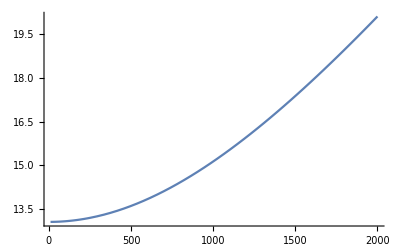

```mathematica
Plot[100*err[thick,{counts[1],x},{counts[3],countserror[3]},{counts[4],countserror[4]},{thickness,thicknesserror}][[2]]/err[thick,{counts[1],x},{counts[3],countserror[3]},{counts[4],countserror[4]},{thickness,thicknesserror}][[1]],{x,10,2000}]
```

# Data Set 1

```mathematica
ClearAll["Global`*"]
(*~ MacOS ~*)
main="/Users/mikhailgaerlan/Box Sync/Education/MSU/Research/Radiation Thickness/Data";

SetDirectory[main];
$Line=0;
```

## Data Import

## Source 1-Hour

```mathematica
ToExpression[StringSplit[imported[[-7]]]]
```

{0.137869,0.366631}

### Trial 1

$SPEC_ID:
Molnar Range
$SPEC_REM:
DET# 1
DETDESC# HPGe Detector 1
AP# GammaVision Version 6.07
$DATE_MEA:
10/19/2015 09:56:53
$MEAS_TIM:
3600 3733
$DATA:
0 8191
       0
       0
       0

0
       0
$ROI:
0
$PRESETS:
Live Time
3600
0
$ENER_FIT:
0.137869 0.366631
$MCA_CAL:
3
1.378689E-001 3.666307E-001 -4.415950E-008 keV
$SHAPE_CAL:
3
2.301834E+000 9.195991E-004 -5.357180E-008

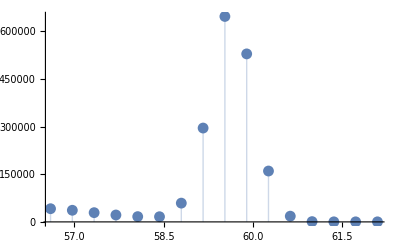

```mathematica
imported=Import["Am-241-1hr-10192015.Spe","Data"];
times=ToExpression[StringSplit[imported[[10]]]];
deadtime=N[Abs[times[[1]]-times[[2]]]/times[[2]]];
imported[[;;15]]//TableForm
imported[[-16;;]]//TableForm
energy=ToExpression[StringSplit[imported[[-7]]]];
freq=ToExpression[imported[[13;;-15]]]/(1-deadtime);
sourcedata[1]=Table[{i,energy[[1]]+energy[[2]](i-1),freq[[i]]},{i,Length[freq]}];
ListPlot[sourcedata[1][[155;;170,{2,3}]],PlotRange->All,Filling->Bottom]
```

```mathematica
imported[[;;15]]//TableForm
imported[[-16;;]]//TableForm
Drop[imported,{16,Length[imported]-16}]//TableForm//TeXForm
```

$SPEC_ID:
Molnar Range
$SPEC_REM:
DET# 1
DETDESC# HPGe Detector 1
AP# GammaVision Version 6.07
$DATE_MEA:
10/19/2015 09:56:53
$MEAS_TIM:
3600 3733
$DATA:
0 8191
       0
       0
       0

0
       0
$ROI:
0
$PRESETS:
Live Time
3600
0
$ENER_FIT:
0.137869 0.366631
$MCA_CAL:
3
1.378689E-001 3.666307E-001 -4.415950E-008 keV
$SHAPE_CAL:
3
2.301834E+000 9.195991E-004 -5.357180E-008

\begin{array}{c}
 \text{$\$$SPEC$\_$ID:} \\
 \text{Molnar Range} \\
 \text{$\$$SPEC$\_$REM:} \\
 \text{DET$\#$ 1} \\
 \text{DETDESC$\#$ HPGe Detector 1} \\
 \text{AP$\#$ GammaVision Version 6.07} \\
 \text{$\$$DATE$\_$MEA:} \\
 \text{10/19/2015 09:56:53} \\
 \text{$\$$MEAS$\_$TIM:} \\
 \text{3600 3733} \\
 \text{$\$$DATA:} \\
 \text{0 8191} \\
 \text{       0} \\
 \text{       0} \\
 \text{       0} \\
 \text{       0} \\
 \text{       0} \\
 \text{$\$$ROI:} \\
 0 \\
 \text{$\$$PRESETS:} \\
 \text{Live Time} \\
 3600 \\
 0 \\
 \text{$\$$ENER$\_$FIT:} \\
 \text{0.137869 0.366631} \\
 \text{$\$$MCA$\_$CAL:} \\
 3 \\
 \text{1.378689E-001 3.666307E-001 -4.415950E-008 keV} \\
 \text{$\$$SHAPE$\_$CAL:} \\
 3 \\
 \text{2.301834E+000 9.195991E-004 -5.357180E-008} \\
\end{array}

### Trial 2

```mathematica
imported=Import["Am-241-1hrTrial2-10192015.Spe","Data"];
times=ToExpression[StringSplit[imported[[10]]]];
deadtime=N[Abs[times[[1]]-times[[2]]]/times[[2]]];
imported[[;;15]]//TableForm
imported[[-16;;]]//TableForm
freq=ToExpression[imported[[13;;-15]]]/(1-deadtime);
sourcedata[2]=Table[{i,freq[[i]]},{i,Length[freq]}];
ListPlot[sourcedata[2][[155;;170]],PlotRange->All,Filling->Bottom]
```

$SPEC_ID:
Molnar Range
$SPEC_REM:
DET# 1
DETDESC# HPGe Detector 1
AP# GammaVision Version 6.07
$DATE_MEA:
10/19/2015 14:15:00
$MEAS_TIM:
3600 3732
$DATA:
0 8191
       0
       0
       0

0
       0
$ROI:
0
$PRESETS:
Live Time
3600
0
$ENER_FIT:
0.137869 0.366631
$MCA_CAL:
3
1.378689E-001 3.666307E-001 -4.415950E-008 keV
$SHAPE_CAL:
3
2.301834E+000 9.195991E-004 -5.357180E-008

-Graphics-

## Thick Film

```mathematica
imported=Import["Am-241-ThickFilm-1hr-10192015.Spe","Data"];
times=ToExpression[StringSplit[imported[[10]]]];
deadtime=N[Abs[times[[1]]-times[[2]]]/times[[2]]];
imported[[;;15]]//TableForm
imported[[-16;;]]//TableForm
freq=ToExpression[imported[[13;;-15]]]/(1-deadtime);
thickdata[1]=Table[{i,freq[[i]]},{i,Length[freq]}];
ListPlot[thickdata[1][[155;;170]],PlotRange->All,Filling->Bottom]
```

$SPEC_ID:
Molnar Range
$SPEC_REM:
DET# 1
DETDESC# HPGe Detector 1
AP# GammaVision Version 6.07
$DATE_MEA:
10/19/2015 11:10:33
$MEAS_TIM:
3600 3727
$DATA:
0 8191
       0
       0
       0

0
       0
$ROI:
0
$PRESETS:
Live Time
3600
0
$ENER_FIT:
0.137869 0.366631
$MCA_CAL:
3
1.378689E-001 3.666307E-001 -4.415950E-008 keV
$SHAPE_CAL:
3
2.301834E+000 9.195991E-004 -5.357180E-008

-Graphics-

## Thin Film

```mathematica
imported=Import["Am-241-ThinFilm-1hr-10192015.Spe","Data"];
times=ToExpression[StringSplit[imported[[10]]]];
deadtime=N[Abs[times[[1]]-times[[2]]]/times[[2]]];
imported[[;;15]]//TableForm
imported[[-16;;]]//TableForm
freq=ToExpression[imported[[13;;-15]]]/(1-deadtime);
thindata[1]=Table[{i,freq[[i]]},{i,Length[freq]}];
ListPlot[thindata[1][[155;;170]],PlotRange->All,Filling->Bottom]
```

$SPEC_ID:
Molnar Range
$SPEC_REM:
DET# 1
DETDESC# HPGe Detector 1
AP# GammaVision Version 6.07
$DATE_MEA:
10/19/2015 13:11:13
$MEAS_TIM:
3600 3732
$DATA:
0 8191
       0
       0
       0

0
       1
$ROI:
0
$PRESETS:
Live Time
3600
0
$ENER_FIT:
0.137869 0.366631
$MCA_CAL:
3
1.378689E-001 3.666307E-001 -4.415950E-008 keV
$SHAPE_CAL:
3
2.301834E+000 9.195991E-004 -5.357180E-008

-Graphics-

## Data Analysis

## Equations

```mathematica
F[x_,mu_,sigma_,a_]:=a*Exp[-1/2*((x-mu)/sigma)^2]
F2[x_,mu_,sigma_,a_]:=a*Exp[-1/2*((x-mu)/sigma)^2]
G[x_,mu_,sigma_,a_]:=Sum[F[x,mu[[i]],sigma[[i]],a[[i]]],{i,1,Length[mu]}]

chisq2[data_,mu_,sigma_,a_]:=Sum[(data[[i,2]]-G[data[[i,1]],mu,sigma,a])^2,{i,Length[data]}]
backgroundfunction[x_,mu1_,mu2_,mu3_,mu4_,sigma1_,sigma2_,sigma3_,sigma4_,a1_,a2_,a3_,a4_]:=F2[x,mu1,sigma1,a1]+F2[x,mu2,sigma2,a2]+F2[x,mu3,sigma3,a3]+F2[x,mu4,sigma4,a4];
fwhm[sigma_]:=2*sigma*Sqrt[2*Log[2]];

err[F_,w__]:={F[Map[First,List[w]]/.List->Sequence],Block[{parms=Table[Unique[],{x,1,Length[List[w]]}],values=Table[List[w][[i,1]],{i,1,Length[List[w]]}],errors=Table[List[w][[i,2]],{i,1,Length[List[w]]}]},Sqrt[Total[Table[(D[F[parms/.List->Sequence],parms[[i]]]*errors[[i]])^2,{i,1,Length[values]}]/.Table[parms[[i]]->values[[i]],{i,1,Length[values]}]]]]}
```

## Source 1-hr Trial 1

### Data Selection

```mathematica
ListPlot[sourcedata[1][[100;;200]],Filling->Bottom,PlotRange->All]
```

-Graphics-

### NonlinearModelFit bins

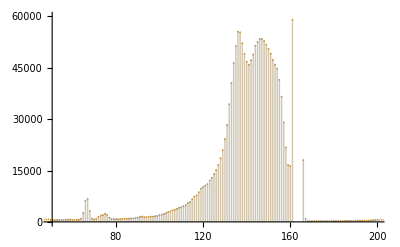

```mathematica
bkgdata=sourcedata[1];
viewingdata=sourcedata[1][[50;;200]];
ListPlot[{viewingdata,bkgdata},Filling->Bottom,PlotRange->{{50,200},{0,60000}}]
```

| Estimate | Standard Error | t-Statistic | P-Value
mu1 | 132.655 | 0.293076 | 452.63 | 1.2372080847×10^-5791
mu2 | 136.313 | 0.0539696 | 2525.74 | 9.5451826276×10^-11830
mu3 | 145.619 | 0.0891381 | 1633.64 | 1.5101468319×10^-10285
mu4 | 153.501 | 0.136834 | 1121.8 | 8.3129328674×10^-8957
mu5 | 163.298 | 0.000359868 | 453772. | 4.179904314×10^-30262
sigma1 | 14.7198 | 0.135107 | 108.949 | 6.021590419×10^-1595
sigma2 | 3.7179 | 0.0417903 | 88.9656 | 1.0677304084×10^-1204
sigma3 | 3.53744 | 0.0959074 | 36.8839 | 1.27508×10^-275
sigma4 | 3.99928 | 0.0775692 | 51.5576 | 2.9040059477×10^-502
sigma5 | 1.00155 | 0.000401646 | 2493.62 | 2.3911408443×10^-11784
a1 | 15040.8 | 209.34 | 71.8487 | 1.5654174935×10^-871
a2 | 38693. | 377.204 | 102.578 | 2.2530999928×10^-1471
a3 | 36572.1 | 868.034 | 42.1321 | 3.0390689757×10^-351
a4 | 37241.9 | 776.679 | 47.9502 | 2.0326260627×10^-442
a5 | 671575. | 214.371 | 3132.77 | 7.9262410036×10^-12594

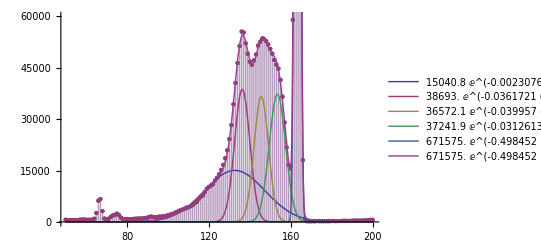

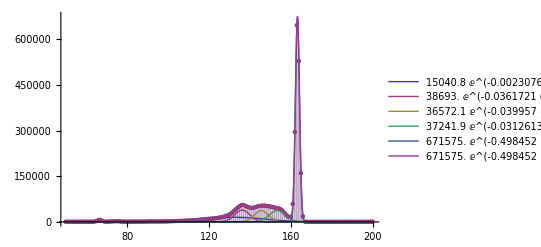

```mathematica
mu={131.6,136.3,145.6,153.3,163.2};sigma={14.6,3.8,3.4,4.0,1.0};
a={15000,30000,10800,30000,730000};n=Length[mu];

model=NonlinearModelFit[bkgdata,G[x,Table[Symbol["mu"<>ToString[i]],{i,1,n}],Table[Symbol["sigma"<>ToString[i]],{i,1,n}],Table[Symbol["a"<>ToString[i]],{i,1,n}]],Join[Table[{Symbol["mu"<>ToString[i]],mu[[i]]},{i,1,n}],Table[{Symbol["sigma"<>ToString[i]],sigma[[i]]},{i,1,n}],Table[{Symbol["a"<>ToString[i]],a[[i]]},{i,1,n}]],x];
model["ParameterTable"]
params=model["BestFitParameters"];
paramerrors=model["ParameterErrors"];

theme="Classic";
Show[ListPlot[{viewingdata,bkgdata[[50;;200]]},Filling->Bottom,PlotTheme->theme,PlotRange->All],Plot[Evaluate@Join[Table[F[x,params[[i,2]],params[[i+n,2]],params[[i+2n,2]]],{i,1,n}],{G[x,params[[;;n,2]],params[[n+1;;2n,2]],params[[2n+1;;3n,2]]]}],{x,50,200},PlotRange->All,PlotTheme->theme,PlotLegends->"Expressions"],PlotRange->{{50,200},{0,60000}}]
Show[ListPlot[{viewingdata,bkgdata[[50;;200]]},Filling->Bottom,PlotTheme->theme,PlotRange->All],Plot[Evaluate@Join[Table[F[x,params[[i,2]],params[[i+n,2]],params[[i+2n,2]]],{i,1,n}],{G[x,params[[;;n,2]],params[[n+1;;2n,2]],params[[2n+1;;3n,2]]]}],{x,50,200},PlotRange->All,PlotTheme->theme,PlotLegends->"Expressions"],PlotRange->{{50,200},All}]
```

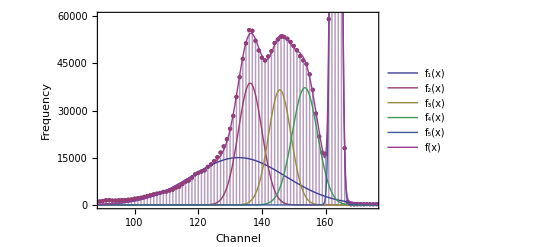

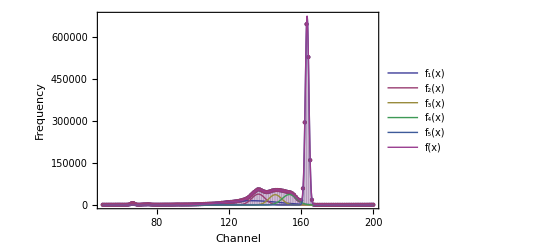

```mathematica
Show[ListPlot[{viewingdata,bkgdata[[50;;200]]},Filling->Bottom,PlotTheme->theme,PlotRange->All],Plot[Evaluate@Join[Table[F[x,params[[i,2]],params[[i+n,2]],params[[i+2n,2]]],{i,1,n}],{G[x,params[[;;n,2]],params[[n+1;;2n,2]],params[[2n+1;;3n,2]]]}],{x,50,200},PlotRange->All,PlotTheme->theme,PlotLegends->{"f_1(x)","f_2(x)","f_3(x)","f_4(x)","f_5(x)","f(x)"}],PlotRange->{{90,175},{0,60000}},Frame->{{True,False},{True,False}},FrameTicks->{{True,False},{True,False}},FrameLabel->{"Channel","Frequency"},BaseStyle->{FontSize->12}]
Show[ListPlot[{viewingdata,bkgdata[[50;;200]]},Filling->Bottom,PlotTheme->theme,PlotRange->All],Plot[Evaluate@Join[Table[F[x,params[[i,2]],params[[i+n,2]],params[[i+2n,2]]],{i,1,n}],{G[x,params[[;;n,2]],params[[n+1;;2n,2]],params[[2n+1;;3n,2]]]}],{x,50,200},PlotRange->All,PlotTheme->theme,PlotLegends->{"f_1(x)","f_2(x)","f_3(x)","f_4(x)","f_5(x)","f(x)"}],PlotRange->{{50,200},All},Frame->{{True,False},{True,False}},FrameTicks->{{True,False},{True,False}},FrameLabel->{"Channel","Frequency"},BaseStyle->{FontSize->12}]
```

### Conclusion

```mathematica
Table[{params[[i,2]],paramerrors[[i]],100*paramerrors[[i]]/params[[i,2]]},{i,{5,10,15}}]//TableForm
background=Table[err[F2,{i[[1]],0},{params[[5,2]],paramerrors[[5]]},{params[[10,2]],paramerrors[[10]]},{params[[15,2]],paramerrors[[15]]}],{i,bkgdata}];
counts[1]=Total[background[[All,1]]];countserror[1]=Sqrt[Total[(background[[All,2]])^2]];{counts[1],countserror[1],100countserror[1]/counts[1]}
```

163.298 | 0.000359868 | 0.000220375
1.00155 | 0.000401646 | 0.0401024
671575. | 214.371 | 0.0319206

{1.686×10^6,479.158,0.0284198}

```mathematica
peakbackground=Apply[err,Join[{backgroundfunction,{params[[5,2]],paramerrors[[5]]}},Table[{params[[i,2]],paramerrors[[i]]},{i,1,4}],Table[{params[[i+5,2]],paramerrors[[i]]},{i,1,4}],Table[{params[[i+10,2]],paramerrors[[i]]},{i,1,4}]]]
countsalt[1]=NIntegrate[F2[x,params[[5,2]],params[[5+5,2]],params[[5+10,2]]],{x,params[[5,2]]-2*fwhm[params[[5+5,2]]],params[[5,2]]+2*fwhm[params[[5+5,2]]]}];
countserroralt[1]=Sqrt[paramerrors[[-1]]^2+peakbackground[[2]]^2];
{countsalt[1],countserroralt[1],100*countserroralt[1]/countsalt[1]}
```

{3575.95,442.837}

{1.686×10^6,491.996,0.0291813}

## Source 1-hr Trial 2

### Data Selection

```mathematica
ListPlot[sourcedata[2][[100;;200]],Filling->Bottom,PlotRange->All]
```

-Graphics-

### NonlinearModelFit bins

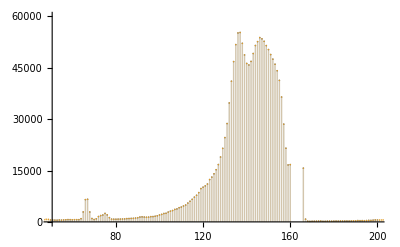

```mathematica
bkgdata=sourcedata[2];
viewingdata=sourcedata[2][[50;;200]];
ListPlot[{viewingdata,bkgdata},Filling->Bottom,PlotRange->{{50,200},{0,60000}}]
```

| Estimate | Standard Error | t-Statistic | P-Value
mu1 | 132.367 | 0.312662 | 423.355 | 6.5056197051×10^-5564
mu2 | 136.31 | 0.0506408 | 2691.71 | 1.7389585522×10^-12055
mu3 | 145.55 | 0.0784695 | 1854.86 | 2.4555062222×10^-10735
mu4 | 153.356 | 0.123843 | 1238.32 | 1.1533731865×10^-9305
mu5 | 163.244 | 0.000361228 | 451915. | 1.5298650788×10^-30247
sigma1 | 14.6109 | 0.143284 | 101.972 | 1.4803472521×10^-1459
sigma2 | 3.78596 | 0.0415559 | 91.1054 | 1.0203258955×10^-1246
sigma3 | 3.41803 | 0.0830007 | 41.1807 | 4.9027284834×10^-337
sigma4 | 4.04554 | 0.074138 | 54.5677 | 7.115185732×10^-554
sigma5 | 1.00398 | 0.00040197 | 2497.64 | 4.6225776688×10^-11790
a1 | 14911. | 216.259 | 68.9496 | 2.4458162703×10^-816
a2 | 39058.5 | 364.159 | 107.257 | 3.1091755891×10^-1562
a3 | 36144. | 849.684 | 42.5382 | 2.2691487585×10^-357
a4 | 38091.1 | 683.546 | 55.7257 | 4.2662631628×10^-574
a5 | 671877. | 214.782 | 3128.19 | 1.2444461137×10^-12588

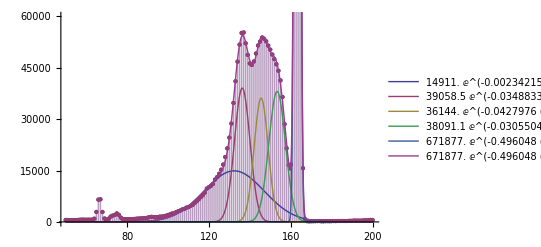

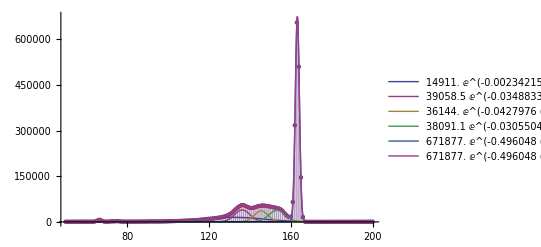

```mathematica
mu={131.6,135.3,144.6,152.5,162.3};sigma={14.2,3.6,3.6,4.0,1.0};
a={15000,30000,10800,30000,730000};n=Length[mu];

model=NonlinearModelFit[bkgdata,G[x,Table[Symbol["mu"<>ToString[i]],{i,1,n}],Table[Symbol["sigma"<>ToString[i]],{i,1,n}],Table[Symbol["a"<>ToString[i]],{i,1,n}]],Join[Table[{Symbol["mu"<>ToString[i]],mu[[i]]},{i,1,n}],Table[{Symbol["sigma"<>ToString[i]],sigma[[i]]},{i,1,n}],Table[{Symbol["a"<>ToString[i]],a[[i]]},{i,1,n}]],x];
model["ParameterTable"]
params=model["BestFitParameters"];
paramerrors=model["ParameterErrors"];

theme="Classic";
Show[ListPlot[{viewingdata,bkgdata[[50;;200]]},Filling->Bottom,PlotTheme->theme,PlotRange->All],Plot[Evaluate@Join[Table[F[x,params[[i,2]],params[[i+n,2]],params[[i+2n,2]]],{i,1,n}],{G[x,params[[;;n,2]],params[[n+1;;2n,2]],params[[2n+1;;3n,2]]]}],{x,50,200},PlotRange->All,PlotTheme->theme,PlotLegends->"Expressions"],PlotRange->{{50,200},{0,60000}}]
Show[ListPlot[{viewingdata,bkgdata[[50;;200]]},Filling->Bottom,PlotTheme->theme,PlotRange->All],Plot[Evaluate@Join[Table[F[x,params[[i,2]],params[[i+n,2]],params[[i+2n,2]]],{i,1,n}],{G[x,params[[;;n,2]],params[[n+1;;2n,2]],params[[2n+1;;3n,2]]]}],{x,50,200},PlotRange->All,PlotTheme->theme,PlotLegends->"Expressions"],PlotRange->{{50,200},All}]
```

### Conclusion

```mathematica
Table[{params[[i,2]],paramerrors[[i]],100*paramerrors[[i]]/params[[i,2]]},{i,{5,10,15}}]//TableForm
background=Table[err[F2,{i[[1]],0},{params[[5,2]],paramerrors[[5]]},{params[[10,2]],paramerrors[[10]]},{params[[15,2]],paramerrors[[15]]}],{i,bkgdata}];
counts[2]=Total[background[[All,1]]];countserror[2]=Sqrt[Total[(background[[All,2]])^2]];{counts[2],countserror[2],100countserror[2]/counts[2]}
```

163.244 | 0.000361228 | 0.00022128
1.00398 | 0.00040197 | 0.0400379
671877. | 214.782 | 0.0319674

{1.69084×10^6,480.304,0.0284062}

```mathematica
peakbackground=Apply[err,Join[{backgroundfunction,{params[[5,2]],paramerrors[[5]]}},Table[{params[[i,2]],paramerrors[[i]]},{i,1,4}],Table[{params[[i+5,2]],paramerrors[[i]]},{i,1,4}],Table[{params[[i+10,2]],paramerrors[[i]]},{i,1,4}]]]
countsalt[2]=NIntegrate[F2[x,params[[5,2]],params[[5+5,2]],params[[5+10,2]]],{x,params[[5,2]]-2*fwhm[params[[5+5,2]]],params[[5,2]]+2*fwhm[params[[5+5,2]]]}];
countserroralt[2]=Sqrt[paramerrors[[-1]]^2+peakbackground[[2]]^2];
{countsalt[2],countserroralt[2],100*countserroralt[2]/countsalt[2]}
```

{3519.8,415.535}

{1.69084×10^6,467.761,0.0276645}

## Thick Film

### Data Selection

```mathematica
ListPlot[thickdata[1][[100;;200]],Filling->Bottom,PlotRange->All]
```

-Graphics-

### NonlinearModelFit bins

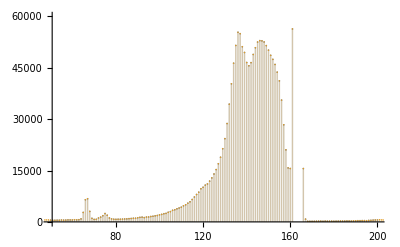

```mathematica
bkgdata=thickdata[1];
viewingdata=thickdata[1][[50;;200]];
ListPlot[{viewingdata,bkgdata},Filling->Bottom,PlotRange->{{50,200},{0,60000}}]
```

| Estimate | Standard Error | t-Statistic | P-Value
mu1 | 132.567 | 0.289499 | 457.918 | 2.5599196377×10^-5831
mu2 | 136.344 | 0.0523468 | 2604.62 | 7.9901380679×10^-11939
mu3 | 145.638 | 0.0843972 | 1725.63 | 1.5976895903×10^-10479
mu4 | 153.396 | 0.128055 | 1197.89 | 1.9235808759×10^-9188
mu5 | 163.274 | 0.000384742 | 424372. | 3.143454421×10^-30024
sigma1 | 14.7119 | 0.133034 | 110.588 | 1.5702283919×10^-1626
sigma2 | 3.7905 | 0.0416837 | 90.9348 | 2.2825182529×10^-1243
sigma3 | 3.47099 | 0.089239 | 38.8954 | 8.54406×10^-304
sigma4 | 3.95452 | 0.0731104 | 54.0897 | 1.384152192×10^-545
sigma5 | 1.00183 | 0.000427763 | 2342.03 | 6.1270961931×10^-11562
a1 | 14989.7 | 207.461 | 72.253 | 2.8444330675×10^-879
a2 | 38606.2 | 358.532 | 107.678 | 2.1473621646×10^-1570
a3 | 36015.5 | 841.369 | 42.8059 | 1.9808960915×10^-361
a4 | 37305.6 | 733.166 | 50.8828 | 6.7759633544×10^-491
a5 | 613822. | 209.204 | 2934.09 | 2.3431057037×10^-12361

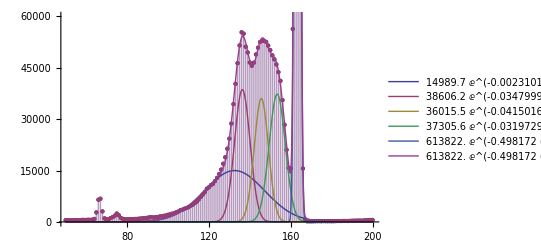

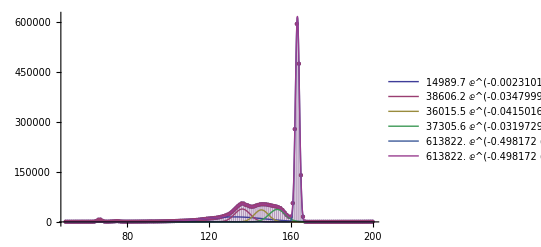

```mathematica
mu={131.6,136.3,145.6,153.3,163.2};sigma={14.6,3.8,3.4,4.0,1.0};
a={15000,30000,10800,30000,730000};n=Length[mu];

model=NonlinearModelFit[bkgdata,G[x,Table[Symbol["mu"<>ToString[i]],{i,1,n}],Table[Symbol["sigma"<>ToString[i]],{i,1,n}],Table[Symbol["a"<>ToString[i]],{i,1,n}]],Join[Table[{Symbol["mu"<>ToString[i]],mu[[i]]},{i,1,n}],Table[{Symbol["sigma"<>ToString[i]],sigma[[i]]},{i,1,n}],Table[{Symbol["a"<>ToString[i]],a[[i]]},{i,1,n}]],x];
model["ParameterTable"]
params=model["BestFitParameters"];
paramerrors=model["ParameterErrors"];

theme="Classic";
Show[ListPlot[{viewingdata,bkgdata[[50;;200]]},Filling->Bottom,PlotTheme->theme,PlotRange->All],Plot[Evaluate@Join[Table[F[x,params[[i,2]],params[[i+n,2]],params[[i+2n,2]]],{i,1,n}],{G[x,params[[;;n,2]],params[[n+1;;2n,2]],params[[2n+1;;3n,2]]]}],{x,50,200},PlotRange->All,PlotTheme->theme,PlotLegends->"Expressions"],PlotRange->{{50,200},{0,60000}}]
Show[ListPlot[{viewingdata,bkgdata[[50;;200]]},Filling->Bottom,PlotTheme->theme,PlotRange->All],Plot[Evaluate@Join[Table[F[x,params[[i,2]],params[[i+n,2]],params[[i+2n,2]]],{i,1,n}],{G[x,params[[;;n,2]],params[[n+1;;2n,2]],params[[2n+1;;3n,2]]]}],{x,50,200},PlotRange->All,PlotTheme->theme,PlotLegends->"Expressions"],PlotRange->{{50,200},All}]
```

### Conclusion

```mathematica
Table[{params[[i,2]],paramerrors[[i]],100*paramerrors[[i]]/params[[i,2]]},{i,{5,10,15}}]//TableForm
background=Table[err[F2,{i[[1]],0},{params[[5,2]],paramerrors[[5]]},{params[[10,2]],paramerrors[[10]]},{params[[15,2]],paramerrors[[15]]}],{i,bkgdata}];
counts[3]=Total[background[[All,1]]];countserror[3]=Sqrt[Total[(background[[All,2]])^2]];{counts[3],countserror[3],100countserror[3]/counts[3]}
```

163.274 | 0.000384742 | 0.000235642
1.00183 | 0.000427763 | 0.042698
613822. | 209.204 | 0.0340821

{1.54145×10^6,467.356,0.0303193}

```mathematica
peakbackground=Apply[err,Join[{backgroundfunction,{params[[5,2]],paramerrors[[5]]}},Table[{params[[i,2]],paramerrors[[i]]},{i,1,4}],Table[{params[[i+5,2]],paramerrors[[i]]},{i,1,4}],Table[{params[[i+10,2]],paramerrors[[i]]},{i,1,4}]]]
countsalt[3]=NIntegrate[F2[x,params[[5,2]],params[[5+5,2]],params[[5+10,2]]],{x,params[[5,2]]-2*fwhm[params[[5+5,2]]],params[[5,2]]+2*fwhm[params[[5+5,2]]]}];
countserroralt[3]=Sqrt[paramerrors[[-1]]^2+peakbackground[[2]]^2];
{countsalt[3],countserroralt[3],100*countserroralt[3]/countsalt[3]}
```

{3345.72,393.295}

{1.54144×10^6,445.474,0.0288998}

## Thin Film

### Data Selection

```mathematica
ListPlot[thindata[1][[100;;200]],Filling->Bottom,PlotRange->All]
```

-Graphics-

### NonlinearModelFit bins

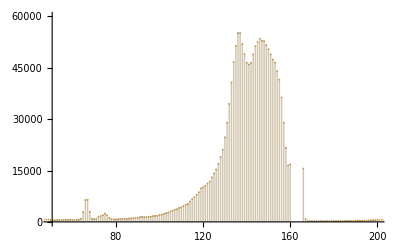

```mathematica
bkgdata=thindata[1];
viewingdata=thindata[1][[50;;200]];
ListPlot[{viewingdata,bkgdata},Filling->Bottom,PlotRange->{{50,200},{0,60000}}]
```

| Estimate | Standard Error | t-Statistic | P-Value
mu1 | 132.357 | 0.314139 | 421.333 | 1.1780667501×10^-5547
mu2 | 136.363 | 0.0519199 | 2626.4 | 2.3286801334×10^-11968
mu3 | 145.596 | 0.0802668 | 1813.9 | 3.0890548302×10^-10656
mu4 | 153.366 | 0.125575 | 1221.31 | 8.0854905296×10^-9257
mu5 | 163.254 | 0.000361107 | 452093. | 6.1428921269×10^-30249
sigma1 | 14.5896 | 0.143402 | 101.739 | 5.1552212312×10^-1455
sigma2 | 3.82961 | 0.0423918 | 90.3385 | 1.1712674511×10^-1231
sigma3 | 3.41795 | 0.0843133 | 40.5387 | 1.4324275522×10^-327
sigma4 | 4.05315 | 0.0746365 | 54.3052 | 2.56058253×10^-549
sigma5 | 1.00331 | 0.00040237 | 2493.5 | 3.4500262315×10^-11784
a1 | 14857.3 | 217.302 | 68.3719 | 2.0836762019×10^-805
a2 | 38968.1 | 368.284 | 105.81 | 3.365732867×10^-1534
a3 | 35627.4 | 879.468 | 40.5102 | 3.7597389653×10^-327
a4 | 38185.9 | 695.703 | 54.8882 | 1.8831158949×10^-559
a5 | 665613. | 212.963 | 3125.49 | 1.4392773582×10^-12585

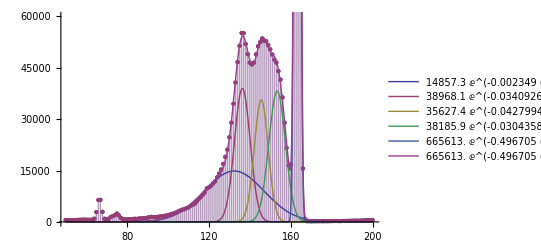

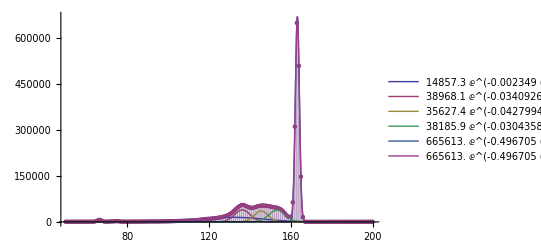

```mathematica
mu={131.6,136.3,145.6,153.3,163.2};sigma={14.6,3.8,3.4,4.0,1.0};
a={15000,30000,10800,30000,730000};n=Length[mu];

model=NonlinearModelFit[bkgdata,G[x,Table[Symbol["mu"<>ToString[i]],{i,1,n}],Table[Symbol["sigma"<>ToString[i]],{i,1,n}],Table[Symbol["a"<>ToString[i]],{i,1,n}]],Join[Table[{Symbol["mu"<>ToString[i]],mu[[i]]},{i,1,n}],Table[{Symbol["sigma"<>ToString[i]],sigma[[i]]},{i,1,n}],Table[{Symbol["a"<>ToString[i]],a[[i]]},{i,1,n}]],x];
model["ParameterTable"]
params=model["BestFitParameters"];
paramerrors=model["ParameterErrors"];

theme="Classic";
Show[ListPlot[{viewingdata,bkgdata[[50;;200]]},Filling->Bottom,PlotTheme->theme,PlotRange->All],Plot[Evaluate@Join[Table[F[x,params[[i,2]],params[[i+n,2]],params[[i+2n,2]]],{i,1,n}],{G[x,params[[;;n,2]],params[[n+1;;2n,2]],params[[2n+1;;3n,2]]]}],{x,50,200},PlotRange->All,PlotTheme->theme,PlotLegends->"Expressions"],PlotRange->{{50,200},{0,60000}}]
Show[ListPlot[{viewingdata,bkgdata[[50;;200]]},Filling->Bottom,PlotTheme->theme,PlotRange->All],Plot[Evaluate@Join[Table[F[x,params[[i,2]],params[[i+n,2]],params[[i+2n,2]]],{i,1,n}],{G[x,params[[;;n,2]],params[[n+1;;2n,2]],params[[2n+1;;3n,2]]]}],{x,50,200},PlotRange->All,PlotTheme->theme,PlotLegends->"Expressions"],PlotRange->{{50,200},All}]
```

### Conclusion

```mathematica
Table[{params[[i,2]],paramerrors[[i]],100*paramerrors[[i]]/params[[i,2]]},{i,{5,10,15}}]//TableForm
background=Table[err[F2,{i[[1]],0},{params[[5,2]],paramerrors[[5]]},{params[[10,2]],paramerrors[[10]]},{params[[15,2]],paramerrors[[15]]}],{i,bkgdata}];
counts[4]=Total[background[[All,1]]];countserror[4]=Sqrt[Total[(background[[All,2]])^2]];{counts[4],countserror[4],100countserror[4]/counts[4]}
```

163.254 | 0.000361107 | 0.000221193
1.00331 | 0.00040237 | 0.0401042
665613. | 212.963 | 0.031995

{1.67397×10^6,476.133,0.0284433}

```mathematica
peakbackground=Apply[err,Join[{backgroundfunction,{params[[5,2]],paramerrors[[5]]}},Table[{params[[i,2]],paramerrors[[i]]},{i,1,4}],Table[{params[[i+5,2]],paramerrors[[i]]},{i,1,4}],Table[{params[[i+10,2]],paramerrors[[i]]},{i,1,4}]]]
countsalt[4]=NIntegrate[F2[x,params[[5,2]],params[[5+5,2]],params[[5+10,2]]],{x,params[[5,2]]-2*fwhm[params[[5+5,2]]],params[[5,2]]+2*fwhm[params[[5+5,2]]]}];
countserroralt[4]=Sqrt[paramerrors[[-1]]^2+peakbackground[[2]]^2];
{countsalt[4],countserroralt[4],100*countserroralt[4]/countsalt[4]}
```

{3525.96,423.171}

{1.67397×10^6,473.738,0.0283003}

## Calculations

```mathematica
thickness=40;thicknesserror=0.01;
Print["Peak Data\n",Table[{counts[i],countserror[i],100*countserror[i]/counts[i]},{i,1,4}]//TableForm,"\n"]
coeff[counts1_,counts3_,thickness_]:=(-Log[counts3/counts1])/thickness;


attencoeff=err[coeff,{counts[1],countserror[1]},{counts[3],countserror[3]},{thickness,thicknesserror}];
thinmeasure=err[coeff,{counts[1],countserror[1]},{counts[4],countserror[4]},attencoeff];Join[thinmeasure,{100*thinmeasure[[2]]/thinmeasure[[1]]}]

attencoeff=err[coeff,{counts[2],countserror[2]},{counts[3],countserror[3]},{thickness,thicknesserror}];
thinmeasure=err[coeff,{counts[2],countserror[2]},{counts[4],countserror[4]},attencoeff];Join[thinmeasure,{100*thinmeasure[[2]]/thinmeasure[[1]]}]

thick[counts1_,counts2_,counts3_,thickness_]:=thickness Log[counts3/counts1]/Log[counts2/counts1]
thinmeasure=err[thick,{counts[1],countserror[1]},{counts[3],countserror[3]},{counts[4],countserror[4]},{thickness,thicknesserror}];
Join[thinmeasure,{100*thinmeasure[[2]]/thinmeasure[[1]]}]

thinmeasure=err[thick,{counts[2],countserror[2]},{counts[3],countserror[3]},{counts[4],countserror[4]},{thickness,thicknesserror}];
Join[thinmeasure,{100*thinmeasure[[2]]/thinmeasure[[1]]}]
```

Peak Data
1.686×10^6 | 479.158 | 0.0284198
1.69084×10^6 | 480.304 | 0.0284062
1.54145×10^6 | 467.356 | 0.0303193
1.67397×10^6 | 476.133 | 0.0284433

{3.19556,0.180036,5.63395}

{4.33633,0.174912,4.03365}

{3.19556,0.172752,5.40601}

{4.33633,0.165297,3.81192}

```mathematica
thickness=40;thicknesserror=0.01;
Print["Peak Data\n",Table[{countsalt[i],countserroralt[i],100*countserroralt[i]/countsalt[i]},{i,1,4}]//TableForm,"\n"]
coeff[counts1_,counts3_,thickness_]:=(-Log[counts3/counts1])/thickness;


attencoeff=err[coeff,{countsalt[1],countserroralt[1]},{countsalt[3],countserroralt[3]},{thickness,thicknesserror}];
thinmeasure=err[coeff,{countsalt[1],countserroralt[1]},{countsalt[4],countserroralt[4]},attencoeff];Join[thinmeasure,{100*thinmeasure[[2]]/thinmeasure[[1]]}]

attencoeff=err[coeff,{countsalt[2],countserroralt[2]},{countsalt[3],countserroralt[3]},{thickness,thicknesserror}];
thinmeasure=err[coeff,{countsalt[2],countserroralt[2]},{countsalt[4],countserroralt[4]},attencoeff];Join[thinmeasure,{100*thinmeasure[[2]]/thinmeasure[[1]]}]

thick[counts1_,counts2_,counts3_,thickness_]:=thickness Log[counts3/counts1]/Log[counts2/counts1]
thinmeasure=err[thick,{countsalt[1],countserroralt[1]},{countsalt[3],countserroralt[3]},{countsalt[4],countserroralt[4]},{thickness,thicknesserror}];
Join[thinmeasure,{100*thinmeasure[[2]]/thinmeasure[[1]]}]

thinmeasure=err[thick,{countsalt[2],countserroralt[2]},{countsalt[3],countserroralt[3]},{countsalt[4],countserroralt[4]},{thickness,thicknesserror}];
Join[thinmeasure,{100*thinmeasure[[2]]/thinmeasure[[1]]}]
```

Peak Data
1.686×10^6 | 491.996 | 0.0291813
1.69084×10^6 | 467.761 | 0.0276645
1.54144×10^6 | 445.474 | 0.0288998
1.67397×10^6 | 473.738 | 0.0283003

{3.19556,0.181989,5.69504}

{4.33633,0.172155,3.97007}

{3.19556,0.174386,5.45714}

{4.33633,0.162895,3.75652}

```mathematica
thickness=40;thicknesserror=0.01;theoerror=250;
100*theoerror/counts[1]
attencoeff=err[coeff,{counts[1],theoerror},{counts[3],theoerror},{thickness,thicknesserror}];
thinmeasure=err[coeff,{counts[1],theoerror},{counts[4],theoerror},attencoeff];Join[thinmeasure,{100*thinmeasure[[2]]/thinmeasure[[1]]}]
```

0.014828

{3.19556,0.094242,2.94915}

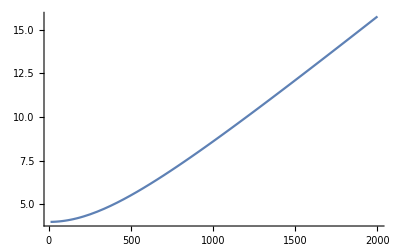

```mathematica
Plot[100*err[thick,{counts[1],x},{counts[3],countserror[3]},{counts[4],countserror[4]},{thickness,thicknesserror}][[2]]/err[thick,{counts[1],x},{counts[3],countserror[3]},{counts[4],countserror[4]},{thickness,thicknesserror}][[1]],{x,10,2000}]
```

# Data Set 2

```mathematica
ClearAll["Global`*"]
(*~ MacOS ~*)
main="/Users/mikhailgaerlan/Box Sync/Education/MSU/Research/Radiation Thickness/Data";

SetDirectory[main];
$Line=0;
```

## Data Import

## Source 1-Hour

### Trial 1

$SPEC_ID:
No sample description was entered.
$SPEC_REM:
DET# 1
DETDESC# HPGe Detector 1
AP# GammaVision Version 6.07
$DATE_MEA:
10/23/2015 08:25:16
$MEAS_TIM:
3600 3737
$DATA:
0 8191
       0
       0
       0

0
       0
$ROI:
0
$PRESETS:
Live Time
3600
0
$ENER_FIT:
0.137869 0.366631
$MCA_CAL:
3
1.378689E-001 3.666307E-001 -4.415950E-008 keV
$SHAPE_CAL:
3
2.301834E+000 9.195991E-004 -5.357180E-008

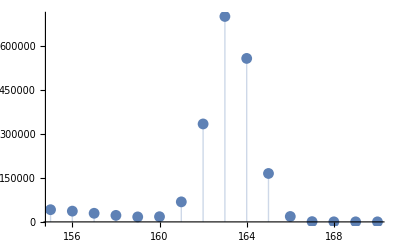

```mathematica
imported=Import["Am-241-1hr-10232015.Spe","Data"];
times=ToExpression[StringSplit[imported[[10]]]];
deadtime=N[Abs[times[[1]]-times[[2]]]/times[[2]]];
imported[[;;15]]//TableForm
imported[[-16;;]]//TableForm
freq=ToExpression[imported[[13;;-15]]]/(1-deadtime);
sourcedata[1]=Table[{i,freq[[i]]},{i,Length[freq]}];
ListPlot[sourcedata[1][[155;;170]],PlotRange->All,Filling->Bottom]
```

### Trial 2

$SPEC_ID:
No sample description was entered.
$SPEC_REM:
DET# 1
DETDESC# HPGe Detector 1
AP# GammaVision Version 6.07
$DATE_MEA:
10/23/2015 14:45:42
$MEAS_TIM:
3600 3738
$DATA:
0 8191
       0
       0
       0

0
       0
$ROI:
0
$PRESETS:
Live Time
3600
0
$ENER_FIT:
0.137869 0.366631
$MCA_CAL:
3
1.378689E-001 3.666307E-001 -4.415950E-008 keV
$SHAPE_CAL:
3
2.301834E+000 9.195991E-004 -5.357180E-008

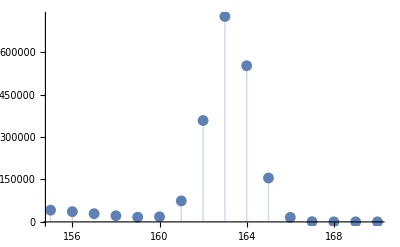

```mathematica
imported=Import["Am-241-1hrTrial2-10232015.Spe","Data"];
times=ToExpression[StringSplit[imported[[10]]]];
deadtime=N[Abs[times[[1]]-times[[2]]]/times[[2]]];
imported[[;;15]]//TableForm
imported[[-16;;]]//TableForm
freq=ToExpression[imported[[13;;-15]]]/(1-deadtime);
sourcedata[2]=Table[{i,freq[[i]]},{i,Length[freq]}];
ListPlot[sourcedata[2][[155;;170]],PlotRange->All,Filling->Bottom]
```

## Thick Film

$SPEC_ID:
Molnar Range
$SPEC_REM:
DET# 1
DETDESC# HPGe Detector 1
AP# GammaVision Version 6.07
$DATE_MEA:
10/23/2015 10:20:33
$MEAS_TIM:
3600 3730
$DATA:
0 8191
       0
       0
       0

0
       0
$ROI:
0
$PRESETS:
Live Time
3600
0
$ENER_FIT:
0.137869 0.366631
$MCA_CAL:
3
1.378689E-001 3.666307E-001 -4.415950E-008 keV
$SHAPE_CAL:
3
2.301834E+000 9.195991E-004 -5.357180E-008

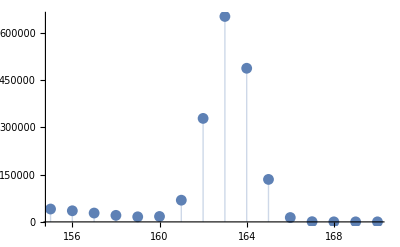

```mathematica
imported=Import["Am-241-ThickFilm-1hr-10232015.Spe","Data"];
times=ToExpression[StringSplit[imported[[10]]]];
deadtime=N[Abs[times[[1]]-times[[2]]]/times[[2]]];
imported[[;;15]]//TableForm
imported[[-16;;]]//TableForm
freq=ToExpression[imported[[13;;-15]]]/(1-deadtime);
thickdata[1]=Table[{i,freq[[i]]},{i,Length[freq]}];
ListPlot[thickdata[1][[155;;170]],PlotRange->All,Filling->Bottom]
```

## Thin Film

$SPEC_ID:
No sample description was entered.
$SPEC_REM:
DET# 1
DETDESC# HPGe Detector 1
AP# GammaVision Version 6.07
$DATE_MEA:
10/23/2015 13:27:38
$MEAS_TIM:
3600 3737
$DATA:
0 8191
       0
       0
       0

1
       1
$ROI:
0
$PRESETS:
Live Time
3600
0
$ENER_FIT:
0.137869 0.366631
$MCA_CAL:
3
1.378689E-001 3.666307E-001 -4.415950E-008 keV
$SHAPE_CAL:
3
2.301834E+000 9.195991E-004 -5.357180E-008

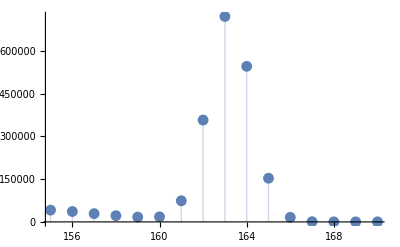

```mathematica
imported=Import["Am-241-ThinFilm-1hr-10232015.Spe","Data"];
times=ToExpression[StringSplit[imported[[10]]]];
deadtime=N[Abs[times[[1]]-times[[2]]]/times[[2]]];
imported[[;;15]]//TableForm
imported[[-16;;]]//TableForm
freq=ToExpression[imported[[13;;-15]]]/(1-deadtime);
thindata[1]=Table[{i,freq[[i]]},{i,Length[freq]}];
ListPlot[thindata[1][[155;;170]],PlotRange->All,Filling->Bottom]
```

## Data Analysis

## Equations

```mathematica
F[x_,mu_,sigma_,a_]:=a*Exp[-1/2*((x-mu)/sigma)^2]
F2[x_,mu_,sigma_,a_]:=a*Exp[-1/2*((x-mu)/sigma)^2]
G[x_,mu_,sigma_,a_]:=Sum[F[x,mu[[i]],sigma[[i]],a[[i]]],{i,1,Length[mu]}]

chisq2[data_,mu_,sigma_,a_]:=Sum[(data[[i,2]]-G[data[[i,1]],mu,sigma,a])^2,{i,Length[data]}]
backgroundfunction[x_,mu1_,mu2_,mu3_,mu4_,sigma1_,sigma2_,sigma3_,sigma4_,a1_,a2_,a3_,a4_]:=F2[x,mu1,sigma1,a1]+F2[x,mu2,sigma2,a2]+F2[x,mu3,sigma3,a3]+F2[x,mu4,sigma4,a4];
fwhm[sigma_]:=2*sigma*Sqrt[2*Log[2]];

err[F_,w__]:={F[Map[First,List[w]]/.List->Sequence],Block[{parms=Table[Unique[],{x,1,Length[List[w]]}],values=Table[List[w][[i,1]],{i,1,Length[List[w]]}],errors=Table[List[w][[i,2]],{i,1,Length[List[w]]}]},Sqrt[Total[Table[(D[F[parms/.List->Sequence],parms[[i]]]*errors[[i]])^2,{i,1,Length[values]}]/.Table[parms[[i]]->values[[i]],{i,1,Length[values]}]]]]}
```

## Source 1-hr Trial 1

### Data Selection

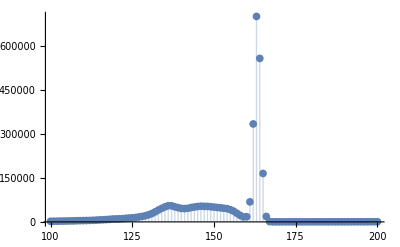

```mathematica
ListPlot[sourcedata[1][[100;;200]],Filling->Bottom,PlotRange->All]
```

### NonlinearModelFit bins

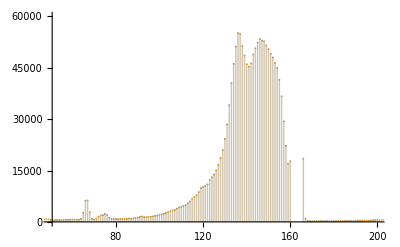

```mathematica
bkgdata=sourcedata[1];
viewingdata=sourcedata[1][[50;;200]];
ListPlot[{viewingdata,bkgdata},Filling->Bottom,PlotRange->{{50,200},{0,60000}}]
```

| Estimate | Standard Error | t-Statistic | P-Value
mu1 | 132.325 | 0.311606 | 424.656 | 2.49075856×10^-5574
mu2 | 136.341 | 0.0501012 | 2721.32 | 2.7575283688×10^-12094
mu3 | 145.433 | 0.0758912 | 1916.33 | 7.4362538356×10^-10851
mu4 | 153.215 | 0.122267 | 1253.11 | 1.2406745558×10^-9347
mu5 | 163.266 | 0.000337341 | 483979. | 5.7052467981×10^-30491
sigma1 | 14.7342 | 0.143713 | 102.526 | 2.4032088848×10^-1470
sigma2 | 3.77026 | 0.041302 | 91.2852 | 3.0005291906×10^-1250
sigma3 | 3.35809 | 0.0809329 | 41.4922 | 1.1513651072×10^-341
sigma4 | 4.1863 | 0.0753397 | 55.5657 | 2.725542258×10^-571
sigma5 | 1.00781 | 0.000377012 | 2673.15 | 6.0238053359×10^-12031
a1 | 14758.9 | 210.22 | 70.207 | 3.3059231826×10^-840
a2 | 38894. | 354.781 | 109.628 | 4.8093011953×10^-1608
a3 | 34387.8 | 906.595 | 37.9307 | 3.74639×10^-290
a4 | 39080.5 | 641.455 | 60.9248 | 4.2955318573×10^-667
a5 | 720758. | 214.863 | 3354.49 | 1.7534546246×10^-12836

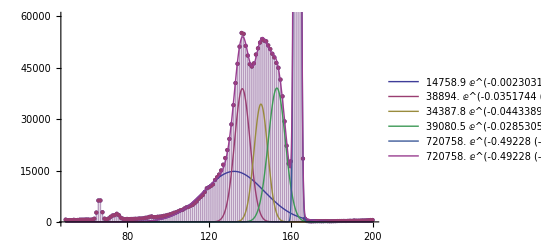

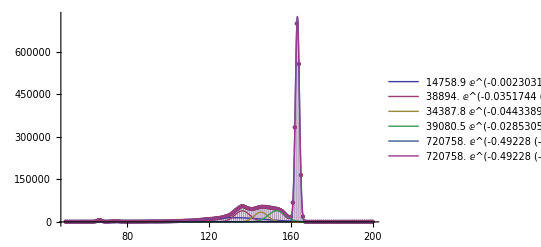

```mathematica
mu={131.6,135.3,144.6,152.5,162.3};sigma={14.2,3.6,3.6,4.0,1.0};
a={15000,30000,10800,30000,730000};n=Length[mu];

model=NonlinearModelFit[bkgdata,G[x,Table[Symbol["mu"<>ToString[i]],{i,1,n}],Table[Symbol["sigma"<>ToString[i]],{i,1,n}],Table[Symbol["a"<>ToString[i]],{i,1,n}]],Join[Table[{Symbol["mu"<>ToString[i]],mu[[i]]},{i,1,n}],Table[{Symbol["sigma"<>ToString[i]],sigma[[i]]},{i,1,n}],Table[{Symbol["a"<>ToString[i]],a[[i]]},{i,1,n}]],x];
model["ParameterTable"]
params=model["BestFitParameters"];
paramerrors=model["ParameterErrors"];

theme="Classic";
Show[ListPlot[{viewingdata,bkgdata[[50;;200]]},Filling->Bottom,PlotTheme->theme,PlotRange->All],Plot[Evaluate@Join[Table[F[x,params[[i,2]],params[[i+n,2]],params[[i+2n,2]]],{i,1,n}],{G[x,params[[;;n,2]],params[[n+1;;2n,2]],params[[2n+1;;3n,2]]]}],{x,50,200},PlotRange->All,PlotTheme->theme,PlotLegends->"Expressions"],PlotRange->{{50,200},{0,60000}}]
Show[ListPlot[{viewingdata,bkgdata[[50;;200]]},Filling->Bottom,PlotTheme->theme,PlotRange->All],Plot[Evaluate@Join[Table[F[x,params[[i,2]],params[[i+n,2]],params[[i+2n,2]]],{i,1,n}],{G[x,params[[;;n,2]],params[[n+1;;2n,2]],params[[2n+1;;3n,2]]]}],{x,50,200},PlotRange->All,PlotTheme->theme,PlotLegends->"Expressions"],PlotRange->{{50,200},All}]
```

### Conclusion

```mathematica
Table[{params[[i,2]],paramerrors[[i]],100*paramerrors[[i]]/params[[i,2]]},{i,{5,10,15}}]//TableForm
background=Table[err[F2,{i[[1]],0},{params[[5,2]],paramerrors[[5]]},{params[[10,2]],paramerrors[[10]]},{params[[15,2]],paramerrors[[15]]}],{i,bkgdata}];
counts[1]=Total[background[[All,1]]];countserror[1]=Sqrt[Total[(background[[All,2]])^2]];{counts[1],countserror[1],100countserror[1]/counts[1]}
```

163.266 | 0.000337341 | 0.00020662
1.00781 | 0.000377012 | 0.037409
720758. | 214.863 | 0.0298108

{1.82078×10^6,481.43,0.0264408}

```mathematica
peakbackground=Apply[err,Join[{backgroundfunction,{params[[5,2]],paramerrors[[5]]}},Table[{params[[i,2]],paramerrors[[i]]},{i,1,4}],Table[{params[[i+5,2]],paramerrors[[i]]},{i,1,4}],Table[{params[[i+10,2]],paramerrors[[i]]},{i,1,4}]]]
countsalt[1]=NIntegrate[F2[x,params[[5,2]],params[[5+5,2]],params[[5+10,2]]],{x,params[[5,2]]-2*fwhm[params[[5+5,2]]],params[[5,2]]+2*fwhm[params[[5+5,2]]]}];
countserroralt[1]=Sqrt[paramerrors[[-1]]^2+peakbackground[[2]]^2];
{countsalt[1],countserroralt[1],100*countserroralt[1]/countsalt[1]}
```

{3816.27,433.153}

{1.82078×10^6,483.516,0.0265554}

## Source 1-hr Trial 2

### Data Selection

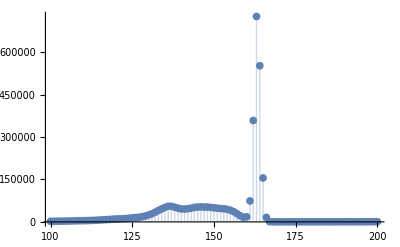

```mathematica
ListPlot[sourcedata[2][[100;;200]],Filling->Bottom,PlotRange->All]
```

### NonlinearModelFit bins

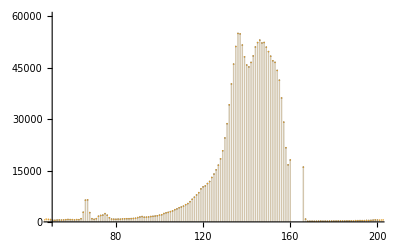

```mathematica
bkgdata=sourcedata[2];
viewingdata=sourcedata[2][[50;;200]];
ListPlot[{viewingdata,bkgdata},Filling->Bottom,PlotRange->{{50,200},{0,60000}}]
```

| Estimate | Standard Error | t-Statistic | P-Value
mu1 | 132.328 | 0.31915 | 414.626 | 3.2455766862×10^-5493
mu2 | 136.338 | 0.0495665 | 2750.62 | 2.8185134244×10^-12132
mu3 | 145.404 | 0.0716794 | 2028.53 | 1.7251550247×10^-11052
mu4 | 153.222 | 0.1157 | 1324.3 | 6.9881334603×10^-9543
mu5 | 163.222 | 0.000330486 | 493886. | 6.2804679267×10^-30563
sigma1 | 14.6262 | 0.146721 | 99.6867 | 6.0602162017×10^-1415
sigma2 | 3.76689 | 0.0414674 | 90.8398 | 1.6775355274×10^-1241
sigma3 | 3.32991 | 0.0778847 | 42.7544 | 1.1980176559×10^-360
sigma4 | 4.15329 | 0.0730367 | 56.8658 | 3.4342555656×10^-594
sigma5 | 1.00349 | 0.000367842 | 2728.06 | 4.5414442191×10^-12103
a1 | 14780.9 | 215.876 | 68.4695 | 2.9787707912×10^-807
a2 | 38862.8 | 357.896 | 108.587 | 5.9702256048×10^-1588
a3 | 34587.8 | 845.315 | 40.9171 | 3.8830711739×10^-333
a4 | 38839.4 | 610.338 | 63.6358 | 7.7471099013×10^-717
a5 | 740034. | 216.781 | 3413.73 | 1.3269240567×10^-12898

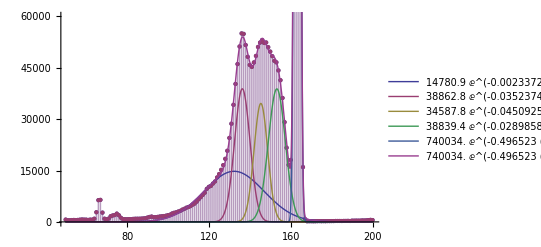

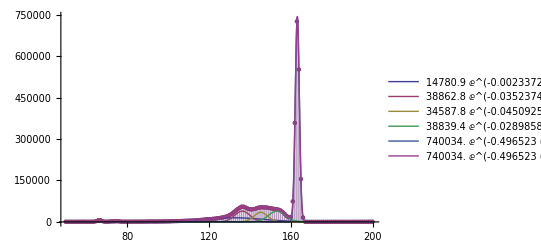

```mathematica
mu={131.6,135.3,144.6,152.5,162.3};sigma={14.2,3.6,3.6,4.0,1.0};
a={15000,30000,10800,30000,730000};n=Length[mu];

model=NonlinearModelFit[bkgdata,G[x,Table[Symbol["mu"<>ToString[i]],{i,1,n}],Table[Symbol["sigma"<>ToString[i]],{i,1,n}],Table[Symbol["a"<>ToString[i]],{i,1,n}]],Join[Table[{Symbol["mu"<>ToString[i]],mu[[i]]},{i,1,n}],Table[{Symbol["sigma"<>ToString[i]],sigma[[i]]},{i,1,n}],Table[{Symbol["a"<>ToString[i]],a[[i]]},{i,1,n}]],x];
model["ParameterTable"]
params=model["BestFitParameters"];
paramerrors=model["ParameterErrors"];

theme="Classic";
Show[ListPlot[{viewingdata,bkgdata[[50;;200]]},Filling->Bottom,PlotTheme->theme,PlotRange->All],Plot[Evaluate@Join[Table[F[x,params[[i,2]],params[[i+n,2]],params[[i+2n,2]]],{i,1,n}],{G[x,params[[;;n,2]],params[[n+1;;2n,2]],params[[2n+1;;3n,2]]]}],{x,50,200},PlotRange->All,PlotTheme->theme,PlotLegends->"Expressions"],PlotRange->{{50,200},{0,60000}}]
Show[ListPlot[{viewingdata,bkgdata[[50;;200]]},Filling->Bottom,PlotTheme->theme,PlotRange->All],Plot[Evaluate@Join[Table[F[x,params[[i,2]],params[[i+n,2]],params[[i+2n,2]]],{i,1,n}],{G[x,params[[;;n,2]],params[[n+1;;2n,2]],params[[2n+1;;3n,2]]]}],{x,50,200},PlotRange->All,PlotTheme->theme,PlotLegends->"Expressions"],PlotRange->{{50,200},All}]
```

### Conclusion

```mathematica
Table[{params[[i,2]],paramerrors[[i]],100*paramerrors[[i]]/params[[i,2]]},{i,{5,10,15}}]//TableForm
background=Table[err[F2,{i[[1]],0},{params[[5,2]],paramerrors[[5]]},{params[[10,2]],paramerrors[[10]]},{params[[15,2]],paramerrors[[15]]}],{i,bkgdata}];
counts[2]=Total[background[[All,1]]];countserror[2]=Sqrt[Total[(background[[All,2]])^2]];{counts[2],countserror[2],100countserror[2]/counts[2]}
```

163.222 | 0.000330486 | 0.000202476
1.00349 | 0.000367842 | 0.0366561
740034. | 216.781 | 0.0292934

{1.86147×10^6,484.47,0.0260261}

```mathematica
peakbackground=Apply[err,Join[{backgroundfunction,{params[[5,2]],paramerrors[[5]]}},Table[{params[[i,2]],paramerrors[[i]]},{i,1,4}],Table[{params[[i+5,2]],paramerrors[[i]]},{i,1,4}],Table[{params[[i+10,2]],paramerrors[[i]]},{i,1,4}]]]
countsalt[2]=NIntegrate[F2[x,params[[5,2]],params[[5+5,2]],params[[5+10,2]]],{x,params[[5,2]]-2*fwhm[params[[5+5,2]]],params[[5,2]]+2*fwhm[params[[5+5,2]]]}];
countserroralt[2]=Sqrt[paramerrors[[-1]]^2+peakbackground[[2]]^2];
{countsalt[2],countserroralt[2],100*countserroralt[2]/countsalt[2]}
```

{3727.81,411.445}

{1.86147×10^6,465.061,0.0249835}

## Thick Film

### Data Selection

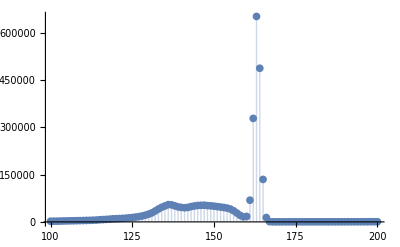

```mathematica
ListPlot[thickdata[1][[100;;200]],Filling->Bottom,PlotRange->All]
```

### NonlinearModelFit bins

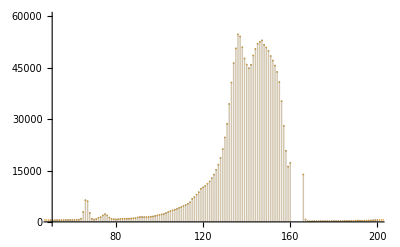

```mathematica
bkgdata=thickdata[1];
viewingdata=thickdata[1][[50;;200]];
ListPlot[{viewingdata,bkgdata},Filling->Bottom,PlotRange->{{50,200},{0,60000}}]
```

| Estimate | Standard Error | t-Statistic | P-Value
mu1 | 132.122 | 0.311185 | 424.577 | 1.0547903294×10^-5573
mu2 | 136.312 | 0.0494857 | 2754.57 | 2.2282756232×10^-12137
mu3 | 145.485 | 0.0750617 | 1938.21 | 4.4882124411×10^-10891
mu4 | 153.189 | 0.118701 | 1290.55 | 1.2555417506×10^-9451
mu5 | 163.204 | 0.000354701 | 460118. | 2.0211604638×10^-30311
sigma1 | 14.7209 | 0.143079 | 102.887 | 2.224411121×10^-1477
sigma2 | 3.85265 | 0.0412333 | 93.4353 | 1.8369288972×10^-1292
sigma3 | 3.35453 | 0.078195 | 42.8996 | 7.4347204102×10^-363
sigma4 | 4.08984 | 0.0718777 | 56.9001 | 8.4872871004×10^-595
sigma5 | 1.00465 | 0.000393432 | 2553.55 | 1.3913342094×10^-11868
a1 | 14455. | 206.03 | 70.1598 | 2.6051800718×10^-839
a2 | 38704.6 | 345.039 | 112.175 | 4.9710696568×10^-1657
a3 | 34668.2 | 864.519 | 40.1011 | 3.568450242×10^-321
a4 | 38342. | 638.379 | 60.0615 | 2.0155867133×10^-651
a5 | 661860. | 207.456 | 3190.37 | 1.7956237211×10^-12658

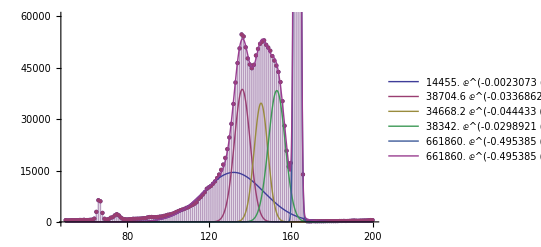

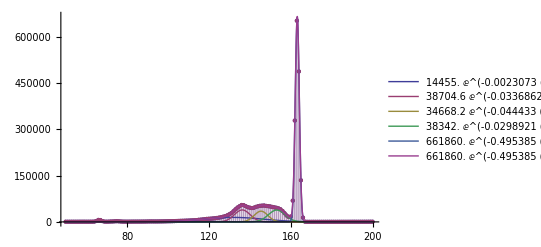

```mathematica
mu={131.6,135.3,144.6,152.5,162.3};sigma={14.2,3.6,3.6,4.0,1.0};
a={15000,30000,10800,30000,730000};n=Length[mu];

model=NonlinearModelFit[bkgdata,G[x,Table[Symbol["mu"<>ToString[i]],{i,1,n}],Table[Symbol["sigma"<>ToString[i]],{i,1,n}],Table[Symbol["a"<>ToString[i]],{i,1,n}]],Join[Table[{Symbol["mu"<>ToString[i]],mu[[i]]},{i,1,n}],Table[{Symbol["sigma"<>ToString[i]],sigma[[i]]},{i,1,n}],Table[{Symbol["a"<>ToString[i]],a[[i]]},{i,1,n}]],x];
model["ParameterTable"]
params=model["BestFitParameters"];
paramerrors=model["ParameterErrors"];

theme="Classic";
Show[ListPlot[{viewingdata,bkgdata[[50;;200]]},Filling->Bottom,PlotTheme->theme,PlotRange->All],Plot[Evaluate@Join[Table[F[x,params[[i,2]],params[[i+n,2]],params[[i+2n,2]]],{i,1,n}],{G[x,params[[;;n,2]],params[[n+1;;2n,2]],params[[2n+1;;3n,2]]]}],{x,50,200},PlotRange->All,PlotTheme->theme,PlotLegends->"Expressions"],PlotRange->{{50,200},{0,60000}}]
Show[ListPlot[{viewingdata,bkgdata[[50;;200]]},Filling->Bottom,PlotTheme->theme,PlotRange->All],Plot[Evaluate@Join[Table[F[x,params[[i,2]],params[[i+n,2]],params[[i+2n,2]]],{i,1,n}],{G[x,params[[;;n,2]],params[[n+1;;2n,2]],params[[2n+1;;3n,2]]]}],{x,50,200},PlotRange->All,PlotTheme->theme,PlotLegends->"Expressions"],PlotRange->{{50,200},All}]
```

### Conclusion

```mathematica
Table[{params[[i,2]],paramerrors[[i]],100*paramerrors[[i]]/params[[i,2]]},{i,{5,10,15}}]//TableForm
background=Table[err[F2,{i[[1]],0},{params[[5,2]],paramerrors[[5]]},{params[[10,2]],paramerrors[[10]]},{params[[15,2]],paramerrors[[15]]}],{i,bkgdata}];
counts[3]=Total[background[[All,1]]];countserror[3]=Sqrt[Total[(background[[All,2]])^2]];{counts[3],countserror[3],100countserror[3]/counts[3]}
```

163.204 | 0.000354701 | 0.000217336
1.00465 | 0.000393432 | 0.0391612
661860. | 207.456 | 0.0313443

{1.66675×10^6,463.871,0.0278309}

```mathematica
peakbackground=Apply[err,Join[{backgroundfunction,{params[[5,2]],paramerrors[[5]]}},Table[{params[[i,2]],paramerrors[[i]]},{i,1,4}],Table[{params[[i+5,2]],paramerrors[[i]]},{i,1,4}],Table[{params[[i+10,2]],paramerrors[[i]]},{i,1,4}]]]
countsalt[3]=NIntegrate[F2[x,params[[5,2]],params[[5+5,2]],params[[5+10,2]]],{x,params[[5,2]]-2*fwhm[params[[5+5,2]]],params[[5,2]]+2*fwhm[params[[5+5,2]]]}];
countserroralt[3]=Sqrt[paramerrors[[-1]]^2+peakbackground[[2]]^2];
{countsalt[3],countserroralt[3],100*countserroralt[3]/countsalt[3]}
```

{3467.38,394.323}

{1.66674×10^6,445.565,0.0267327}

## Thin Film

### Data Selection

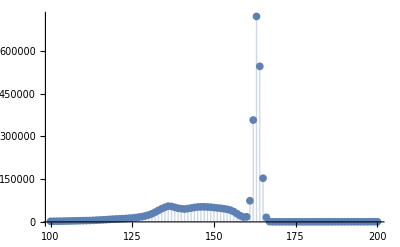

```mathematica
ListPlot[thindata[1][[100;;200]],Filling->Bottom,PlotRange->All]
```

### NonlinearModelFit bins

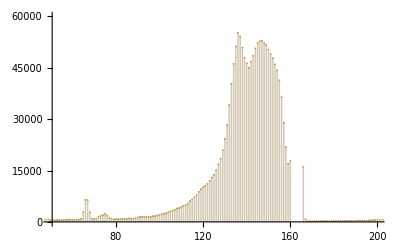

```mathematica
bkgdata=thindata[1];
viewingdata=thindata[1][[50;;200]];
ListPlot[{viewingdata,bkgdata},Filling->Bottom,PlotRange->{{50,200},{0,60000}}]
```

| Estimate | Standard Error | t-Statistic | P-Value
mu1 | 132.431 | 0.308195 | 429.698 | 1.8832320239×10^-5614
mu2 | 136.191 | 0.0564131 | 2414.17 | 1.5769648565×10^-11669
mu3 | 145.484 | 0.0961134 | 1513.67 | 1.4022134793×10^-10015
mu4 | 153.417 | 0.145826 | 1052.05 | 2.070908787×10^-8730
mu5 | 163.218 | 0.000332373 | 491070. | 1.2681049731×10^-30542
sigma1 | 14.652 | 0.14201 | 103.176 | 5.1506644783×10^-1483
sigma2 | 3.68385 | 0.0429249 | 85.821 | 5.5552395389×10^-1143
sigma3 | 3.57623 | 0.102798 | 34.7888 | 2.0236×10^-247
sigma4 | 4.06886 | 0.0821533 | 49.5277 | 2.6610956556×10^-468
sigma5 | 1.00396 | 0.000370352 | 2710.84 | 1.3396137664×10^-12080
a1 | 14896.2 | 212. | 70.2652 | 2.5773700475×10^-841
a2 | 37980.7 | 397.602 | 95.5244 | 1.892222136×10^-1333
a3 | 35883.6 | 931.477 | 38.5234 | 1.66312×10^-298
a4 | 37554.8 | 823.473 | 45.6054 | 7.972058268×10^-405
a5 | 733899. | 216.23 | 3394.07 | 4.2202696399×10^-12878

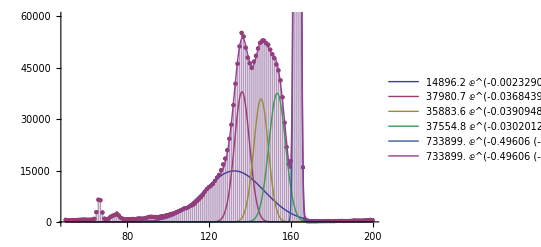

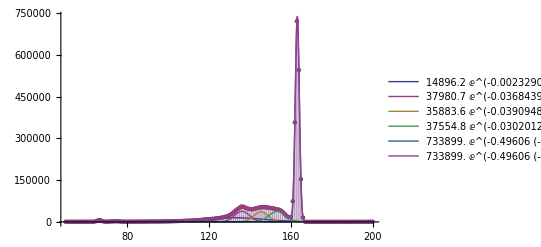

```mathematica
mu={131.6,135.3,144.6,152.5,162.3};sigma={14.2,3.6,3.6,4.0,1.0};
a={15000,30000,10800,30000,730000};n=Length[mu];

model=NonlinearModelFit[bkgdata,G[x,Table[Symbol["mu"<>ToString[i]],{i,1,n}],Table[Symbol["sigma"<>ToString[i]],{i,1,n}],Table[Symbol["a"<>ToString[i]],{i,1,n}]],Join[Table[{Symbol["mu"<>ToString[i]],mu[[i]]},{i,1,n}],Table[{Symbol["sigma"<>ToString[i]],sigma[[i]]},{i,1,n}],Table[{Symbol["a"<>ToString[i]],a[[i]]},{i,1,n}]],x];
model["ParameterTable"]
params=model["BestFitParameters"];
paramerrors=model["ParameterErrors"];

theme="Classic";
Show[ListPlot[{viewingdata,bkgdata[[50;;200]]},Filling->Bottom,PlotTheme->theme,PlotRange->All],Plot[Evaluate@Join[Table[F[x,params[[i,2]],params[[i+n,2]],params[[i+2n,2]]],{i,1,n}],{G[x,params[[;;n,2]],params[[n+1;;2n,2]],params[[2n+1;;3n,2]]]}],{x,50,200},PlotRange->All,PlotTheme->theme,PlotLegends->"Expressions"],PlotRange->{{50,200},{0,60000}}]
Show[ListPlot[{viewingdata,bkgdata[[50;;200]]},Filling->Bottom,PlotTheme->theme,PlotRange->All],Plot[Evaluate@Join[Table[F[x,params[[i,2]],params[[i+n,2]],params[[i+2n,2]]],{i,1,n}],{G[x,params[[;;n,2]],params[[n+1;;2n,2]],params[[2n+1;;3n,2]]]}],{x,50,200},PlotRange->All,PlotTheme->theme,PlotLegends->"Expressions"],PlotRange->{{50,200},All}]
```

### Conclusion

```mathematica
Table[{params[[i,2]],paramerrors[[i]],100*paramerrors[[i]]/params[[i,2]]},{i,{5,10,15}}]//TableForm
background=Table[err[F2,{i[[1]],0},{params[[5,2]],paramerrors[[5]]},{params[[10,2]],paramerrors[[10]]},{params[[15,2]],paramerrors[[15]]}],{i,bkgdata}];
counts[4]=Total[background[[All,1]]];countserror[4]=Sqrt[Total[(background[[All,2]])^2]];{counts[4],countserror[4],100countserror[4]/counts[4]}
```

163.218 | 0.000332373 | 0.000203637
1.00396 | 0.000370352 | 0.036889
733899. | 216.23 | 0.0294632

{1.8469×10^6,483.421,0.0261747}

```mathematica
peakbackground=Apply[err,Join[{backgroundfunction,{params[[5,2]],paramerrors[[5]]}},Table[{params[[i,2]],paramerrors[[i]]},{i,1,4}],Table[{params[[i+5,2]],paramerrors[[i]]},{i,1,4}],Table[{params[[i+10,2]],paramerrors[[i]]},{i,1,4}]]]
countsalt[4]=NIntegrate[F2[x,params[[5,2]],params[[5+5,2]],params[[5+10,2]]],{x,params[[5,2]]-2*fwhm[params[[5+5,2]]],params[[5,2]]+2*fwhm[params[[5+5,2]]]}];
countserroralt[4]=Sqrt[paramerrors[[-1]]^2+peakbackground[[2]]^2];
{countsalt[4],countserroralt[4],100*countserroralt[4]/countsalt[4]}
```

{3701.29,494.193}

{1.8469×10^6,539.428,0.0292072}

## Calculations

```mathematica
thickness=40;thicknesserror=0.01;
Print["Peak Data\n",Table[{counts[i],countserror[i],100*countserror[i]/counts[i]},{i,1,4}]//TableForm,"\n"]
coeff[counts1_,counts3_,thickness_]:=(-Log[counts3/counts1])/thickness;


attencoeff=err[coeff,{counts[1],countserror[1]},{counts[3],countserror[3]},{thickness,thicknesserror}]
thinmeasure=err[coeff,{counts[1],countserror[1]},{counts[4],countserror[4]},attencoeff];Join[thinmeasure,{100*thinmeasure[[2]]/thinmeasure[[1]]}]

attencoeff=err[coeff,{counts[2],countserror[2]},{counts[3],countserror[3]},{thickness,thicknesserror}]
thinmeasure=err[coeff,{counts[2],countserror[2]},{counts[4],countserror[4]},attencoeff];Join[thinmeasure,{100*thinmeasure[[2]]/thinmeasure[[1]]}]

thick[counts1_,counts2_,counts3_,thickness_]:=thickness Log[counts3/counts1]/Log[counts2/counts1]
thinmeasure=err[thick,{counts[1],countserror[1]},{counts[3],countserror[3]},{counts[4],countserror[4]},{thickness,thicknesserror}];
Join[thinmeasure,{100*thinmeasure[[2]]/thinmeasure[[1]]}]

thinmeasure=err[thick,{counts[2],countserror[2]},{counts[3],countserror[3]},{counts[4],countserror[4]},{thickness,thicknesserror}];
Join[thinmeasure,{100*thinmeasure[[2]]/thinmeasure[[1]]}]
```

Peak Data
1.82078×10^6 | 481.43 | 0.0264408
1.86147×10^6 | 484.47 | 0.0260261
1.66675×10^6 | 463.871 | 0.0278309
1.8469×10^6 | 483.421 | 0.0261747

{0.00220981,9.61301×10^-6}

{-6.44524,0.170683,-2.6482}

{0.00276233,9.55102×10^-6}

{2.84477,0.133987,4.70993}

{-6.44524,0.183702,-2.85019}

{2.84477,0.129189,4.54128}

```mathematica
thickness=40;thicknesserror=0.01;
Print["Peak Data\n",Table[{countsalt[i],countserroralt[i],100*countserroralt[i]/countsalt[i]},{i,1,4}]//TableForm,"\n"]
coeff[counts1_,counts3_,thickness_]:=(-Log[counts3/counts1])/thickness;


attencoeff=err[coeff,{countsalt[1],countserroralt[1]},{countsalt[3],countserroralt[3]},{thickness,thicknesserror}]
thinmeasure=err[coeff,{countsalt[1],countserroralt[1]},{countsalt[4],countserroralt[4]},attencoeff];Join[thinmeasure,{100*thinmeasure[[2]]/thinmeasure[[1]]}]

attencoeff=err[coeff,{countsalt[2],countserroralt[2]},{countsalt[3],countserroralt[3]},{thickness,thicknesserror}]
thinmeasure=err[coeff,{countsalt[2],countserroralt[2]},{countsalt[4],countserroralt[4]},attencoeff];Join[thinmeasure,{100*thinmeasure[[2]]/thinmeasure[[1]]}]

thick[counts1_,counts2_,counts3_,thickness_]:=thickness Log[counts3/counts1]/Log[counts2/counts1]
thinmeasure=err[thick,{countsalt[1],countserroralt[1]},{countsalt[3],countserroralt[3]},{countsalt[4],countserroralt[4]},{thickness,thicknesserror}];
Join[thinmeasure,{100*thinmeasure[[2]]/thinmeasure[[1]]}]

thinmeasure=err[thick,{countsalt[2],countserroralt[2]},{countsalt[3],countserroralt[3]},{countsalt[4],countserroralt[4]},{thickness,thicknesserror}];
Join[thinmeasure,{100*thinmeasure[[2]]/thinmeasure[[1]]}]
```

Peak Data
1.82078×10^6 | 483.516 | 0.0265554
1.86147×10^6 | 465.061 | 0.0249835
1.66674×10^6 | 445.565 | 0.0267327
1.8469×10^6 | 539.428 | 0.0292072

{0.00220981,9.43633×10^-6}

{-6.44524,0.180742,-2.80427}

{0.00276233,9.17348×10^-6}

{2.84477,0.139459,4.90231}

{-6.44524,0.193187,-2.99736}

{2.84477,0.135224,4.75341}

# Data Set 3

```mathematica
ClearAll["Global`*"]
(*~ MacOS ~*)
main="/Users/mikhailgaerlan/Box Sync/Education/MSU/Research/Radiation Thickness/Data";

SetDirectory[main];
$Line=0;
```

## Data Import

## Source 1-Hour

### Trial 1

$SPEC_ID:
No sample description was entered.
$SPEC_REM:
DET# 1
DETDESC# HPGe Detector 1
AP# GammaVision Version 6.07
$DATE_MEA:
10/28/2015 09:32:08
$MEAS_TIM:
3600 3743
$DATA:
0 8191
       0
       0
       0

0
       0
$ROI:
0
$PRESETS:
Live Time
3600
0
$ENER_FIT:
0.137869 0.366631
$MCA_CAL:
3
1.378689E-001 3.666307E-001 -4.415950E-008 keV
$SHAPE_CAL:
3
2.301834E+000 9.195991E-004 -5.357180E-008

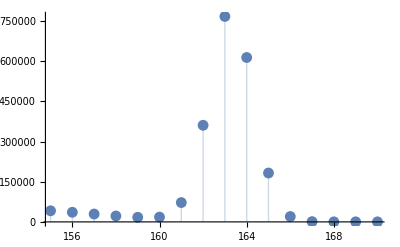

```mathematica
imported=Import["Am-241-1hr-10282015.Spe","Data"];
times=ToExpression[StringSplit[imported[[10]]]];
deadtime=N[Abs[times[[1]]-times[[2]]]/times[[2]]];
imported[[;;15]]//TableForm
imported[[-16;;]]//TableForm
freq=ToExpression[imported[[13;;-15]]]/(1-deadtime);
sourcedata[1]=Table[{i,freq[[i]]},{i,Length[freq]}];
ListPlot[sourcedata[1][[155;;170]],PlotRange->All,Filling->Bottom]
```

### Trial 2

$SPEC_ID:
No sample description was entered.
$SPEC_REM:
DET# 1
DETDESC# HPGe Detector 1
AP# GammaVision Version 6.07
$DATE_MEA:
10/28/2015 11:50:37
$MEAS_TIM:
3600 3743
$DATA:
0 8191
       0
       0
       0

0
       1
$ROI:
0
$PRESETS:
Live Time
3600
0
$ENER_FIT:
0.137869 0.366631
$MCA_CAL:
3
1.378689E-001 3.666307E-001 -4.415950E-008 keV
$SHAPE_CAL:
3
2.301834E+000 9.195991E-004 -5.357180E-008

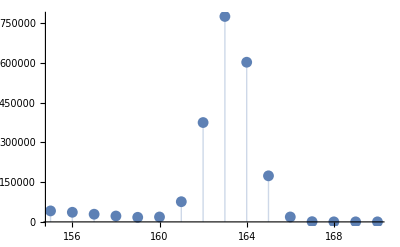

```mathematica
imported=Import["Am-241-1hrTrial2-10282015.Spe","Data"];
times=ToExpression[StringSplit[imported[[10]]]];
deadtime=N[Abs[times[[1]]-times[[2]]]/times[[2]]];
imported[[;;15]]//TableForm
imported[[-16;;]]//TableForm
freq=ToExpression[imported[[13;;-15]]]/(1-deadtime);
sourcedata[2]=Table[{i,freq[[i]]},{i,Length[freq]}];
ListPlot[sourcedata[2][[155;;170]],PlotRange->All,Filling->Bottom]
```

## Thick Film

```mathematica
imported=Import["Am-241-ThickFilm-1hr-10232015.Spe","Data"];
times=ToExpression[StringSplit[imported[[10]]]];
deadtime=N[Abs[times[[1]]-times[[2]]]/times[[2]]];
imported[[;;15]]//TableForm
imported[[-16;;]]//TableForm
freq=ToExpression[imported[[13;;-15]]]/(1-deadtime);
thickdata[1]=Table[{i,freq[[i]]},{i,Length[freq]}];
ListPlot[thickdata[1][[155;;170]],PlotRange->All,Filling->Bottom]
```

$SPEC_ID:
Molnar Range
$SPEC_REM:
DET# 1
DETDESC# HPGe Detector 1
AP# GammaVision Version 6.07
$DATE_MEA:
10/23/2015 10:20:33
$MEAS_TIM:
3600 3730
$DATA:
0 8191
       0
       0
       0

0
       0
$ROI:
0
$PRESETS:
Live Time
3600
0
$ENER_FIT:
0.137869 0.366631
$MCA_CAL:
3
1.378689E-001 3.666307E-001 -4.415950E-008 keV
$SHAPE_CAL:
3
2.301834E+000 9.195991E-004 -5.357180E-008

-Graphics-

## Thin Film

$SPEC_ID:
No sample description was entered.
$SPEC_REM:
DET# 1
DETDESC# HPGe Detector 1
AP# GammaVision Version 6.07
$DATE_MEA:
10/28/2015 08:28:34
$MEAS_TIM:
3600 3742
$DATA:
0 8191
       0
       0
       0

0
       0
$ROI:
0
$PRESETS:
Live Time
3600
0
$ENER_FIT:
0.137869 0.366631
$MCA_CAL:
3
1.378689E-001 3.666307E-001 -4.415950E-008 keV
$SHAPE_CAL:
3
2.301834E+000 9.195991E-004 -5.357180E-008

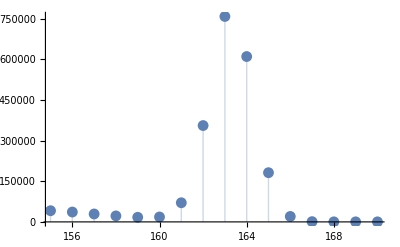

```mathematica
imported=Import["Am-241-ThinFilm-1hr-10282015.Spe","Data"];
times=ToExpression[StringSplit[imported[[10]]]];
deadtime=N[Abs[times[[1]]-times[[2]]]/times[[2]]];
imported[[;;15]]//TableForm
imported[[-16;;]]//TableForm
freq=ToExpression[imported[[13;;-15]]]/(1-deadtime);
thindata[1]=Table[{i,freq[[i]]},{i,Length[freq]}];
ListPlot[thindata[1][[155;;170]],PlotRange->All,Filling->Bottom]
```

## Data Analysis

## Equations

```mathematica
F[x_,mu_,sigma_,a_]:=a*Exp[-1/2*((x-mu)/sigma)^2]
F2[x_,mu_,sigma_,a_]:=a*Exp[-1/2*((x-mu)/sigma)^2]
G[x_,mu_,sigma_,a_]:=Sum[F[x,mu[[i]],sigma[[i]],a[[i]]],{i,1,Length[mu]}]

chisq2[data_,mu_,sigma_,a_]:=Sum[(data[[i,2]]-G[data[[i,1]],mu,sigma,a])^2,{i,Length[data]}]
backgroundfunction[x_,mu1_,mu2_,mu3_,mu4_,sigma1_,sigma2_,sigma3_,sigma4_,a1_,a2_,a3_,a4_]:=F2[x,mu1,sigma1,a1]+F2[x,mu2,sigma2,a2]+F2[x,mu3,sigma3,a3]+F2[x,mu4,sigma4,a4];
fwhm[sigma_]:=2*sigma*Sqrt[2*Log[2]];

err[F_,w__]:={F[Map[First,List[w]]/.List->Sequence],Block[{parms=Table[Unique[],{x,1,Length[List[w]]}],values=Table[List[w][[i,1]],{i,1,Length[List[w]]}],errors=Table[List[w][[i,2]],{i,1,Length[List[w]]}]},Sqrt[Total[Table[(D[F[parms/.List->Sequence],parms[[i]]]*errors[[i]])^2,{i,1,Length[values]}]/.Table[parms[[i]]->values[[i]],{i,1,Length[values]}]]]]}
```

## Source 1-hr Trial 1

### Data Selection

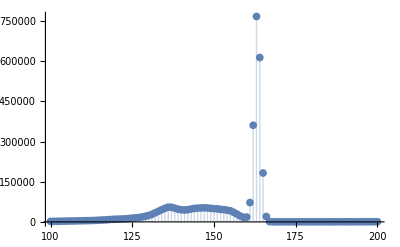

```mathematica
ListPlot[sourcedata[1][[100;;200]],Filling->Bottom,PlotRange->All]
```

### NonlinearModelFit bins

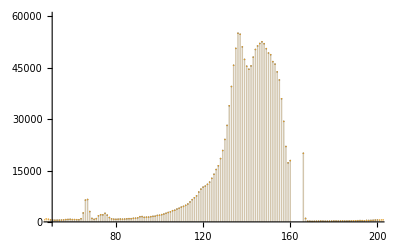

```mathematica
bkgdata=sourcedata[1];
viewingdata=sourcedata[1][[50;;200]];
ListPlot[{viewingdata,bkgdata},Filling->Bottom,PlotRange->{{50,200},{0,60000}}]
```

| Estimate | Standard Error | t-Statistic | P-Value
mu1 | 132.629 | 0.322789 | 410.883 | 1.7452760877×10^-5462
mu2 | 136.332 | 0.0499078 | 2731.68 | 9.0364545978×10^-12108
mu3 | 145.37 | 0.0766278 | 1897.1 | 4.1919692548×10^-10815
mu4 | 153.18 | 0.125939 | 1216.31 | 2.5253610338×10^-9242
mu5 | 163.274 | 0.000315201 | 518000. | 3.2720153124×10^-30732
sigma1 | 14.5314 | 0.147464 | 98.5418 | 1.4825870498×10^-1392
sigma2 | 3.70291 | 0.0419086 | 88.3568 | 9.6055467184×10^-1193
sigma3 | 3.33178 | 0.0824975 | 40.3864 | 2.438944407×10^-325
sigma4 | 4.25307 | 0.0795956 | 53.4334 | 2.9277965351×10^-534
sigma5 | 1.00494 | 0.000353532 | 2842.57 | 6.139126082×10^-12249
a1 | 15037.9 | 225.53 | 66.6778 | 1.6550497452×10^-773
a2 | 38269.6 | 365.732 | 104.638 | 1.8565701956×10^-1511
a3 | 33235.1 | 919.285 | 36.1532 | 1.19232×10^-265
a4 | 38486.9 | 638.372 | 60.2892 | 1.5140418894×10^-655
a5 | 792057. | 221.854 | 3570.17 | 1.2926070809×10^-13057

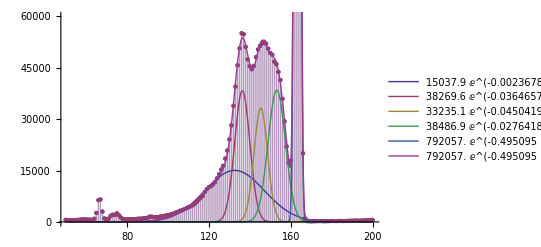

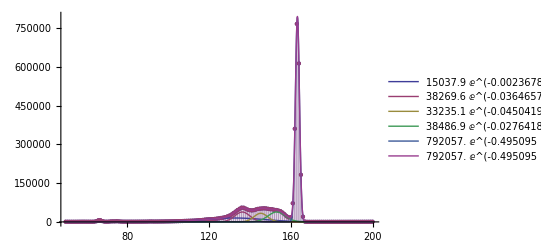

```mathematica
mu={131.6,135.3,144.6,152.5,162.3};sigma={14.2,3.6,3.6,4.0,1.0};
a={15000,30000,10800,30000,730000};n=Length[mu];

model=NonlinearModelFit[bkgdata,G[x,Table[Symbol["mu"<>ToString[i]],{i,1,n}],Table[Symbol["sigma"<>ToString[i]],{i,1,n}],Table[Symbol["a"<>ToString[i]],{i,1,n}]],Join[Table[{Symbol["mu"<>ToString[i]],mu[[i]]},{i,1,n}],Table[{Symbol["sigma"<>ToString[i]],sigma[[i]]},{i,1,n}],Table[{Symbol["a"<>ToString[i]],a[[i]]},{i,1,n}]],x];
model["ParameterTable"]
params=model["BestFitParameters"];
paramerrors=model["ParameterErrors"];

theme="Classic";
Show[ListPlot[{viewingdata,bkgdata[[50;;200]]},Filling->Bottom,PlotTheme->theme,PlotRange->All],Plot[Evaluate@Join[Table[F[x,params[[i,2]],params[[i+n,2]],params[[i+2n,2]]],{i,1,n}],{G[x,params[[;;n,2]],params[[n+1;;2n,2]],params[[2n+1;;3n,2]]]}],{x,50,200},PlotRange->All,PlotTheme->theme,PlotLegends->"Expressions"],PlotRange->{{50,200},{0,60000}}]
Show[ListPlot[{viewingdata,bkgdata[[50;;200]]},Filling->Bottom,PlotTheme->theme,PlotRange->All],Plot[Evaluate@Join[Table[F[x,params[[i,2]],params[[i+n,2]],params[[i+2n,2]]],{i,1,n}],{G[x,params[[;;n,2]],params[[n+1;;2n,2]],params[[2n+1;;3n,2]]]}],{x,50,200},PlotRange->All,PlotTheme->theme,PlotLegends->"Expressions"],PlotRange->{{50,200},All}]
```

### Conclusion

```mathematica
Table[{params[[i,2]],paramerrors[[i]],100*paramerrors[[i]]/params[[i,2]]},{i,{5,10,15}}]//TableForm
background=Table[err[F2,{i[[1]],0},{params[[5,2]],paramerrors[[5]]},{params[[10,2]],paramerrors[[10]]},{params[[15,2]],paramerrors[[15]]}],{i,bkgdata}];
counts[1]=Total[background[[All,1]]];countserror[1]=Sqrt[Total[(background[[All,2]])^2]];{counts[1],countserror[1],100countserror[1]/counts[1]}
```

163.274 | 0.000315201 | 0.00019305
1.00494 | 0.000353532 | 0.0351794
792057. | 221.854 | 0.0280099

{1.9952×10^6,496.219,0.0248706}

```mathematica
peakbackground=Apply[err,Join[{backgroundfunction,{params[[5,2]],paramerrors[[5]]}},Table[{params[[i,2]],paramerrors[[i]]},{i,1,4}],Table[{params[[i+5,2]],paramerrors[[i]]},{i,1,4}],Table[{params[[i+10,2]],paramerrors[[i]]},{i,1,4}]]]
countsalt[1]=NIntegrate[F2[x,params[[5,2]],params[[5+5,2]],params[[5+10,2]]],{x,params[[5,2]]-2*fwhm[params[[5+5,2]]],params[[5,2]]+2*fwhm[params[[5+5,2]]]}];
countserroralt[1]=Sqrt[paramerrors[[-1]]^2+peakbackground[[2]]^2];
{countsalt[1],countserroralt[1],100*countserroralt[1]/countsalt[1]}
```

{3929.95,453.152}

{1.9952×10^6,504.545,0.025288}

## Source 1-hr Trial 2

### Data Selection

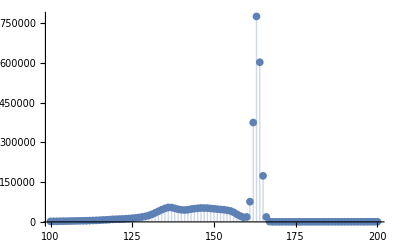

```mathematica
ListPlot[sourcedata[2][[100;;200]],Filling->Bottom,PlotRange->All]
```

### NonlinearModelFit bins

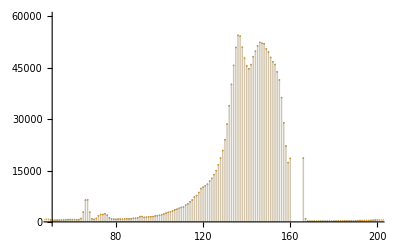

```mathematica
bkgdata=sourcedata[2];
viewingdata=sourcedata[2][[50;;200]];
ListPlot[{viewingdata,bkgdata},Filling->Bottom,PlotRange->{{50,200},{0,60000}}]
```

| Estimate | Standard Error | t-Statistic | P-Value
mu1 | 132.534 | 0.321204 | 412.616 | 9.5413176534×10^-5477
mu2 | 136.299 | 0.0532678 | 2558.74 | 8.6402950868×10^-11876
mu3 | 145.488 | 0.0842199 | 1727.47 | 2.6140049821×10^-10483
mu4 | 153.363 | 0.133986 | 1144.62 | 7.4181234128×10^-9028
mu5 | 163.245 | 0.000312261 | 522782. | 7.5893697016×10^-30765
sigma1 | 14.5814 | 0.146621 | 99.4496 | 2.6111519164×10^-1410
sigma2 | 3.74875 | 0.0432638 | 86.6486 | 3.2335108979×10^-1159
sigma3 | 3.43125 | 0.0894839 | 38.3449 | 5.57423×10^-296
sigma4 | 4.16781 | 0.0814016 | 51.2006 | 3.0677935614×10^-496
sigma5 | 1.00464 | 0.000349815 | 2871.92 | 2.2695950609×10^-12285
a1 | 14874.5 | 223.198 | 66.6425 | 7.6179670336×10^-773
a2 | 38066.9 | 377.208 | 100.917 | 5.5090265373×10^-1439
a3 | 34296.4 | 923.602 | 37.1334 | 4.65957×10^-279
a4 | 37793.2 | 697.359 | 54.1948 | 2.1008025589×10^-547
a5 | 794113. | 220.392 | 3603.18 | 2.8244943556×10^-13090

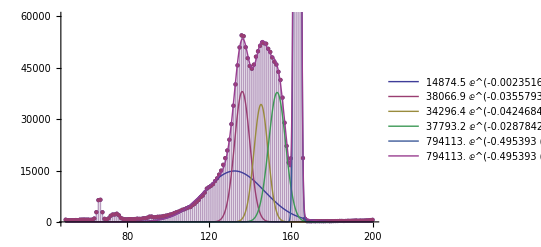

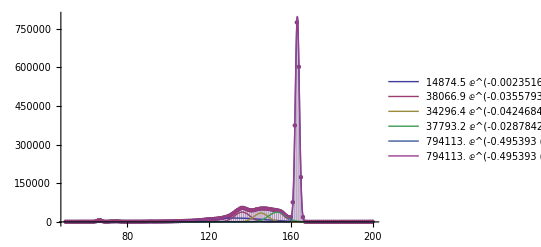

```mathematica
mu={131.6,135.3,144.6,152.5,162.3};sigma={14.2,3.6,3.6,4.0,1.0};
a={15000,30000,10800,30000,730000};n=Length[mu];

model=NonlinearModelFit[bkgdata,G[x,Table[Symbol["mu"<>ToString[i]],{i,1,n}],Table[Symbol["sigma"<>ToString[i]],{i,1,n}],Table[Symbol["a"<>ToString[i]],{i,1,n}]],Join[Table[{Symbol["mu"<>ToString[i]],mu[[i]]},{i,1,n}],Table[{Symbol["sigma"<>ToString[i]],sigma[[i]]},{i,1,n}],Table[{Symbol["a"<>ToString[i]],a[[i]]},{i,1,n}]],x];
model["ParameterTable"]
params=model["BestFitParameters"];
paramerrors=model["ParameterErrors"];

theme="Classic";
Show[ListPlot[{viewingdata,bkgdata[[50;;200]]},Filling->Bottom,PlotTheme->theme,PlotRange->All],Plot[Evaluate@Join[Table[F[x,params[[i,2]],params[[i+n,2]],params[[i+2n,2]]],{i,1,n}],{G[x,params[[;;n,2]],params[[n+1;;2n,2]],params[[2n+1;;3n,2]]]}],{x,50,200},PlotRange->All,PlotTheme->theme,PlotLegends->"Expressions"],PlotRange->{{50,200},{0,60000}}]
Show[ListPlot[{viewingdata,bkgdata[[50;;200]]},Filling->Bottom,PlotTheme->theme,PlotRange->All],Plot[Evaluate@Join[Table[F[x,params[[i,2]],params[[i+n,2]],params[[i+2n,2]]],{i,1,n}],{G[x,params[[;;n,2]],params[[n+1;;2n,2]],params[[2n+1;;3n,2]]]}],{x,50,200},PlotRange->All,PlotTheme->theme,PlotLegends->"Expressions"],PlotRange->{{50,200},All}]
```

### Conclusion

```mathematica
Table[{params[[i,2]],paramerrors[[i]],100*paramerrors[[i]]/params[[i,2]]},{i,{5,10,15}}]//TableForm
background=Table[err[F2,{i[[1]],0},{params[[5,2]],paramerrors[[5]]},{params[[10,2]],paramerrors[[10]]},{params[[15,2]],paramerrors[[15]]}],{i,bkgdata}];
counts[2]=Total[background[[All,1]]];countserror[2]=Sqrt[Total[(background[[All,2]])^2]];{counts[2],countserror[2],100countserror[2]/counts[2]}
```

163.245 | 0.000312261 | 0.000191284
1.00464 | 0.000349815 | 0.03482
794113. | 220.392 | 0.0277533

{1.99978×10^6,492.82,0.0246437}

```mathematica
peakbackground=Apply[err,Join[{backgroundfunction,{params[[5,2]],paramerrors[[5]]}},Table[{params[[i,2]],paramerrors[[i]]},{i,1,4}],Table[{params[[i+5,2]],paramerrors[[i]]},{i,1,4}],Table[{params[[i+10,2]],paramerrors[[i]]},{i,1,4}]]]
countsalt[2]=NIntegrate[F2[x,params[[5,2]],params[[5+5,2]],params[[5+10,2]]],{x,params[[5,2]]-2*fwhm[params[[5+5,2]]],params[[5,2]]+2*fwhm[params[[5+5,2]]]}];
countserroralt[2]=Sqrt[paramerrors[[-1]]^2+peakbackground[[2]]^2];
{countsalt[2],countserroralt[2],100*countserroralt[2]/countsalt[2]}
```

{3892.29,479.06}

{1.99978×10^6,527.325,0.0263692}

## Thick Film

### Data Selection

```mathematica
ListPlot[thickdata[1][[100;;200]],Filling->Bottom,PlotRange->All]
```

-Graphics-

### NonlinearModelFit bins

```mathematica
bkgdata=thickdata[1];
viewingdata=thickdata[1][[50;;200]];
ListPlot[{viewingdata,bkgdata},Filling->Bottom,PlotRange->{{50,200},{0,60000}}]
```

-Graphics-

```mathematica
mu={131.6,135.3,144.6,152.5,162.3};sigma={14.2,3.6,3.6,4.0,1.0};
a={15000,30000,10800,30000,730000};n=Length[mu];

model=NonlinearModelFit[bkgdata,G[x,Table[Symbol["mu"<>ToString[i]],{i,1,n}],Table[Symbol["sigma"<>ToString[i]],{i,1,n}],Table[Symbol["a"<>ToString[i]],{i,1,n}]],Join[Table[{Symbol["mu"<>ToString[i]],mu[[i]]},{i,1,n}],Table[{Symbol["sigma"<>ToString[i]],sigma[[i]]},{i,1,n}],Table[{Symbol["a"<>ToString[i]],a[[i]]},{i,1,n}]],x];
model["ParameterTable"]
params=model["BestFitParameters"];
paramerrors=model["ParameterErrors"];

theme="Classic";
Show[ListPlot[{viewingdata,bkgdata[[50;;200]]},Filling->Bottom,PlotTheme->theme,PlotRange->All],Plot[Evaluate@Join[Table[F[x,params[[i,2]],params[[i+n,2]],params[[i+2n,2]]],{i,1,n}],{G[x,params[[;;n,2]],params[[n+1;;2n,2]],params[[2n+1;;3n,2]]]}],{x,50,200},PlotRange->All,PlotTheme->theme,PlotLegends->"Expressions"],PlotRange->{{50,200},{0,60000}}]
Show[ListPlot[{viewingdata,bkgdata[[50;;200]]},Filling->Bottom,PlotTheme->theme,PlotRange->All],Plot[Evaluate@Join[Table[F[x,params[[i,2]],params[[i+n,2]],params[[i+2n,2]]],{i,1,n}],{G[x,params[[;;n,2]],params[[n+1;;2n,2]],params[[2n+1;;3n,2]]]}],{x,50,200},PlotRange->All,PlotTheme->theme,PlotLegends->"Expressions"],PlotRange->{{50,200},All}]
```

| Estimate | Standard Error | t-Statistic | P-Value
mu1 | 132.122 | 0.311185 | 424.577 | 1.0547903294×10^-5573
mu2 | 136.312 | 0.0494857 | 2754.57 | 2.2282756232×10^-12137
mu3 | 145.485 | 0.0750617 | 1938.21 | 4.4882124411×10^-10891
mu4 | 153.189 | 0.118701 | 1290.55 | 1.2555417506×10^-9451
mu5 | 163.204 | 0.000354701 | 460118. | 2.0211604638×10^-30311
sigma1 | 14.7209 | 0.143079 | 102.887 | 2.224411121×10^-1477
sigma2 | 3.85265 | 0.0412333 | 93.4353 | 1.8369288972×10^-1292
sigma3 | 3.35453 | 0.078195 | 42.8996 | 7.4347204102×10^-363
sigma4 | 4.08984 | 0.0718777 | 56.9001 | 8.4872871004×10^-595
sigma5 | 1.00465 | 0.000393432 | 2553.55 | 1.3913342094×10^-11868
a1 | 14455. | 206.03 | 70.1598 | 2.6051800718×10^-839
a2 | 38704.6 | 345.039 | 112.175 | 4.9710696568×10^-1657
a3 | 34668.2 | 864.519 | 40.1011 | 3.568450242×10^-321
a4 | 38342. | 638.379 | 60.0615 | 2.0155867133×10^-651
a5 | 661860. | 207.456 | 3190.37 | 1.7956237211×10^-12658

-Graphics-

-Graphics-

### Conclusion

```mathematica
Table[{params[[i,2]],paramerrors[[i]],100*paramerrors[[i]]/params[[i,2]]},{i,{5,10,15}}]//TableForm
background=Table[err[F2,{i[[1]],0},{params[[5,2]],paramerrors[[5]]},{params[[10,2]],paramerrors[[10]]},{params[[15,2]],paramerrors[[15]]}],{i,bkgdata}];
counts[3]=Total[background[[All,1]]];countserror[3]=Sqrt[Total[(background[[All,2]])^2]];{counts[3],countserror[3],100countserror[3]/counts[3]}
```

163.204 | 0.000354701 | 0.000217336
1.00465 | 0.000393432 | 0.0391612
661860. | 207.456 | 0.0313443

{1.66675×10^6,463.871,0.0278309}

```mathematica
peakbackground=Apply[err,Join[{backgroundfunction,{params[[5,2]],paramerrors[[5]]}},Table[{params[[i,2]],paramerrors[[i]]},{i,1,4}],Table[{params[[i+5,2]],paramerrors[[i]]},{i,1,4}],Table[{params[[i+10,2]],paramerrors[[i]]},{i,1,4}]]]
countsalt[3]=NIntegrate[F2[x,params[[5,2]],params[[5+5,2]],params[[5+10,2]]],{x,params[[5,2]]-2*fwhm[params[[5+5,2]]],params[[5,2]]+2*fwhm[params[[5+5,2]]]}];
countserroralt[3]=Sqrt[paramerrors[[-1]]^2+peakbackground[[2]]^2];
{countsalt[3],countserroralt[3],100*countserroralt[3]/countsalt[3]}
```

{3467.38,394.323}

{1.66674×10^6,445.565,0.0267327}

## Thin Film

### Data Selection

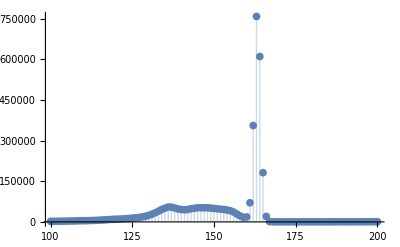

```mathematica
ListPlot[thindata[1][[100;;200]],Filling->Bottom,PlotRange->All]
```

### NonlinearModelFit bins

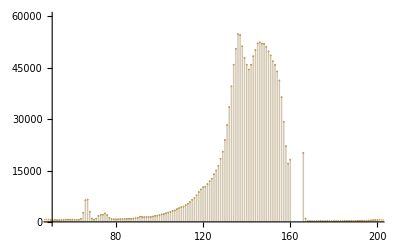

```mathematica
bkgdata=thindata[1];
viewingdata=thindata[1][[50;;200]];
ListPlot[{viewingdata,bkgdata},Filling->Bottom,PlotRange->{{50,200},{0,60000}}]
```

| Estimate | Standard Error | t-Statistic | P-Value
mu1 | 126.417 | 2.72977 | 46.3104 | 5.1640111627×10^-416
mu2 | 135.511 | 0.0264457 | 5124.12 | 2.9953186755×10^-14340
mu3 | 141.898 | 0.879875 | 161.27 | 1.123186022×10^-2542
mu4 | 152.558 | 0.174747 | 873.021 | 7.6401464093×10^-8074
mu5 | 163.28 | 0.000322375 | 506490. | 2.0417089588×10^-30652
sigma1 | 15.5594 | 0.946897 | 16.432 | 1.01633×10^-59
sigma2 | 2.24497 | 0.0455899 | 49.2427 | 1.3651339906×10^-463
sigma3 | -8.59657 | 0.626898 | -13.7129 | 2.49387×10^-42
sigma4 | 5.26634 | 0.213742 | 24.6388 | 2.32137×10^-129
sigma5 | 1.00202 | 0.000357572 | 2802.28 | 2.6975590972×10^-12198
a1 | 8397.54 | 1029.52 | 8.15679 | 3.95215×10^-16
a2 | 17412.3 | 484.986 | 35.9026 | 2.89868×10^-262
a3 | 38171.8 | 3054.67 | 12.4962 | 1.64968×10^-35
a4 | 27634.5 | 4504.47 | 6.13491 | 8.91679×10^-10
a5 | 783412. | 226.145 | 3464.2 | 1.1117354539×10^-12950

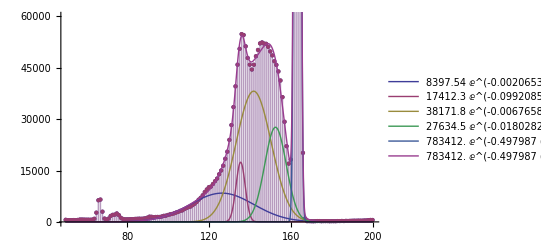

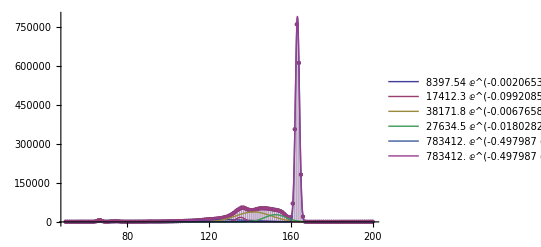

```mathematica
mu={131.6,135.3,144.6,152.5,162.3};sigma={14.2,3.6,3.6,4.0,1.0};
a={15000,30000,10800,30000,730000};n=Length[mu];

model=NonlinearModelFit[bkgdata,G[x,Table[Symbol["mu"<>ToString[i]],{i,1,n}],Table[Symbol["sigma"<>ToString[i]],{i,1,n}],Table[Symbol["a"<>ToString[i]],{i,1,n}]],Join[Table[{Symbol["mu"<>ToString[i]],mu[[i]]},{i,1,n}],Table[{Symbol["sigma"<>ToString[i]],sigma[[i]]},{i,1,n}],Table[{Symbol["a"<>ToString[i]],a[[i]]},{i,1,n}]],x];
model["ParameterTable"]
params=model["BestFitParameters"];
paramerrors=model["ParameterErrors"];

theme="Classic";
Show[ListPlot[{viewingdata,bkgdata[[50;;200]]},Filling->Bottom,PlotTheme->theme,PlotRange->All],Plot[Evaluate@Join[Table[F[x,params[[i,2]],params[[i+n,2]],params[[i+2n,2]]],{i,1,n}],{G[x,params[[;;n,2]],params[[n+1;;2n,2]],params[[2n+1;;3n,2]]]}],{x,50,200},PlotRange->All,PlotTheme->theme,PlotLegends->"Expressions"],PlotRange->{{50,200},{0,60000}}]
Show[ListPlot[{viewingdata,bkgdata[[50;;200]]},Filling->Bottom,PlotTheme->theme,PlotRange->All],Plot[Evaluate@Join[Table[F[x,params[[i,2]],params[[i+n,2]],params[[i+2n,2]]],{i,1,n}],{G[x,params[[;;n,2]],params[[n+1;;2n,2]],params[[2n+1;;3n,2]]]}],{x,50,200},PlotRange->All,PlotTheme->theme,PlotLegends->"Expressions"],PlotRange->{{50,200},All}]
```

### Conclusion

```mathematica
Table[{params[[i,2]],paramerrors[[i]],100*paramerrors[[i]]/params[[i,2]]},{i,{5,10,15}}]//TableForm
background=Table[err[F2,{i[[1]],0},{params[[5,2]],paramerrors[[5]]},{params[[10,2]],paramerrors[[10]]},{params[[15,2]],paramerrors[[15]]}],{i,bkgdata}];
counts[4]=Total[background[[All,1]]];countserror[4]=Sqrt[Total[(background[[All,2]])^2]];{counts[4],countserror[4],100countserror[4]/counts[4]}
```

163.28 | 0.000322375 | 0.000197437
1.00202 | 0.000357572 | 0.0356852
783412. | 226.145 | 0.0288667

{1.96769×10^6,501.184,0.0254707}

```mathematica
peakbackground=Apply[err,Join[{backgroundfunction,{params[[5,2]],paramerrors[[5]]}},Table[{params[[i,2]],paramerrors[[i]]},{i,1,4}],Table[{params[[i+5,2]],paramerrors[[i]]},{i,1,4}],Table[{params[[i+10,2]],paramerrors[[i]]},{i,1,4}]]]
countsalt[4]=NIntegrate[F2[x,params[[5,2]],params[[5+5,2]],params[[5+10,2]]],{x,params[[5,2]]-2*fwhm[params[[5+5,2]]],params[[5,2]]+2*fwhm[params[[5+5,2]]]}];
countserroralt[4]=Sqrt[paramerrors[[-1]]^2+peakbackground[[2]]^2];
{countsalt[4],countserroralt[4],100*countserroralt[4]/countsalt[4]}
```

{5716.94,1405.04}

{1.96768×10^6,1423.12,0.0723248}

## Calculations

```mathematica
thickness=40;thicknesserror=0.01;
Print["Peak Data\n",Table[{counts[i],countserror[i],100*countserror[i]/counts[i]},{i,1,4}]//TableForm,"\n"]
coeff[counts1_,counts3_,thickness_]:=(-Log[counts3/counts1])/thickness;


attencoeff=err[coeff,{counts[1],countserror[1]},{counts[3],countserror[3]},{thickness,thicknesserror}]
thinmeasure=err[coeff,{counts[1],countserror[1]},{counts[4],countserror[4]},attencoeff];Join[thinmeasure,{100*thinmeasure[[2]]/thinmeasure[[1]]}]

attencoeff=err[coeff,{counts[2],countserror[2]},{counts[3],countserror[3]},{thickness,thicknesserror}]
thinmeasure=err[coeff,{counts[2],countserror[2]},{counts[4],countserror[4]},attencoeff];Join[thinmeasure,{100*thinmeasure[[2]]/thinmeasure[[1]]}]

thick[counts1_,counts2_,counts3_,thickness_]:=thickness Log[counts3/counts1]/Log[counts2/counts1]
thinmeasure=err[thick,{counts[1],countserror[1]},{counts[3],countserror[3]},{counts[4],countserror[4]},{thickness,thicknesserror}];
Join[thinmeasure,{100*thinmeasure[[2]]/thinmeasure[[1]]}]

thinmeasure=err[thick,{counts[2],countserror[2]},{counts[3],countserror[3]},{counts[4],countserror[4]},{thickness,thicknesserror}];
Join[thinmeasure,{100*thinmeasure[[2]]/thinmeasure[[1]]}]
```

Peak Data
1.9952×10^6 | 496.219 | 0.0248706
1.99978×10^6 | 492.82 | 0.0246437
1.66675×10^6 | 463.871 | 0.0278309
1.96769×10^6 | 501.184 | 0.0254707

{0.00449678,9.39856×10^-6}

{3.08802,0.0794287,2.57216}

{0.00455407,9.36287×10^-6}

{3.55236,0.0781649,2.20037}

{3.08802,0.0763978,2.47401}

{3.55236,0.0747639,2.10463}

```mathematica
thickness=40;thicknesserror=0.01;
Print["Peak Data\n",Table[{countsalt[i],countserroralt[i],100*countserroralt[i]/countsalt[i]},{i,1,4}]//TableForm,"\n"]
coeff[counts1_,counts3_,thickness_]:=(-Log[counts3/counts1])/thickness;


attencoeff=err[coeff,{countsalt[1],countserroralt[1]},{countsalt[3],countserroralt[3]},{thickness,thicknesserror}]
thinmeasure=err[coeff,{countsalt[1],countserroralt[1]},{countsalt[4],countserroralt[4]},attencoeff];Join[thinmeasure,{100*thinmeasure[[2]]/thinmeasure[[1]]}]

attencoeff=err[coeff,{countsalt[2],countserroralt[2]},{countsalt[3],countserroralt[3]},{thickness,thicknesserror}]
thinmeasure=err[coeff,{countsalt[2],countserroralt[2]},{countsalt[4],countserroralt[4]},attencoeff];Join[thinmeasure,{100*thinmeasure[[2]]/thinmeasure[[1]]}]

thick[counts1_,counts2_,counts3_,thickness_]:=thickness Log[counts3/counts1]/Log[counts2/counts1]
thinmeasure=err[thick,{countsalt[1],countserroralt[1]},{countsalt[3],countserroralt[3]},{countsalt[4],countserroralt[4]},{thickness,thicknesserror}];
Join[thinmeasure,{100*thinmeasure[[2]]/thinmeasure[[1]]}]

thinmeasure=err[thick,{countsalt[2],countserroralt[2]},{countsalt[3],countserroralt[3]},{countsalt[4],countserroralt[4]},{thickness,thicknesserror}];
Join[thinmeasure,{100*thinmeasure[[2]]/thinmeasure[[1]]}]
```

Peak Data
1.9952×10^6 | 504.545 | 0.025288
1.99978×10^6 | 527.325 | 0.0263692
1.66674×10^6 | 445.565 | 0.0267327
1.96768×10^6 | 1423.12 | 0.0723248

{0.00449678,9.26802×10^-6}

{3.08802,0.170504,5.52146}

{0.00455407,9.45618×10^-6}

{3.55236,0.169201,4.76305}

{3.08802,0.169066,5.47489}

{3.55236,0.167432,4.71326}

# Data Set 4

```mathematica
ClearAll["Global`*"]
(*~ MacOS ~*)
main="/Users/mikhailgaerlan/Box Sync/Education/MSU/Research/Radiation Thickness/Data";

SetDirectory[main];
$Line=0;
```

## Data Import

## Source 1-Hour

### Trial 1

$SPEC_ID:
Molnar Range
$SPEC_REM:
DET# 1
DETDESC# HPGe Detector 1
AP# GammaVision Version 6.07
$DATE_MEA:
02/02/2016 10:18:29
$MEAS_TIM:
3600 3917
$DATA:
0 8191
       0
       0
       0

0
       1
$ROI:
0
$PRESETS:
Live Time
3600
0
$ENER_FIT:
0.137869 0.366631
$MCA_CAL:
3
1.378689E-001 3.666307E-001 -4.415950E-008 keV
$SHAPE_CAL:
3
2.301834E+000 9.195991E-004 -5.357180E-008

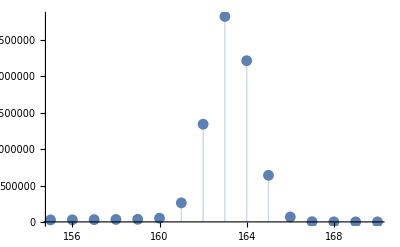

```mathematica
imported=Import["Run 1 - Am-241-1hr-NewConfiguration.Spe","Data"];
times=ToExpression[StringSplit[imported[[10]]]];
deadtime=N[Abs[times[[1]]-times[[2]]]/times[[2]]];
imported[[;;15]]//TableForm
imported[[-16;;]]//TableForm
freq=ToExpression[imported[[13;;-15]]]/(1-deadtime);
sourcedata[1]=Table[{i,freq[[i]]},{i,Length[freq]}];
ListPlot[sourcedata[1][[155;;170]],PlotRange->All,Filling->Bottom]
```

### Trial 2

$SPEC_ID:
Molnar Range
$SPEC_REM:
DET# 1
DETDESC# HPGe Detector 1
AP# GammaVision Version 6.07
$DATE_MEA:
02/03/2016 13:05:24
$MEAS_TIM:
3600 3905
$DATA:
0 8191
       0
       0
       0

0
       0
$ROI:
0
$PRESETS:
Live Time
3600
0
$ENER_FIT:
0.137869 0.366631
$MCA_CAL:
3
1.378689E-001 3.666307E-001 -4.415950E-008 keV
$SHAPE_CAL:
3
2.301834E+000 9.195991E-004 -5.357180E-008

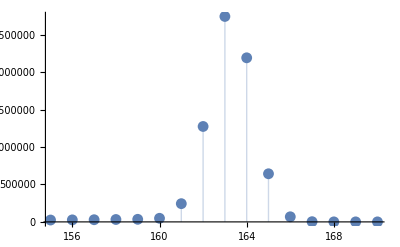

```mathematica
imported=Import["Run 2 - Am-241-1hr-NewConfiguration.Spe","Data"];
times=ToExpression[StringSplit[imported[[10]]]];
deadtime=N[Abs[times[[1]]-times[[2]]]/times[[2]]];
imported[[;;15]]//TableForm
imported[[-16;;]]//TableForm
freq=ToExpression[imported[[13;;-15]]]/(1-deadtime);
sourcedata[2]=Table[{i,freq[[i]]},{i,Length[freq]}];
ListPlot[sourcedata[2][[155;;170]],PlotRange->All,Filling->Bottom]
```

## Thick Film

### Trial 1

$SPEC_ID:
Molnar Range
$SPEC_REM:
DET# 1
DETDESC# HPGe Detector 1
AP# GammaVision Version 6.07
$DATE_MEA:
02/02/2016 11:25:48
$MEAS_TIM:
3600 3891
$DATA:
0 8191
       0
       0
       0

0
       0
$ROI:
0
$PRESETS:
Live Time
3600
0
$ENER_FIT:
0.137869 0.366631
$MCA_CAL:
3
1.378689E-001 3.666307E-001 -4.415950E-008 keV
$SHAPE_CAL:
3
2.301834E+000 9.195991E-004 -5.357180E-008

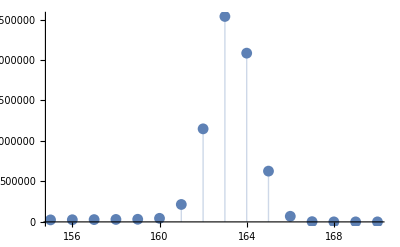

```mathematica
imported=Import["Run 1 - Am-241-1hr-ThickFilm-NewConfiguration.Spe","Data"];
times=ToExpression[StringSplit[imported[[10]]]];
deadtime=N[Abs[times[[1]]-times[[2]]]/times[[2]]];
imported[[;;15]]//TableForm
imported[[-16;;]]//TableForm
freq=ToExpression[imported[[13;;-15]]]/(1-deadtime);
thickdata[1]=Table[{i,freq[[i]]},{i,Length[freq]}];
ListPlot[thickdata[1][[155;;170]],PlotRange->All,Filling->Bottom]
```

### Trial 2

$SPEC_ID:
Molnar Range
$SPEC_REM:
DET# 1
DETDESC# HPGe Detector 1
AP# GammaVision Version 6.07
$DATE_MEA:
02/03/2016 10:53:09
$MEAS_TIM:
3600 3879
$DATA:
0 8191
       0
       0
       0

0
       0
$ROI:
0
$PRESETS:
Live Time
3600
0
$ENER_FIT:
0.137869 0.366631
$MCA_CAL:
3
1.378689E-001 3.666307E-001 -4.415950E-008 keV
$SHAPE_CAL:
3
2.301834E+000 9.195991E-004 -5.357180E-008

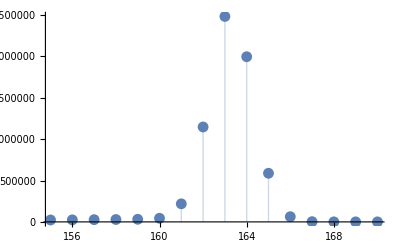

```mathematica
imported=Import["Run 2 - Am-241-1hr-ThickFilm-NewConfiguration.Spe","Data"];
times=ToExpression[StringSplit[imported[[10]]]];
deadtime=N[Abs[times[[1]]-times[[2]]]/times[[2]]];
imported[[;;15]]//TableForm
imported[[-16;;]]//TableForm
freq=ToExpression[imported[[13;;-15]]]/(1-deadtime);
thickdata[2]=Table[{i,freq[[i]]},{i,Length[freq]}];
ListPlot[thickdata[2][[155;;170]],PlotRange->All,Filling->Bottom]
```

## Thin Film

### Trial 1

$SPEC_ID:
Molnar Range
$SPEC_REM:
DET# 1
DETDESC# HPGe Detector 1
AP# GammaVision Version 6.07
$DATE_MEA:
02/02/2016 12:44:21
$MEAS_TIM:
3600 3914
$DATA:
0 8191
       0
       0
       0

1
       0
$ROI:
0
$PRESETS:
Live Time
3600
0
$ENER_FIT:
0.137869 0.366631
$MCA_CAL:
3
1.378689E-001 3.666307E-001 -4.415950E-008 keV
$SHAPE_CAL:
3
2.301834E+000 9.195991E-004 -5.357180E-008

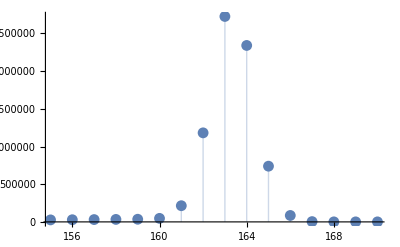

```mathematica
imported=Import["Run 1 - Am-241-1hr-ThinFilm-NewConfiguration.Spe","Data"];
times=ToExpression[StringSplit[imported[[10]]]];
deadtime=N[Abs[times[[1]]-times[[2]]]/times[[2]]];
imported[[;;15]]//TableForm
imported[[-16;;]]//TableForm
freq=ToExpression[imported[[13;;-15]]]/(1-deadtime);
thindata[1]=Table[{i,freq[[i]]},{i,Length[freq]}];
ListPlot[thindata[1][[155;;170]],PlotRange->All,Filling->Bottom]
```

### Trial 2

$SPEC_ID:
Molnar Range
$SPEC_REM:
DET# 1
DETDESC# HPGe Detector 1
AP# GammaVision Version 6.07
$DATE_MEA:
02/03/2016 08:45:49
$MEAS_TIM:
3600 3902
$DATA:
0 8191
       0
       0
       0

0
       0
$ROI:
0
$PRESETS:
Live Time
3600
0
$ENER_FIT:
0.137869 0.366631
$MCA_CAL:
3
1.378689E-001 3.666307E-001 -4.415950E-008 keV
$SHAPE_CAL:
3
2.301834E+000 9.195991E-004 -5.357180E-008

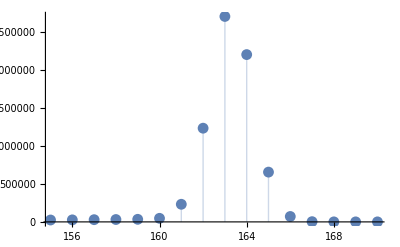

```mathematica
imported=Import["Run 2 - Am-241-1hr-ThinFilm-NewConfiguration.Spe","Data"];
times=ToExpression[StringSplit[imported[[10]]]];
deadtime=N[Abs[times[[1]]-times[[2]]]/times[[2]]];
imported[[;;15]]//TableForm
imported[[-16;;]]//TableForm
freq=ToExpression[imported[[13;;-15]]]/(1-deadtime);
thindata[2]=Table[{i,freq[[i]]},{i,Length[freq]}];
ListPlot[thindata[2][[155;;170]],PlotRange->All,Filling->Bottom]
```

## Data Analysis

## Equations

```mathematica
F[x_,mu_,sigma_,a_]:=a*Exp[-1/2*((x-mu)/sigma)^2]
F2[x_,mu_,sigma_,a_]:=a*Exp[-1/2*((x-mu)/sigma)^2]
F3[x_,mu1_,mu2_,mu3_,mu4_,sigma1_,sigma2_,sigma3_,sigma4_,a1_,a2_,a3_,a4_]:=F[x,mu1,sigma1,a1]+F[x,mu2,sigma2,a2]+F[x,mu3,sigma3,a3]+F[x,mu4,sigma4,a4]
G[x_,mu_,sigma_,a_]:=Sum[F[x,mu[[i]],sigma[[i]],a[[i]]],{i,1,Length[mu]}]

chisq2[data_,mu_,sigma_,a_]:=Sum[(data[[i,2]]-G[data[[i,1]],mu,sigma,a])^2,{i,Length[data]}]
backgroundfunction[x_,mu1_,mu2_,mu3_,mu4_,sigma1_,sigma2_,sigma3_,sigma4_,a1_,a2_,a3_,a4_]:=F2[x,mu1,sigma1,a1]+F2[x,mu2,sigma2,a2]+F2[x,mu3,sigma3,a3]+F2[x,mu4,sigma4,a4];
fwhm[sigma_]:=2*sigma*Sqrt[2*Log[2]];

err[F_,w__]:={F[Map[First,List[w]]/.List->Sequence],Block[{parms=Table[Unique[],{x,1,Length[List[w]]}],values=Table[List[w][[i,1]],{i,1,Length[List[w]]}],errors=Table[List[w][[i,2]],{i,1,Length[List[w]]}]},Sqrt[Total[Table[(D[F[parms/.List->Sequence],parms[[i]]]*errors[[i]])^2,{i,1,Length[values]}]/.Table[parms[[i]]->values[[i]],{i,1,Length[values]}]]]]}
```

## Source 1-hr Trial 1

### Data Selection

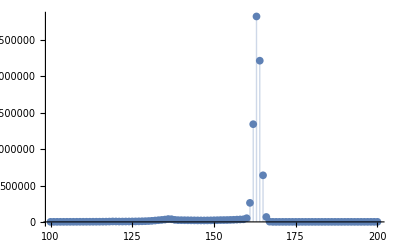

```mathematica
ListPlot[sourcedata[1][[100;;200]],Filling->Bottom,PlotRange->All]
```

### NonlinearModelFit bins

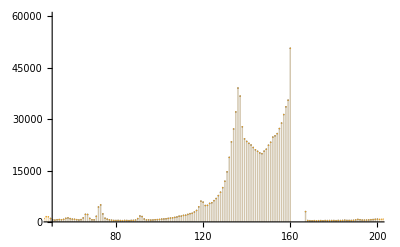

```mathematica
bkgdata=sourcedata[1];
viewingdata=sourcedata[1][[50;;200]];
ListPlot[{viewingdata,bkgdata},Filling->Bottom,PlotRange->{{50,200},{0,60000}}]
```

| Estimate | Standard Error | t-Statistic | P-Value
mu1 | 163.251 | 0.000618413 | 263983. | 2.3912057815×10^-28377
sigma1 | 1.00935 | 0.000618436 | 1632.1 | 1.0896709849×10^-10294
a1 | 2.91357×10^6 | 1545.96 | 1884.63 | 5.5467477408×10^-10805

2.82526×10^6

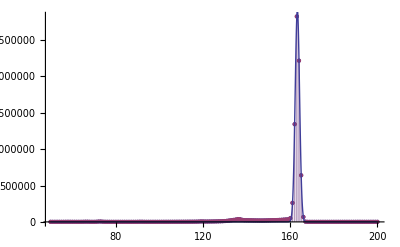

```mathematica
mu=162.3;sigma=1.0;a=730000;

model=NonlinearModelFit[bkgdata,F[x,mu1,sigma1,a1],{{mu1,mu},{sigma1,sigma},{a1,a}},x];
model["ParameterTable"]
params=model["BestFitParameters"];
paramerrors=model["ParameterErrors"];
Max[bkgdata]

theme="Classic";
Show[ListPlot[{viewingdata,bkgdata[[50;;200]]},Filling->Bottom,PlotTheme->theme,PlotRange->All],Plot[model[x],{x,50,200},PlotTheme->theme,PlotRange->All]]
```

| Estimate | Standard Error | t-Statistic | P-Value
mu1 | 141.277 | 0.249544 | 566.139 | 1.6207327346×10^-6561
mu2 | 135.876 | 0.0340996 | 3984.67 | 1.8415685866×10^-13447
mu3 | 155.324 | 0.665431 | 233.419 | 1.2033424465×10^-3618
mu4 | 160.308 | 0.125661 | 1275.72 | 8.5381619738×10^-9411
mu5 | 163.258 | 0.000236858 | 689264. | 1.2800493584×10^-31746
sigma1 | 11.1115 | 0.176234 | 63.0496 | 5.1156924345×10^-706
sigma2 | 1.8172 | 0.0412064 | 44.0999 | 2.8049230735×10^-381
sigma3 | 3.75327 | 0.400035 | 9.38237 | 8.20507×10^-21
sigma4 | 2.14853 | 0.215366 | 9.97617 | 2.63284×10^-23
sigma5 | 1.00029 | 0.000425686 | 2349.82 | 1.0146536057×10^-11573
a1 | 21538.1 | 199.625 | 107.893 | 1.5153429997×10^-1574
a2 | 18173.4 | 330.674 | 54.9586 | 1.1164978005×10^-560
a3 | 16278.5 | 1424.95 | 11.4239 | 5.36102×10^-30
a4 | 24523.1 | 3313.49 | 7.40098 | 1.48605×10^-13
a5 | 2.90504×10^6 | 2095.6 | 1386.25 | 1.5775527628×10^-9704

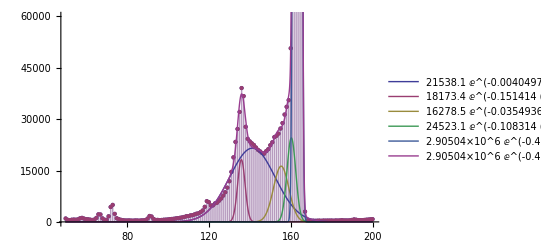

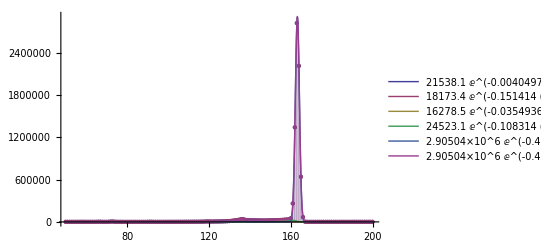

```mathematica
mu={131.6,135.3,144.6,152.5,162.3};sigma={14.2,3.6,3.6,4.0,1.0};
a={15000,30000,10800,30000,730000};n=Length[mu];

model=NonlinearModelFit[bkgdata,G[x,Table[Symbol["mu"<>ToString[i]],{i,1,n}],Table[Symbol["sigma"<>ToString[i]],{i,1,n}],Table[Symbol["a"<>ToString[i]],{i,1,n}]],Join[Table[{Symbol["mu"<>ToString[i]],mu[[i]]},{i,1,n}],Table[{Symbol["sigma"<>ToString[i]],sigma[[i]]},{i,1,n}],Table[{Symbol["a"<>ToString[i]],a[[i]]},{i,1,n}]],x];
model["ParameterTable"]
params=model["BestFitParameters"];
paramerrors=model["ParameterErrors"];

theme="Classic";
Show[ListPlot[{viewingdata,bkgdata[[50;;200]]},Filling->Bottom,PlotTheme->theme,PlotRange->All],Plot[Evaluate@Join[Table[F[x,params[[i,2]],params[[i+n,2]],params[[i+2n,2]]],{i,1,n}],{G[x,params[[;;n,2]],params[[n+1;;2n,2]],params[[2n+1;;3n,2]]]}],{x,50,200},PlotRange->All,PlotTheme->theme,PlotLegends->"Expressions"],PlotRange->{{50,200},{0,60000}}]
Show[ListPlot[{viewingdata,bkgdata[[50;;200]]},Filling->Bottom,PlotTheme->theme,PlotRange->All],Plot[Evaluate@Join[Table[F[x,params[[i,2]],params[[i+n,2]],params[[i+2n,2]]],{i,1,n}],{G[x,params[[;;n,2]],params[[n+1;;2n,2]],params[[2n+1;;3n,2]]]}],{x,50,200},PlotRange->All,PlotTheme->theme,PlotLegends->"Expressions"],PlotRange->{{50,200},All}]
```

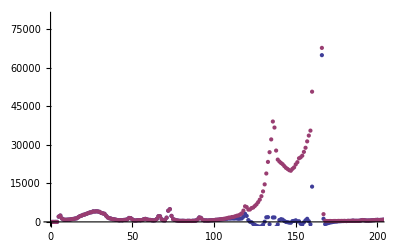

```mathematica
ListPlot[{Table[{i[[1]],i[[2]]-G[i[[1]],params[[;;n-1,2]],params[[n+1;;2n-1,2]],params[[2n+1;;3n-1,2]]]},{i,bkgdata}],bkgdata},PlotRange->{{0,200},{0,80000}},PlotTheme->theme]
```

### Conclusion

```mathematica
Table[{params[[i,2]],paramerrors[[i]],100*paramerrors[[i]]/params[[i,2]]},{i,{5,10,15}}]//TableForm
background=Table[err[F2,{i[[1]],0},{params[[5,2]],paramerrors[[5]]},{params[[10,2]],paramerrors[[10]]},{params[[15,2]],paramerrors[[15]]}],{i,bkgdata}];
counts[1]=Total[background[[All,1]]];countserror[1]=Sqrt[Total[(background[[All,2]])^2]];{counts[1],countserror[1],100countserror[1]/counts[1]}
```

163.258 | 0.000236858 | 0.000145082
1.00029 | 0.000425686 | 0.0425564
2.90504×10^6 | 2095.6 | 0.0721368

{7.28393×10^6,3199.52,0.0439257}

```mathematica
peakbackground=Apply[err,Join[{backgroundfunction,{params[[5,2]],paramerrors[[5]]}},Table[{params[[i,2]],paramerrors[[i]]},{i,1,4}],Table[{params[[i+5,2]],paramerrors[[i]]},{i,1,4}],Table[{params[[i+10,2]],paramerrors[[i]]},{i,1,4}]]]
countsalt[1]=NIntegrate[F2[x,params[[5,2]],params[[5+5,2]],params[[5+10,2]]],{x,params[[5,2]]-2*fwhm[params[[5+5,2]]],params[[5,2]]+2*fwhm[params[[5+5,2]]]}];
countserroralt[1]=Sqrt[paramerrors[[-1]]^2+peakbackground[[2]]^2];
{countsalt[1],countserroralt[1],100*countserroralt[1]/countsalt[1]}
```

{14341.8,2030.44}

{7.28392×10^6,2917.92,0.0400598}

```mathematica
dataerr=Table[{i[[2]],0},{i,bkgdata[[Floor[params[[n,2]]-2*Sqrt[2*Log[2]]*params[[2n,2]]];;Ceiling[params[[n,2]]+2*Sqrt[2*Log[2]]*params[[2n,2]]]]]}];
background=Table[err@@Join[{F3},{{j[[1]],0}},Delete[Table[{params[[i,2]],paramerrors[[i]]},{i,3n}],Table[{i n},{i,1,3}]]],{j,bkgdata[[Floor[params[[n,2]]-2*Sqrt[2*Log[2]]*params[[2n,2]]];;Ceiling[params[[n,2]]+2*Sqrt[2*Log[2]]*params[[2n,2]]]]]}];
countsalt2[1]=Total[dataerr[[All,1]]-background[[All,1]]];
countserroralt2[1]=Sqrt[Total[(background[[All,2]])^2]];
{countsalt2[1],countserroralt2[1],100*countserroralt2[1]/countsalt2[1]}
```

{7.27808×10^6,7333.46,0.100761}

## Source 1-hr Trial 2

### Data Selection

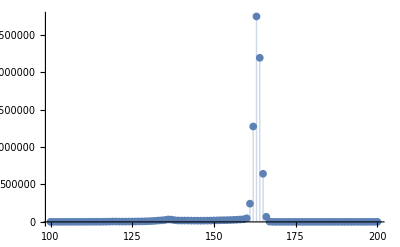

```mathematica
ListPlot[sourcedata[2][[100;;200]],Filling->Bottom,PlotRange->All]
```

### NonlinearModelFit bins

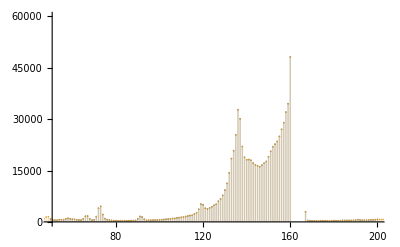

```mathematica
bkgdata=sourcedata[2];
viewingdata=sourcedata[2][[50;;200]];
ListPlot[{viewingdata,bkgdata},Filling->Bottom,PlotRange->{{50,200},{0,60000}}]
```

| Estimate | Standard Error | t-Statistic | P-Value
mu1 | 141.232 | 0.298782 | 472.692 | 5.6099897844×10^-5940
mu2 | 135.985 | 0.0346095 | 3929.11 | 1.2682489653×10^-13397
mu3 | 155.314 | 0.619815 | 250.581 | 1.1121323971×10^-3839
mu4 | 160.368 | 0.121439 | 1320.56 | 6.8316954226×10^-9533
mu5 | 163.277 | 0.000225787 | 723148. | 4.8350676311×10^-31917
sigma1 | 11.0979 | 0.211742 | 52.4122 | 9.0412680331×10^-517
sigma2 | 1.59564 | 0.0408687 | 39.043 | 6.66592×10^-306
sigma3 | 3.80594 | 0.381456 | 9.97741 | 2.60073×10^-23
sigma4 | 2.15111 | 0.1997 | 10.7717 | 7.08823×10^-27
sigma5 | 0.997654 | 0.000422117 | 2363.45 | 3.1600410729×10^-11594
a1 | 17173.3 | 183.304 | 93.6878 | 2.0344773948×10^-1297
a2 | 15906.7 | 326.03 | 48.7889 | 4.0128603622×10^-456
a3 | 16211.3 | 1296.58 | 12.5031 | 1.51483×10^-35
a4 | 24870.9 | 3056.05 | 8.13824 | 4.60133×10^-16
a5 | 2.83577×10^6 | 2023.26 | 1401.58 | 2.0289230758×10^-9743

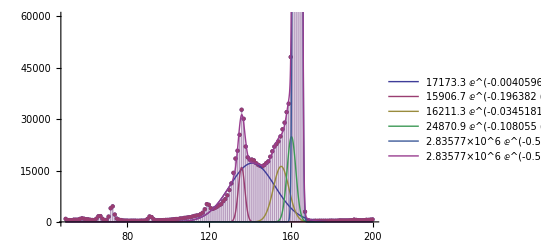

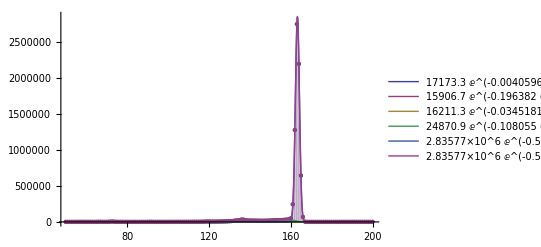

```mathematica
mu={141.3,135.9,155.3,160.3,163.3};sigma={11.1,1.8,3.8,2.1,1.0};
a={21500,18000,16000,25000,2900000};n=Length[mu];

model=NonlinearModelFit[bkgdata,G[x,Table[Symbol["mu"<>ToString[i]],{i,1,n}],Table[Symbol["sigma"<>ToString[i]],{i,1,n}],Table[Symbol["a"<>ToString[i]],{i,1,n}]],Join[Table[{Symbol["mu"<>ToString[i]],mu[[i]]},{i,1,n}],Table[{Symbol["sigma"<>ToString[i]],sigma[[i]]},{i,1,n}],Table[{Symbol["a"<>ToString[i]],a[[i]]},{i,1,n}]],x];
model["ParameterTable"]
params=model["BestFitParameters"];
paramerrors=model["ParameterErrors"];

theme="Classic";
Show[ListPlot[{viewingdata,bkgdata[[50;;200]]},Filling->Bottom,PlotTheme->theme,PlotRange->All],Plot[Evaluate@Join[Table[F[x,params[[i,2]],params[[i+n,2]],params[[i+2n,2]]],{i,1,n}],{G[x,params[[;;n,2]],params[[n+1;;2n,2]],params[[2n+1;;3n,2]]]}],{x,50,200},PlotRange->All,PlotTheme->theme,PlotLegends->"Expressions"],PlotRange->{{50,200},{0,60000}}]
Show[ListPlot[{viewingdata,bkgdata[[50;;200]]},Filling->Bottom,PlotTheme->theme,PlotRange->All],Plot[Evaluate@Join[Table[F[x,params[[i,2]],params[[i+n,2]],params[[i+2n,2]]],{i,1,n}],{G[x,params[[;;n,2]],params[[n+1;;2n,2]],params[[2n+1;;3n,2]]]}],{x,50,200},PlotRange->All,PlotTheme->theme,PlotLegends->"Expressions"],PlotRange->{{50,200},All}]
```

### Conclusion

```mathematica
Table[{params[[i,2]],paramerrors[[i]],100*paramerrors[[i]]/params[[i,2]]},{i,{5,10,15}}]//TableForm
background=Table[err[F2,{i[[1]],0},{params[[5,2]],paramerrors[[5]]},{params[[10,2]],paramerrors[[10]]},{params[[15,2]],paramerrors[[15]]}],{i,bkgdata}];
counts[2]=Total[background[[All,1]]];countserror[2]=Sqrt[Total[(background[[All,2]])^2]];{counts[2],countserror[2],100countserror[2]/counts[2]}
```

163.277 | 0.000225787 | 0.000138284
0.997654 | 0.000422117 | 0.042311
2.83577×10^6 | 2023.26 | 0.0713479

{7.09155×10^6,3083.65,0.0434835}

```mathematica
peakbackground=Apply[err,Join[{backgroundfunction,{params[[5,2]],paramerrors[[5]]}},Table[{params[[i,2]],paramerrors[[i]]},{i,1,4}],Table[{params[[i+5,2]],paramerrors[[i]]},{i,1,4}],Table[{params[[i+10,2]],paramerrors[[i]]},{i,1,4}]]]
countsalt[2]=NIntegrate[F2[x,params[[5,2]],params[[5+5,2]],params[[5+10,2]]],{x,params[[5,2]]-2*fwhm[params[[5+5,2]]],params[[5,2]]+2*fwhm[params[[5+5,2]]]}];
countserroralt[2]=Sqrt[paramerrors[[-1]]^2+peakbackground[[2]]^2];
{countsalt[2],countserroralt[2],100*countserroralt[2]/countsalt[2]}
```

{14171.3,1943.8}

{7.09153×10^6,2805.7,0.0395641}

```mathematica
dataerr=Table[{i[[2]],0},{i,bkgdata[[Floor[params[[n,2]]-2*Sqrt[2*Log[2]]*params[[2n,2]]];;Ceiling[params[[n,2]]+2*Sqrt[2*Log[2]]*params[[2n,2]]]]]}];
background=Table[err@@Join[{F3},{{j[[1]],0}},Delete[Table[{params[[i,2]],paramerrors[[i]]},{i,3n}],Table[{i n},{i,1,3}]]],{j,bkgdata[[Floor[params[[n,2]]-2*Sqrt[2*Log[2]]*params[[2n,2]]];;Ceiling[params[[n,2]]+2*Sqrt[2*Log[2]]*params[[2n,2]]]]]}];
countsalt2[2]=Total[dataerr[[All,1]]-background[[All,1]]];
countserroralt2[2]=Sqrt[Total[(background[[All,2]])^2]];
{countsalt2[2],countserroralt2[2],100*countserroralt2[2]/countsalt2[2]}
```

{7.08611×10^6,6870.,0.0969502}

## Thick Film 1

### Data Selection

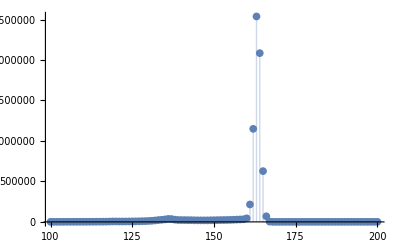

```mathematica
ListPlot[thickdata[1][[100;;200]],Filling->Bottom,PlotRange->All]
```

### NonlinearModelFit bins

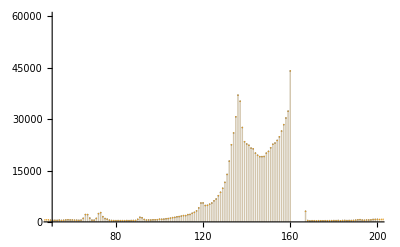

```mathematica
bkgdata=thickdata[1];
viewingdata=thickdata[1][[50;;200]];
ListPlot[{viewingdata,bkgdata},Filling->Bottom,PlotRange->{{50,200},{0,60000}}]
```

| Estimate | Standard Error | t-Statistic | P-Value
mu1 | 141.301 | 0.236498 | 597.472 | 2.6860712745×10^-6748
mu2 | 135.922 | 0.0340458 | 3992.34 | 2.7527087154×10^-13454
mu3 | 155.587 | 0.681834 | 228.189 | 7.0670201554×10^-3549
mu4 | 160.461 | 0.141258 | 1135.94 | 5.3736668395×10^-9001
mu5 | 163.304 | 0.000250364 | 652268. | 1.0636397001×10^-31550
sigma1 | 11.194 | 0.169632 | 65.9901 | 1.2663872184×10^-760
sigma2 | 1.85873 | 0.0412901 | 45.0163 | 1.4844450469×10^-395
sigma3 | 3.70912 | 0.40621 | 9.13103 | 8.42182×10^-20
sigma4 | 2.10237 | 0.230904 | 9.10495 | 1.06866×10^-19
sigma5 | 0.997692 | 0.000461816 | 2160.37 | 1.1200666293×10^-11275
a1 | 20712. | 182.027 | 113.785 | 6.9395282577×10^-1688
a2 | 17125.4 | 305.829 | 55.9965 | 7.4831975321×10^-579
a3 | 14925.3 | 1351.47 | 11.0437 | 3.71636×10^-28
a4 | 22037.2 | 3207.2 | 6.87117 | 6.83435×10^-12
a5 | 2.64429×10^6 | 2163.15 | 1222.43 | 4.7151922125×10^-9260

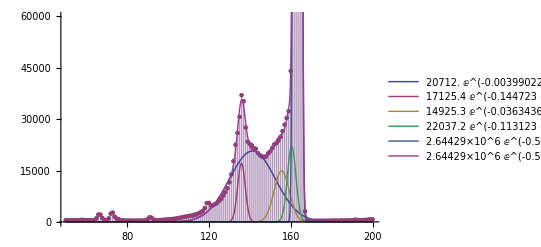

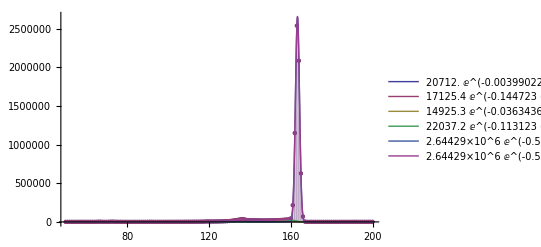

```mathematica
mu={141.3,135.9,155.3,160.3,163.3};sigma={11.1,1.8,3.8,2.1,1.0};
a={21500,18000,16000,25000,2900000};n=Length[mu];

model=NonlinearModelFit[bkgdata,G[x,Table[Symbol["mu"<>ToString[i]],{i,1,n}],Table[Symbol["sigma"<>ToString[i]],{i,1,n}],Table[Symbol["a"<>ToString[i]],{i,1,n}]],Join[Table[{Symbol["mu"<>ToString[i]],mu[[i]]},{i,1,n}],Table[{Symbol["sigma"<>ToString[i]],sigma[[i]]},{i,1,n}],Table[{Symbol["a"<>ToString[i]],a[[i]]},{i,1,n}]],x];
model["ParameterTable"]
params=model["BestFitParameters"];
paramerrors=model["ParameterErrors"];

theme="Classic";
Show[ListPlot[{viewingdata,bkgdata[[50;;200]]},Filling->Bottom,PlotTheme->theme,PlotRange->All],Plot[Evaluate@Join[Table[F[x,params[[i,2]],params[[i+n,2]],params[[i+2n,2]]],{i,1,n}],{G[x,params[[;;n,2]],params[[n+1;;2n,2]],params[[2n+1;;3n,2]]]}],{x,50,200},PlotRange->All,PlotTheme->theme,PlotLegends->"Expressions"],PlotRange->{{50,200},{0,60000}}]
Show[ListPlot[{viewingdata,bkgdata[[50;;200]]},Filling->Bottom,PlotTheme->theme,PlotRange->All],Plot[Evaluate@Join[Table[F[x,params[[i,2]],params[[i+n,2]],params[[i+2n,2]]],{i,1,n}],{G[x,params[[;;n,2]],params[[n+1;;2n,2]],params[[2n+1;;3n,2]]]}],{x,50,200},PlotRange->All,PlotTheme->theme,PlotLegends->"Expressions"],PlotRange->{{50,200},All}]
```

### Conclusion

```mathematica
Table[{params[[i,2]],paramerrors[[i]],100*paramerrors[[i]]/params[[i,2]]},{i,{5,10,15}}]//TableForm
background=Table[err[F2,{i[[1]],0},{params[[5,2]],paramerrors[[5]]},{params[[10,2]],paramerrors[[10]]},{params[[15,2]],paramerrors[[15]]}],{i,bkgdata}];
counts[3]=Total[background[[All,1]]];countserror[3]=Sqrt[Total[(background[[All,2]])^2]];{counts[3],countserror[3],100countserror[3]/counts[3]}
```

163.304 | 0.000250364 | 0.000153311
0.997692 | 0.000461816 | 0.0462885
2.64429×10^6 | 2163.15 | 0.0818044

{6.61296×10^6,3262.56,0.0493358}

```mathematica
peakbackground=Apply[err,Join[{backgroundfunction,{params[[5,2]],paramerrors[[5]]}},Table[{params[[i,2]],paramerrors[[i]]},{i,1,4}],Table[{params[[i+5,2]],paramerrors[[i]]},{i,1,4}],Table[{params[[i+10,2]],paramerrors[[i]]},{i,1,4}]]]
countsalt[3]=NIntegrate[F2[x,params[[5,2]],params[[5+5,2]],params[[5+10,2]]],{x,params[[5,2]]-2*fwhm[params[[5+5,2]]],params[[5,2]]+2*fwhm[params[[5+5,2]]]}];
countserroralt[3]=Sqrt[paramerrors[[-1]]^2+peakbackground[[2]]^2];
{countsalt[3],countserroralt[3],100*countserroralt[3]/countsalt[3]}
```

{13540.8,2045.83}

{6.61294×10^6,2977.35,0.0450231}

```mathematica
dataerr=Table[{i[[2]],0},{i,bkgdata[[Floor[params[[n,2]]-2*Sqrt[2*Log[2]]*params[[2n,2]]];;Ceiling[params[[n,2]]+2*Sqrt[2*Log[2]]*params[[2n,2]]]]]}];
background=Table[err@@Join[{F3},{{j[[1]],0}},Delete[Table[{params[[i,2]],paramerrors[[i]]},{i,3n}],Table[{i n},{i,1,3}]]],{j,bkgdata[[Floor[params[[n,2]]-2*Sqrt[2*Log[2]]*params[[2n,2]]];;Ceiling[params[[n,2]]+2*Sqrt[2*Log[2]]*params[[2n,2]]]]]}];
countsalt2[3]=Total[dataerr[[All,1]]-background[[All,1]]];
countserroralt2[3]=Sqrt[Total[(background[[All,2]])^2]];
{countsalt2[3],countserroralt2[3],100*countserroralt2[3]/countsalt2[3]}
```

{6.60736×10^6,7204.49,0.109037}

## Thick Film 2

### Data Selection

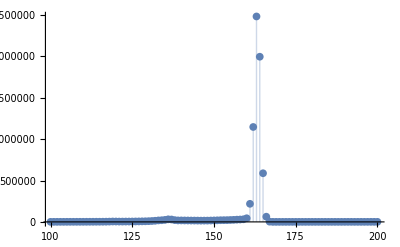

```mathematica
ListPlot[thickdata[2][[100;;200]],Filling->Bottom,PlotRange->All]
```

### NonlinearModelFit bins

```mathematica
bkgdata=thickdata[2];
viewingdata=thickdata[2][[50;;200]];
ListPlot[{viewingdata,bkgdata},Filling->Bottom,PlotRange->{{50,200},{0,60000}}]
```

-Graphics-

```mathematica
mu={141.3,135.9,155.3,160.3,163.3};sigma={11.1,1.8,3.8,2.1,1.0};
a={21500,18000,16000,25000,2900000};n=Length[mu];

model=NonlinearModelFit[bkgdata,G[x,Table[Symbol["mu"<>ToString[i]],{i,1,n}],Table[Symbol["sigma"<>ToString[i]],{i,1,n}],Table[Symbol["a"<>ToString[i]],{i,1,n}]],Join[Table[{Symbol["mu"<>ToString[i]],mu[[i]]},{i,1,n}],Table[{Symbol["sigma"<>ToString[i]],sigma[[i]]},{i,1,n}],Table[{Symbol["a"<>ToString[i]],a[[i]]},{i,1,n}]],x];
model["ParameterTable"]
params=model["BestFitParameters"];
paramerrors=model["ParameterErrors"];

theme="Classic";
Show[ListPlot[{viewingdata,bkgdata[[50;;200]]},Filling->Bottom,PlotTheme->theme,PlotRange->All],Plot[Evaluate@Join[Table[F[x,params[[i,2]],params[[i+n,2]],params[[i+2n,2]]],{i,1,n}],{G[x,params[[;;n,2]],params[[n+1;;2n,2]],params[[2n+1;;3n,2]]]}],{x,50,200},PlotRange->All,PlotTheme->theme,PlotLegends->"Expressions"],PlotRange->{{50,200},{0,60000}}]
Show[ListPlot[{viewingdata,bkgdata[[50;;200]]},Filling->Bottom,PlotTheme->theme,PlotRange->All],Plot[Evaluate@Join[Table[F[x,params[[i,2]],params[[i+n,2]],params[[i+2n,2]]],{i,1,n}],{G[x,params[[;;n,2]],params[[n+1;;2n,2]],params[[2n+1;;3n,2]]]}],{x,50,200},PlotRange->All,PlotTheme->theme,PlotLegends->"Expressions"],PlotRange->{{50,200},All}]
```

| Estimate | Standard Error | t-Statistic | P-Value
mu1 | 141.165 | 0.289069 | 488.344 | 1.0447069478×10^-6051
mu2 | 135.993 | 0.0344811 | 3943.98 | 4.9553250218×10^-13411
mu3 | 155.474 | 0.628542 | 247.356 | 4.9027875887×10^-3799
mu4 | 160.449 | 0.132567 | 1210.32 | 6.7873599495×10^-9225
mu5 | 163.284 | 0.000244386 | 668138. | 4.5160271124×10^-31636
sigma1 | 11.1457 | 0.207641 | 53.6781 | 1.7885069362×10^-538
sigma2 | 1.62207 | 0.040825 | 39.7323 | 8.0519753798×10^-316
sigma3 | 3.78775 | 0.387589 | 9.77259 | 1.9581×10^-22
sigma4 | 2.10701 | 0.210868 | 9.99206 | 2.24743×10^-23
sigma5 | 0.997406 | 0.000453112 | 2201.24 | 4.0675631697×10^-11342
a1 | 16427.2 | 167.81 | 97.8912 | 8.0147170821×10^-1380
a2 | 15008.1 | 302.578 | 49.6007 | 1.6410378831×10^-469
a3 | 14934.7 | 1219.75 | 12.2441 | 3.59439×10^-34
a4 | 22650.7 | 2920.08 | 7.75687 | 9.75385×10^-15
a5 | 2.56942×10^6 | 2057.72 | 1248.67 | 4.3276553114×10^-9335

-Graphics-

-Graphics-

### Conclusion

```mathematica
Table[{params[[i,2]],paramerrors[[i]],100*paramerrors[[i]]/params[[i,2]]},{i,{5,10,15}}]//TableForm
background=Table[err[F2,{i[[1]],0},{params[[5,2]],paramerrors[[5]]},{params[[10,2]],paramerrors[[10]]},{params[[15,2]],paramerrors[[15]]}],{i,bkgdata}];
counts[5]=Total[background[[All,1]]];countserror[5]=Sqrt[Total[(background[[All,2]])^2]];{counts[5],countserror[5],100countserror[5]/counts[5]}
```

163.284 | 0.000244386 | 0.00014967
0.997406 | 0.000453112 | 0.045429
2.56942×10^6 | 2057.72 | 0.080085

{6.42386×10^6,3104.61,0.0483293}

```mathematica
peakbackground=Apply[err,Join[{backgroundfunction,{params[[5,2]],paramerrors[[5]]}},Table[{params[[i,2]],paramerrors[[i]]},{i,1,4}],Table[{params[[i+5,2]],paramerrors[[i]]},{i,1,4}],Table[{params[[i+10,2]],paramerrors[[i]]},{i,1,4}]]]
countsalt[5]=NIntegrate[F2[x,params[[5,2]],params[[5+5,2]],params[[5+10,2]]],{x,params[[5,2]]-2*fwhm[params[[5+5,2]]],params[[5,2]]+2*fwhm[params[[5+5,2]]]}];
countserroralt[5]=Sqrt[paramerrors[[-1]]^2+peakbackground[[2]]^2];
{countsalt[5],countserroralt[5],100*countserroralt[5]/countsalt[5]}
```

{13237.7,1926.75}

{6.42385×10^6,2818.96,0.0438828}

```mathematica
dataerr=Table[{i[[2]],0},{i,bkgdata[[Floor[params[[n,2]]-2*Sqrt[2*Log[2]]*params[[2n,2]]];;Ceiling[params[[n,2]]+2*Sqrt[2*Log[2]]*params[[2n,2]]]]]}];
background=Table[err@@Join[{F3},{{j[[1]],0}},Delete[Table[{params[[i,2]],paramerrors[[i]]},{i,3n}],Table[{i n},{i,1,3}]]],{j,bkgdata[[Floor[params[[n,2]]-2*Sqrt[2*Log[2]]*params[[2n,2]]];;Ceiling[params[[n,2]]+2*Sqrt[2*Log[2]]*params[[2n,2]]]]]}];
countsalt2[5]=Total[dataerr[[All,1]]-background[[All,1]]];
countserroralt2[5]=Sqrt[Total[(background[[All,2]])^2]];
{countsalt2[5],countserroralt2[5],100*countserroralt2[5]/countsalt2[5]}
```

{6.41849×10^6,6624.24,0.103206}

## Thin Film 1

### Data Selection

```mathematica
ListPlot[thindata[1][[100;;200]],Filling->Bottom,PlotRange->All]
```

-Graphics-

### NonlinearModelFit bins

```mathematica
bkgdata=thindata[1];
viewingdata=thindata[1][[50;;200]];
ListPlot[{viewingdata,bkgdata},Filling->Bottom,PlotRange->{{50,200},{0,60000}}]
```

-Graphics-

```mathematica
mu={141.3,135.9,155.3,160.3,163.3};sigma={11.1,1.8,3.8,2.1,1.0};
a={21500,18000,16000,25000,2900000};n=Length[mu];

model=NonlinearModelFit[bkgdata,G[x,Table[Symbol["mu"<>ToString[i]],{i,1,n}],Table[Symbol["sigma"<>ToString[i]],{i,1,n}],Table[Symbol["a"<>ToString[i]],{i,1,n}]],Join[Table[{Symbol["mu"<>ToString[i]],mu[[i]]},{i,1,n}],Table[{Symbol["sigma"<>ToString[i]],sigma[[i]]},{i,1,n}],Table[{Symbol["a"<>ToString[i]],a[[i]]},{i,1,n}]],x];
model["ParameterTable"]
params=model["BestFitParameters"];
paramerrors=model["ParameterErrors"];

theme="Classic";
Show[ListPlot[{viewingdata,bkgdata[[50;;200]]},Filling->Bottom,PlotTheme->theme,PlotRange->All],Plot[Evaluate@Join[Table[F[x,params[[i,2]],params[[i+n,2]],params[[i+2n,2]]],{i,1,n}],{G[x,params[[;;n,2]],params[[n+1;;2n,2]],params[[2n+1;;3n,2]]]}],{x,50,200},PlotRange->All,PlotTheme->theme,PlotLegends->"Expressions"],PlotRange->{{50,200},{0,60000}}]
Show[ListPlot[{viewingdata,bkgdata[[50;;200]]},Filling->Bottom,PlotTheme->theme,PlotRange->All],Plot[Evaluate@Join[Table[F[x,params[[i,2]],params[[i+n,2]],params[[i+2n,2]]],{i,1,n}],{G[x,params[[;;n,2]],params[[n+1;;2n,2]],params[[2n+1;;3n,2]]]}],{x,50,200},PlotRange->All,PlotTheme->theme,PlotLegends->"Expressions"],PlotRange->{{50,200},All}]
```

| Estimate | Standard Error | t-Statistic | P-Value
mu1 | 141.429 | 0.241421 | 585.821 | 5.8259439115×10^-6680
mu2 | 135.97 | 0.0330989 | 4107.98 | 1.2140768631×10^-13555
mu3 | 155.497 | 0.683101 | 227.635 | 2.0417699358×10^-3541
mu4 | 160.418 | 0.127713 | 1256.08 | 5.5695794529×10^-9356
mu5 | 163.35 | 0.000237539 | 687676. | 1.9849491329×10^-31738
sigma1 | 11.1805 | 0.170727 | 65.4875 | 3.1082514091×10^-751
sigma2 | 1.79305 | 0.0397712 | 45.0841 | 1.2841847737×10^-396
sigma3 | 3.72148 | 0.403187 | 9.23016 | 3.38582×10^-20
sigma4 | 2.13944 | 0.219475 | 9.74797 | 2.48933×10^-22
sigma5 | 0.9982 | 0.000434891 | 2295.29 | 1.8576283431×10^-11490
a1 | 21432.7 | 192.729 | 111.206 | 1.9997033802×10^-1638
a2 | 18318.2 | 325.657 | 56.25 | 2.5799394313×10^-583
a3 | 16036.9 | 1454.83 | 11.0232 | 4.65225×10^-28
a4 | 24270.7 | 3384.7 | 7.17071 | 8.11139×10^-13
a5 | 2.88027×10^6 | 2125.14 | 1355.33 | 9.2505863207×10^-9625

-Graphics-

-Graphics-

### Conclusion

```mathematica
Table[{params[[i,2]],paramerrors[[i]],100*paramerrors[[i]]/params[[i,2]]},{i,{5,10,15}}]//TableForm
background=Table[err[F2,{i[[1]],0},{params[[5,2]],paramerrors[[5]]},{params[[10,2]],paramerrors[[10]]},{params[[15,2]],paramerrors[[15]]}],{i,bkgdata}];
counts[4]=Total[background[[All,1]]];countserror[4]=Sqrt[Total[(background[[All,2]])^2]];{counts[4],countserror[4],100countserror[4]/counts[4]}
```

163.35 | 0.000237539 | 0.000145417
0.9982 | 0.000434891 | 0.0435675
2.88027×10^6 | 2125.14 | 0.0737827

{7.20677×10^6,3237.84,0.0449277}

```mathematica
peakbackground=Apply[err,Join[{backgroundfunction,{params[[5,2]],paramerrors[[5]]}},Table[{params[[i,2]],paramerrors[[i]]},{i,1,4}],Table[{params[[i+5,2]],paramerrors[[i]]},{i,1,4}],Table[{params[[i+10,2]],paramerrors[[i]]},{i,1,4}]]]
countsalt[4]=NIntegrate[F2[x,params[[5,2]],params[[5+5,2]],params[[5+10,2]]],{x,params[[5,2]]-2*fwhm[params[[5+5,2]]],params[[5,2]]+2*fwhm[params[[5+5,2]]]}];
countserroralt[4]=Sqrt[paramerrors[[-1]]^2+peakbackground[[2]]^2];
{countsalt[4],countserroralt[4],100*countserroralt[4]/countsalt[4]}
```

{14359.7,2066.76}

{7.20675×10^6,2964.41,0.0411338}

```mathematica
dataerr=Table[{i[[2]],0},{i,bkgdata[[Floor[params[[n,2]]-2*Sqrt[2*Log[2]]*params[[2n,2]]];;Ceiling[params[[n,2]]+2*Sqrt[2*Log[2]]*params[[2n,2]]]]]}];
background=Table[err@@Join[{F3},{{j[[1]],0}},Delete[Table[{params[[i,2]],paramerrors[[i]]},{i,3n}],Table[{i n},{i,1,3}]]],{j,bkgdata[[Floor[params[[n,2]]-2*Sqrt[2*Log[2]]*params[[2n,2]]];;Ceiling[params[[n,2]]+2*Sqrt[2*Log[2]]*params[[2n,2]]]]]}];
countsalt2[4]=Total[dataerr[[All,1]]-background[[All,1]]];
countserroralt2[4]=Sqrt[Total[(background[[All,2]])^2]];
{countsalt2[4],countserroralt2[4],100*countserroralt2[4]/countsalt2[4]}
```

{7.20084×10^6,7562.53,0.105023}

## Thin Film 2

### Data Selection

```mathematica
ListPlot[thindata[2][[100;;200]],Filling->Bottom,PlotRange->All]
```

-Graphics-

### NonlinearModelFit bins

```mathematica
bkgdata=thindata[2];
viewingdata=thindata[2][[50;;200]];
ListPlot[{viewingdata,bkgdata},Filling->Bottom,PlotRange->{{50,200},{0,60000}}]
```

-Graphics-

```mathematica
mu={141.3,135.9,155.3,160.3,163.3};sigma={11.1,1.8,3.8,2.1,1.0};
a={21500,18000,16000,25000,2900000};n=Length[mu];

model=NonlinearModelFit[bkgdata,G[x,Table[Symbol["mu"<>ToString[i]],{i,1,n}],Table[Symbol["sigma"<>ToString[i]],{i,1,n}],Table[Symbol["a"<>ToString[i]],{i,1,n}]],Join[Table[{Symbol["mu"<>ToString[i]],mu[[i]]},{i,1,n}],Table[{Symbol["sigma"<>ToString[i]],sigma[[i]]},{i,1,n}],Table[{Symbol["a"<>ToString[i]],a[[i]]},{i,1,n}]],x];
model["ParameterTable"]
params=model["BestFitParameters"];
paramerrors=model["ParameterErrors"];

theme="Classic";
Show[ListPlot[{viewingdata,bkgdata[[50;;200]]},Filling->Bottom,PlotTheme->theme,PlotRange->All],Plot[Evaluate@Join[Table[F[x,params[[i,2]],params[[i+n,2]],params[[i+2n,2]]],{i,1,n}],{G[x,params[[;;n,2]],params[[n+1;;2n,2]],params[[2n+1;;3n,2]]]}],{x,50,200},PlotRange->All,PlotTheme->theme,PlotLegends->"Expressions"],PlotRange->{{50,200},{0,60000}}]
Show[ListPlot[{viewingdata,bkgdata[[50;;200]]},Filling->Bottom,PlotTheme->theme,PlotRange->All],Plot[Evaluate@Join[Table[F[x,params[[i,2]],params[[i+n,2]],params[[i+2n,2]]],{i,1,n}],{G[x,params[[;;n,2]],params[[n+1;;2n,2]],params[[2n+1;;3n,2]]]}],{x,50,200},PlotRange->All,PlotTheme->theme,PlotLegends->"Expressions"],PlotRange->{{50,200},All}]
```

| Estimate | Standard Error | t-Statistic | P-Value
mu1 | 141.321 | 0.30795 | 458.909 | 1.0508177992×10^-5838
mu2 | 135.995 | 0.0349028 | 3896.38 | 6.2038976886×10^-13368
mu3 | 155.463 | 0.632392 | 245.833 | 1.0412884661×10^-3779
mu4 | 160.453 | 0.130636 | 1228.24 | 8.161985807×10^-9277
mu5 | 163.296 | 0.000234199 | 697254. | 1.5034296192×10^-31787
sigma1 | 11.1011 | 0.215676 | 51.4715 | 8.2737505641×10^-501
sigma2 | 1.5986 | 0.0411596 | 38.839 | 5.43309×10^-303
sigma3 | 3.83658 | 0.391738 | 9.79376 | 1.59241×10^-22
sigma4 | 2.12245 | 0.211039 | 10.0571 | 1.17248×10^-23
sigma5 | 0.996866 | 0.000440289 | 2264.12 | 5.5521727369×10^-11442
a1 | 17110.7 | 180.809 | 94.6341 | 5.4802153086×10^-1316
a2 | 15691.3 | 323.817 | 48.4571 | 1.0990075173×10^-450
a3 | 16276.2 | 1341.61 | 12.1318 | 1.39111×10^-33
a4 | 24342.7 | 3172.93 | 7.67201 | 1.88823×10^-14
a5 | 2.80719×10^6 | 2165.61 | 1296.26 | 3.0519573862×10^-9467

-Graphics-

-Graphics-

### Conclusion

```mathematica
Table[{params[[i,2]],paramerrors[[i]],100*paramerrors[[i]]/params[[i,2]]},{i,{5,10,15}}]//TableForm
background=Table[err[F2,{i[[1]],0},{params[[5,2]],paramerrors[[5]]},{params[[10,2]],paramerrors[[10]]},{params[[15,2]],paramerrors[[15]]}],{i,bkgdata}];
counts[6]=Total[background[[All,1]]];countserror[6]=Sqrt[Total[(background[[All,2]])^2]];{counts[6],countserror[6],100countserror[6]/counts[6]}
```

163.296 | 0.000234199 | 0.00014342
0.996866 | 0.000440289 | 0.0441673
2.80719×10^6 | 2165.61 | 0.077145

{7.01453×10^6,3271.4,0.0466375}

```mathematica
peakbackground=Apply[err,Join[{backgroundfunction,{params[[5,2]],paramerrors[[5]]}},Table[{params[[i,2]],paramerrors[[i]]},{i,1,4}],Table[{params[[i+5,2]],paramerrors[[i]]},{i,1,4}],Table[{params[[i+10,2]],paramerrors[[i]]},{i,1,4}]]]
countsalt[6]=NIntegrate[F2[x,params[[5,2]],params[[5+5,2]],params[[5+10,2]]],{x,params[[5,2]]-2*fwhm[params[[5+5,2]]],params[[5,2]]+2*fwhm[params[[5+5,2]]]}];
countserroralt[6]=Sqrt[paramerrors[[-1]]^2+peakbackground[[2]]^2];
{countsalt[6],countserroralt[6],100*countserroralt[6]/countsalt[6]}
```

{14362.5,2087.37}

{7.01451×10^6,3007.82,0.04288}

```mathematica
dataerr=Table[{i[[2]],0},{i,bkgdata[[Floor[params[[n,2]]-2*Sqrt[2*Log[2]]*params[[2n,2]]];;Ceiling[params[[n,2]]+2*Sqrt[2*Log[2]]*params[[2n,2]]]]]}];
background=Table[err@@Join[{F3},{{j[[1]],0}},Delete[Table[{params[[i,2]],paramerrors[[i]]},{i,3n}],Table[{i n},{i,1,3}]]],{j,bkgdata[[Floor[params[[n,2]]-2*Sqrt[2*Log[2]]*params[[2n,2]]];;Ceiling[params[[n,2]]+2*Sqrt[2*Log[2]]*params[[2n,2]]]]]}];
countsalt2[6]=Total[dataerr[[All,1]]-background[[All,1]]];
countserroralt2[6]=Sqrt[Total[(background[[All,2]])^2]];
{countsalt2[6],countserroralt2[6],100*countserroralt2[6]/countsalt2[6]}
```

{7.00869×10^6,7207.72,0.10284}

## Calculations

### Method 1

```mathematica
thickness=40;thicknesserror=0.01;
Print["Peak Data\n",Table[{counts[i],countserror[i],100*countserror[i]/counts[i]},{i,{1,3,4,2,5,6}}]//TableForm,"\n"]
coeff[counts1_,counts3_,thickness_]:=(-Log[counts3/counts1])/thickness;


attencoeff=err[coeff,{counts[1],countserror[1]},{counts[3],countserror[3]},{thickness,thicknesserror}]
thinmeasure=err[coeff,{counts[1],countserror[1]},{counts[4],countserror[4]},attencoeff];Join[thinmeasure,{100*thinmeasure[[2]]/thinmeasure[[1]]}]

attencoeff=err[coeff,{counts[2],countserror[2]},{counts[5],countserror[5]},{thickness,thicknesserror}]
thinmeasure=err[coeff,{counts[2],countserror[2]},{counts[6],countserror[6]},attencoeff];Join[thinmeasure,{100*thinmeasure[[2]]/thinmeasure[[1]]}]

thick[counts1_,counts2_,counts3_,thickness_]:=thickness Log[counts3/counts1]/Log[counts2/counts1]
thinmeasure=err[thick,{counts[1],countserror[1]},{counts[3],countserror[3]},{counts[4],countserror[4]},{thickness,thicknesserror}];
Join[thinmeasure,{100*thinmeasure[[2]]/thinmeasure[[1]]}]

thinmeasure=err[thick,{counts[2],countserror[2]},{counts[5],countserror[5]},{counts[6],countserror[6]},{thickness,thicknesserror}];
Join[thinmeasure,{100*thinmeasure[[2]]/thinmeasure[[1]]}]
```

Peak Data
7.28393×10^6 | 3199.52 | 0.0439257
6.61296×10^6 | 3262.56 | 0.0493358
7.20677×10^6 | 3237.84 | 0.0449277
7.09155×10^6 | 3083.65 | 0.0434835
6.42386×10^6 | 3104.61 | 0.0483293
7.01453×10^6 | 3271.4 | 0.0466375

{0.00241601,0.0000165252}

{4.40827,0.261811,5.93908}

{0.0024721,0.0000162647}

{4.41735,0.259567,5.87608}

{4.40827,0.247506,5.61458}

{4.41735,0.246052,5.57012}

### Method 2

```mathematica
thickness=40;thicknesserror=0.01;
Print["Peak Data\n",Table[{countsalt[i],countserroralt[i],100*countserroralt[i]/countsalt[i]},{i,{1,3,4,2,5,6}}]//TableForm,"\n"]
coeff[counts1_,counts3_,thickness_]:=(-Log[counts3/counts1])/thickness;


attencoeff=err[coeff,{countsalt[1],countserroralt[1]},{countsalt[3],countserroralt[3]},{thickness,thicknesserror}]
thinmeasure=err[coeff,{countsalt[1],countserroralt[1]},{countsalt[4],countserroralt[4]},attencoeff];Join[thinmeasure,{100*thinmeasure[[2]]/thinmeasure[[1]]}]

attencoeff=err[coeff,{countsalt[2],countserroralt[2]},{countsalt[5],countserroralt[5]},{thickness,thicknesserror}]
thinmeasure=err[coeff,{countsalt[2],countserroralt[2]},{countsalt[6],countserroralt[6]},attencoeff];Join[thinmeasure,{100*thinmeasure[[2]]/thinmeasure[[1]]}]

thick[counts1_,counts2_,counts3_,thickness_]:=thickness Log[counts3/counts1]/Log[counts2/counts1]
thinmeasure=err[thick,{countsalt[1],countserroralt[1]},{countsalt[3],countserroralt[3]},{countsalt[4],countserroralt[4]},{thickness,thicknesserror}];
Join[thinmeasure,{100*thinmeasure[[2]]/thinmeasure[[1]]}]

thinmeasure=err[thick,{countsalt[2],countserroralt[2]},{countsalt[5],countserroralt[5]},{countsalt[6],countserroralt[6]},{thickness,thicknesserror}];
Join[thinmeasure,{100*thinmeasure[[2]]/thinmeasure[[1]]}]
```

Peak Data
7.28392×10^6 | 2917.92 | 0.0400598
6.61294×10^6 | 2977.35 | 0.0450231
7.20675×10^6 | 2964.41 | 0.0411338
7.09153×10^6 | 2805.7 | 0.0395641
6.42385×10^6 | 2818.96 | 0.0438828
7.01451×10^6 | 3007.82 | 0.04288

{0.00241601,0.0000150783}

{4.40827,0.239241,5.42711}

{0.0024721,0.0000147841}

{4.41735,0.237483,5.37613}

{4.40827,0.226223,5.13178}

{4.41735,0.225257,5.09937}

### Method 3

```mathematica
thickness=40;thicknesserror=0.01;
Print["Peak Data\n",Table[{countsalt2[i],countserroralt2[i],100*countserroralt2[i]/countsalt2[i]},{i,{1,3,4,2,5,6}}]//TableForm,"\n"]
coeff[counts1_,counts3_,thickness_]:=(-Log[counts3/counts1])/thickness;


attencoeff=err[coeff,{countsalt2[1],countserroralt2[1]},{countsalt2[3],countserroralt2[3]},{thickness,thicknesserror}]
thinmeasure=err[coeff,{countsalt2[1],countserroralt2[1]},{countsalt2[4],countserroralt2[4]},attencoeff];Join[thinmeasure,{100*thinmeasure[[2]]/thinmeasure[[1]]}]

attencoeff=err[coeff,{countsalt2[2],countserroralt2[2]},{countsalt2[5],countserroralt2[5]},{thickness,thicknesserror}]
thinmeasure=err[coeff,{countsalt2[2],countserroralt2[2]},{countsalt2[6],countserroralt2[6]},attencoeff];Join[thinmeasure,{100*thinmeasure[[2]]/thinmeasure[[1]]}]

thick[counts1_,counts2_,counts3_,thickness_]:=thickness Log[counts3/counts1]/Log[counts2/counts1]
thinmeasure=err[thick,{countsalt2[1],countserroralt2[1]},{countsalt2[3],countserroralt2[3]},{countsalt2[4],countserroralt2[4]},{thickness,thicknesserror}];
Join[thinmeasure,{100*thinmeasure[[2]]/thinmeasure[[1]]}]

thinmeasure=err[thick,{countsalt2[2],countserroralt2[2]},{countsalt2[5],countserroralt2[5]},{countsalt2[6],countserroralt2[6]},{thickness,thicknesserror}];
Join[thinmeasure,{100*thinmeasure[[2]]/thinmeasure[[1]]}]
```

Peak Data
7.27808×10^6 | 7333.46 | 0.100761
6.60736×10^6 | 7204.49 | 0.109037
7.20084×10^6 | 7562.53 | 0.105023
7.08611×10^6 | 6870. | 0.0969502
6.41849×10^6 | 6624.24 | 0.103206
7.00869×10^6 | 7207.72 | 0.10284

{0.00241707,0.0000371212}

{4.41399,0.605948,13.7279}

{0.00247386,0.0000354056}

{4.44057,0.574834,12.945}

{4.41399,0.573427,12.9911}

{4.44057,0.544365,12.2589}

# Data Set 5

```mathematica
ClearAll["Global`*"]
(*~ MacOS ~*)
main="/Users/mikhailgaerlan/Box Sync/Education/MSU/Research/Radiation Thickness/Data";

SetDirectory[main];
$Line=0;
```

## Data Import

## Source 1-Hour

### Trial 1

```mathematica
imported=Import["Am-241-24hr-NewConfiguration.Spe","Data"];
times=ToExpression[StringSplit[imported[[10]]]];
deadtime=N[Abs[times[[1]]-times[[2]]]/times[[2]]];
imported[[;;15]]//TableForm
imported[[-16;;]]//TableForm
freq=ToExpression[imported[[13;;-15]]]/(1-deadtime);
sourcedata[1]=Table[{i,freq[[i]]},{i,Length[freq]}];
ListPlot[sourcedata[1][[155;;170]],PlotRange->All,Filling->Bottom]
```

$SPEC_ID:
No sample description was entered.
$SPEC_REM:
DET# 1
DETDESC# HPGe Detector 1
AP# GammaVision Version 6.07
$DATE_MEA:
02/08/2016 09:15:57
$MEAS_TIM:
86400 94500
$DATA:
0 8191
       0
       0
       0

1
       9
$ROI:
0
$PRESETS:
Live Time
86400
0
$ENER_FIT:
0.137869 0.366631
$MCA_CAL:
3
1.378689E-001 3.666307E-001 -4.415950E-008 keV
$SHAPE_CAL:
3
2.301834E+000 9.195991E-004 -5.357180E-008

-Graphics-

### Trial 2

```mathematica
imported=Import["Am-241-24hr-NewConfiguration-2.Spe","Data"];
times=ToExpression[StringSplit[imported[[10]]]];
deadtime=N[Abs[times[[1]]-times[[2]]]/times[[2]]];
imported[[;;15]]//TableForm
imported[[-16;;]]//TableForm
freq=ToExpression[imported[[13;;-15]]]/(1-deadtime);
sourcedata[2]=Table[{i,freq[[i]]},{i,Length[freq]}];
ListPlot[sourcedata[2][[155;;170]],PlotRange->All,Filling->Bottom]
```

$SPEC_ID:
Molnar Range
$SPEC_REM:
DET# 1
DETDESC# HPGe Detector 1
AP# GammaVision Version 6.07
$DATE_MEA:
02/10/2016 08:09:32
$MEAS_TIM:
86400 94490
$DATA:
0 8191
       0
       0
       0

2
       9
$ROI:
0
$PRESETS:
Live Time
86400
0
$ENER_FIT:
0.137869 0.366631
$MCA_CAL:
3
1.378689E-001 3.666307E-001 -4.415950E-008 keV
$SHAPE_CAL:
3
2.301834E+000 9.195991E-004 -5.357180E-008

-Graphics-

## Thick Film

### Trial 1

```mathematica
imported=Import["Am-241-24hr-ThickFilm-NewConfiguration.Spe","Data"];
times=ToExpression[StringSplit[imported[[10]]]];
deadtime=N[Abs[times[[1]]-times[[2]]]/times[[2]]];
imported[[;;15]]//TableForm
imported[[-16;;]]//TableForm
freq=ToExpression[imported[[13;;-15]]]/(1-deadtime);
thickdata[1]=Table[{i,freq[[i]]},{i,Length[freq]}];
ListPlot[thickdata[1][[155;;170]],PlotRange->All,Filling->Bottom]
```

$SPEC_ID:
Molnar Range
$SPEC_REM:
DET# 1
DETDESC# HPGe Detector 1
AP# GammaVision Version 6.07
$DATE_MEA:
02/05/2016 08:32:06
$MEAS_TIM:
86400 93811
$DATA:
0 8191
       0
       0
       0

0
       6
$ROI:
0
$PRESETS:
Live Time
86400
0
$ENER_FIT:
0.137869 0.366631
$MCA_CAL:
3
1.378689E-001 3.666307E-001 -4.415950E-008 keV
$SHAPE_CAL:
3
2.301834E+000 9.195991E-004 -5.357180E-008

-Graphics-

### Trial 2

```mathematica
imported=Import["Am-241-24hr-ThickFilm-NewConfiguration-2.Spe","Data"];
times=ToExpression[StringSplit[imported[[10]]]];
deadtime=N[Abs[times[[1]]-times[[2]]]/times[[2]]];
imported[[;;15]]//TableForm
imported[[-16;;]]//TableForm
freq=ToExpression[imported[[13;;-15]]]/(1-deadtime);
thickdata[2]=Table[{i,freq[[i]]},{i,Length[freq]}];
ListPlot[thickdata[2][[155;;170]],PlotRange->All,Filling->Bottom]
```

$SPEC_ID:
Molnar Range
$SPEC_REM:
DET# 1
DETDESC# HPGe Detector 1
AP# GammaVision Version 6.07
$DATE_MEA:
02/11/2016 10:43:22
$MEAS_TIM:
86400 93832
$DATA:
0 8191
       0
       0
       0

1
       7
$ROI:
0
$PRESETS:
Live Time
86400
0
$ENER_FIT:
0.137869 0.366631
$MCA_CAL:
3
1.378689E-001 3.666307E-001 -4.415950E-008 keV
$SHAPE_CAL:
3
2.301834E+000 9.195991E-004 -5.357180E-008

-Graphics-

## Thin Film

### Trial 1

```mathematica
imported=Import["Am-241-24hr-ThinFilm-NewConfiguration.Spe","Data"];
times=ToExpression[StringSplit[imported[[10]]]];
deadtime=N[Abs[times[[1]]-times[[2]]]/times[[2]]];
imported[[;;15]]//TableForm
imported[[-16;;]]//TableForm
freq=ToExpression[imported[[13;;-15]]]/(1-deadtime);
thindata[1]=Table[{i,freq[[i]]},{i,Length[freq]}];
ListPlot[thindata[1][[155;;170]],PlotRange->All,Filling->Bottom]
```

$SPEC_ID:
Molnar Range
$SPEC_REM:
DET# 1
DETDESC# HPGe Detector 1
AP# GammaVision Version 6.07
$DATE_MEA:
02/03/2016 15:57:41
$MEAS_TIM:
86400 94406
$DATA:
0 8191
       0
       0
       0

5
       6
$ROI:
0
$PRESETS:
Live Time
86400
0
$ENER_FIT:
0.137869 0.366631
$MCA_CAL:
3
1.378689E-001 3.666307E-001 -4.415950E-008 keV
$SHAPE_CAL:
3
2.301834E+000 9.195991E-004 -5.357180E-008

-Graphics-

### Trial 2

```mathematica
imported=Import["Am-241-24hr-ThinFilm-NewConfiguration-2.Spe","Data"];
times=ToExpression[StringSplit[imported[[10]]]];
deadtime=N[Abs[times[[1]]-times[[2]]]/times[[2]]];
imported[[;;15]]//TableForm
imported[[-16;;]]//TableForm
freq=ToExpression[imported[[13;;-15]]]/(1-deadtime);
thindata[2]=Table[{i,freq[[i]]},{i,Length[freq]}];
ListPlot[thindata[2][[155;;170]],PlotRange->All,Filling->Bottom]
```

$SPEC_ID:
Molnar Range
$SPEC_REM:
DET# 1
DETDESC# HPGe Detector 1
AP# GammaVision Version 6.07
$DATE_MEA:
02/16/2016 08:08:51
$MEAS_TIM:
86400 94431
$DATA:
0 8191
       0
       0
       0

4
       3
$ROI:
0
$PRESETS:
Live Time
86400
0
$ENER_FIT:
0.137869 0.366631
$MCA_CAL:
3
1.378689E-001 3.666307E-001 -4.415950E-008 keV
$SHAPE_CAL:
3
2.301834E+000 9.195991E-004 -5.357180E-008

-Graphics-

## Data Analysis

## Equations

```mathematica
F[x_,mu_,sigma_,a_]:=a*Exp[-1/2*((x-mu)/sigma)^2]
F2[x_,mu_,sigma_,a_]:=a*Exp[-1/2*((x-mu)/sigma)^2]
F3[x_,mu1_,mu2_,mu3_,mu4_,sigma1_,sigma2_,sigma3_,sigma4_,a1_,a2_,a3_,a4_]:=F[x,mu1,sigma1,a1]+F[x,mu2,sigma2,a2]+F[x,mu3,sigma3,a3]+F[x,mu4,sigma4,a4]
G[x_,mu_,sigma_,a_]:=Sum[F[x,mu[[i]],sigma[[i]],a[[i]]],{i,1,Length[mu]}]

chisq2[data_,mu_,sigma_,a_]:=Sum[(data[[i,2]]-G[data[[i,1]],mu,sigma,a])^2,{i,Length[data]}]
backgroundfunction[x_,mu1_,mu2_,mu3_,mu4_,sigma1_,sigma2_,sigma3_,sigma4_,a1_,a2_,a3_,a4_]:=F2[x,mu1,sigma1,a1]+F2[x,mu2,sigma2,a2]+F2[x,mu3,sigma3,a3]+F2[x,mu4,sigma4,a4];
fwhm[sigma_]:=2*sigma*Sqrt[2*Log[2]];

err[F_,w__]:={F[Map[First,List[w]]/.List->Sequence],Block[{parms=Table[Unique[],{x,1,Length[List[w]]}],values=Table[List[w][[i,1]],{i,1,Length[List[w]]}],errors=Table[List[w][[i,2]],{i,1,Length[List[w]]}]},Sqrt[Total[Table[(D[F[parms/.List->Sequence],parms[[i]]]*errors[[i]])^2,{i,1,Length[values]}]/.Table[parms[[i]]->values[[i]],{i,1,Length[values]}]]]]}
```

## Source 1-hr Trial 1

### Data Selection

```mathematica
ListPlot[sourcedata[1][[100;;200]],Filling->Bottom,PlotRange->All]
```

-Graphics-

### NonlinearModelFit bins

```mathematica
bkgdata=sourcedata[1];
viewingdata=sourcedata[1][[50;;200]];
ListPlot[{viewingdata,bkgdata},Filling->Bottom,PlotRange->{{50,200},{0,2000000}}]
```

-Graphics-

```mathematica
mu=162.3;sigma=1.0;a=730000;

model=NonlinearModelFit[bkgdata,F[x,mu1,sigma1,a1],{{mu1,mu},{sigma1,sigma},{a1,a}},x];
model["ParameterTable"]
params=model["BestFitParameters"];
paramerrors=model["ParameterErrors"];
Max[bkgdata]

theme="Classic";
Show[ListPlot[{viewingdata,bkgdata[[50;;200]]},Filling->Bottom,PlotTheme->theme,PlotRange->All],Plot[model[x],{x,50,200},PlotTheme->theme,PlotRange->All]]
```

| Estimate | Standard Error | t-Statistic | P-Value
mu1 | 163.228 | 0.00059038 | 276480. | 7.610154481×10^-28542
sigma1 | 1.00865 | 0.000589746 | 1710.31 | 1.0961378568×10^-10460
a1 | 7.52069×10^7 | 38102.3 | 1973.81 | 4.7133893898×10^-10969

7.33216×10^7

-Graphics-

```mathematica
mu={141.3,135.9,155.3,160.3,163.3};sigma={11.1,1.8,3.8,2.1,1.0};
a={520000,450000,418000,620000,74900000};n=Length[mu];

model=NonlinearModelFit[bkgdata,G[x,Table[Symbol["mu"<>ToString[i]],{i,1,n}],Table[Symbol["sigma"<>ToString[i]],{i,1,n}],Table[Symbol["a"<>ToString[i]],{i,1,n}]],Join[Table[{Symbol["mu"<>ToString[i]],mu[[i]]},{i,1,n}],Table[{Symbol["sigma"<>ToString[i]],sigma[[i]]},{i,1,n}],Table[{Symbol["a"<>ToString[i]],a[[i]]},{i,1,n}]],x];
model["ParameterTable"]
params=model["BestFitParameters"];
paramerrors=model["ParameterErrors"];

theme="Classic";
Show[ListPlot[{viewingdata,bkgdata[[50;;200]]},Filling->Bottom,PlotTheme->theme,PlotRange->All],Plot[Evaluate@Join[Table[F[x,params[[i,2]],params[[i+n,2]],params[[i+2n,2]]],{i,1,n}],{G[x,params[[;;n,2]],params[[n+1;;2n,2]],params[[2n+1;;3n,2]]]}],{x,50,200},PlotRange->All,PlotTheme->theme,PlotLegends->"Expressions"],PlotRange->{{50,200},{0,2000000}}]
Show[ListPlot[{viewingdata,bkgdata[[50;;200]]},Filling->Bottom,PlotTheme->theme,PlotRange->All],Plot[Evaluate@Join[Table[F[x,params[[i,2]],params[[i+n,2]],params[[i+2n,2]]],{i,1,n}],{G[x,params[[;;n,2]],params[[n+1;;2n,2]],params[[2n+1;;3n,2]]]}],{x,50,200},PlotRange->All,PlotTheme->theme,PlotLegends->"Expressions"],PlotRange->{{50,200},All}]
```

| Estimate | Standard Error | t-Statistic | P-Value
mu1 | 141.282 | 0.25358 | 557.152 | 3.9500676154×10^-6506
mu2 | 135.882 | 0.0329185 | 4127.84 | 9.3915116196×10^-13573
mu3 | 155.34 | 0.628761 | 247.058 | 2.9230748894×10^-3795
mu4 | 160.315 | 0.124379 | 1288.93 | 3.3664346089×10^-9447
mu5 | 163.235 | 0.000233226 | 699901. | 5.2420542884×10^-31801
sigma1 | 11.1238 | 0.178596 | 62.285 | 5.9001830293×10^-692
sigma2 | 1.75546 | 0.0394439 | 44.5051 | 1.4343136319×10^-387
sigma3 | 3.76154 | 0.382288 | 9.83956 | 1.01642×10^-22
sigma4 | 2.126 | 0.209687 | 10.1389 | 5.14725×10^-24
sigma5 | 0.999752 | 0.000411108 | 2431.85 | 2.1510793239×10^-11695
a1 | 521871. | 4828.24 | 108.087 | 2.6665493859×10^-1578
a2 | 455567. | 8206.08 | 55.5158 | 2.043992836×10^-570
a3 | 418421. | 34513.2 | 12.1235 | 1.53663×10^-33
a4 | 623681. | 80869.7 | 7.71217 | 1.38249×10^-14
a5 | 7.49903×10^7 | 53381.8 | 1404.79 | 1.6693443268×10^-9751

-Graphics-

-Graphics-

```mathematica
ListPlot[{Table[{i[[1]],i[[2]]-G[i[[1]],params[[;;n-1,2]],params[[n+1;;2n-1,2]],params[[2n+1;;3n-1,2]]]},{i,bkgdata}],bkgdata},PlotRange->{{0,200},{0,2000000}},PlotTheme->theme]
```

-Graphics-

### Conclusion

```mathematica
Table[{params[[i,2]],paramerrors[[i]],100*paramerrors[[i]]/params[[i,2]]},{i,{5,10,15}}]//TableForm
background=Table[err[F2,{i[[1]],0},{params[[5,2]],paramerrors[[5]]},{params[[10,2]],paramerrors[[10]]},{params[[15,2]],paramerrors[[15]]}],{i,bkgdata}];
counts[1]=Total[background[[All,1]]];countserror[1]=Sqrt[Total[(background[[All,2]])^2]];{counts[1],countserror[1],100countserror[1]/counts[1]}
```

163.235 | 0.000233226 | 0.000142877
0.999752 | 0.000411108 | 0.041121
7.49903×10^7 | 53381.8 | 0.0711849

{1.87926×10^8,81151.7,0.0431827}

```mathematica
peakbackground=Apply[err,Join[{backgroundfunction,{params[[5,2]],paramerrors[[5]]}},Table[{params[[i,2]],paramerrors[[i]]},{i,1,4}],Table[{params[[i+5,2]],paramerrors[[i]]},{i,1,4}],Table[{params[[i+10,2]],paramerrors[[i]]},{i,1,4}]]]
countsalt[1]=NIntegrate[F2[x,params[[5,2]],params[[5+5,2]],params[[5+10,2]]],{x,params[[5,2]]-2*fwhm[params[[5+5,2]]],params[[5,2]]+2*fwhm[params[[5+5,2]]]}];
countserroralt[1]=Sqrt[paramerrors[[-1]]^2+peakbackground[[2]]^2];
{countsalt[1],countserroralt[1],100*countserroralt[1]/countsalt[1]}
```

{363562.,50761.9}

{1.87926×10^8,73664.,0.0391985}

```mathematica
dataerr=Table[{i[[2]],0},{i,bkgdata[[Floor[params[[n,2]]-2*Sqrt[2*Log[2]]*params[[2n,2]]];;Ceiling[params[[n,2]]+2*Sqrt[2*Log[2]]*params[[2n,2]]]]]}];
background=Table[err@@Join[{F3},{{j[[1]],0}},Delete[Table[{params[[i,2]],paramerrors[[i]]},{i,3n}],Table[{i n},{i,1,3}]]],{j,bkgdata[[Floor[params[[n,2]]-2*Sqrt[2*Log[2]]*params[[2n,2]]];;Ceiling[params[[n,2]]+2*Sqrt[2*Log[2]]*params[[2n,2]]]]]}];
countsalt2[1]=Total[dataerr[[All,1]]-background[[All,1]]];
countserroralt2[1]=Sqrt[Total[(background[[All,2]])^2]];
{countsalt2[1],countserroralt2[1],100*countserroralt2[1]/countsalt2[1]}
```

{1.87785×10^8,179744.,0.095718}

## Source 1-hr Trial 2

### Data Selection

```mathematica
ListPlot[sourcedata[2][[100;;200]],Filling->Bottom,PlotRange->All]
```

-Graphics-

### NonlinearModelFit bins

```mathematica
bkgdata=sourcedata[2];
viewingdata=sourcedata[2][[50;;200]];
ListPlot[{viewingdata,bkgdata},Filling->Bottom,PlotRange->{{50,200},{0,2000000}}]
```

-Graphics-

```mathematica
mu={141.3,135.9,155.3,160.3,163.3};sigma={11.1,1.8,3.8,2.1,1.0};
a={520000,450000,418000,620000,74900000};n=Length[mu];

model=NonlinearModelFit[bkgdata,G[x,Table[Symbol["mu"<>ToString[i]],{i,1,n}],Table[Symbol["sigma"<>ToString[i]],{i,1,n}],Table[Symbol["a"<>ToString[i]],{i,1,n}]],Join[Table[{Symbol["mu"<>ToString[i]],mu[[i]]},{i,1,n}],Table[{Symbol["sigma"<>ToString[i]],sigma[[i]]},{i,1,n}],Table[{Symbol["a"<>ToString[i]],a[[i]]},{i,1,n}]],x];
model["ParameterTable"]
params=model["BestFitParameters"];
paramerrors=model["ParameterErrors"];

theme="Classic";
Show[ListPlot[{viewingdata,bkgdata[[50;;200]]},Filling->Bottom,PlotTheme->theme,PlotRange->All],Plot[Evaluate@Join[Table[F[x,params[[i,2]],params[[i+n,2]],params[[i+2n,2]]],{i,1,n}],{G[x,params[[;;n,2]],params[[n+1;;2n,2]],params[[2n+1;;3n,2]]]}],{x,50,200},PlotRange->All,PlotTheme->theme,PlotLegends->"Expressions"],PlotRange->{{50,200},{0,2000000}}]
Show[ListPlot[{viewingdata,bkgdata[[50;;200]]},Filling->Bottom,PlotTheme->theme,PlotRange->All],Plot[Evaluate@Join[Table[F[x,params[[i,2]],params[[i+n,2]],params[[i+2n,2]]],{i,1,n}],{G[x,params[[;;n,2]],params[[n+1;;2n,2]],params[[2n+1;;3n,2]]]}],{x,50,200},PlotRange->All,PlotTheme->theme,PlotLegends->"Expressions"],PlotRange->{{50,200},All}]
```

| Estimate | Standard Error | t-Statistic | P-Value
mu1 | 141.265 | 0.255654 | 552.563 | 1.6094502442×10^-6477
mu2 | 135.871 | 0.033135 | 4100.51 | 3.51836367×10^-13549
mu3 | 155.37 | 0.614123 | 252.995 | 7.6788570175×10^-3870
mu4 | 160.338 | 0.127519 | 1257.36 | 1.3766202412×10^-9359
mu5 | 163.225 | 0.000238756 | 683650. | 1.4200361665×10^-31717
sigma1 | 11.1057 | 0.180461 | 61.5406 | 2.5176460966×10^-678
sigma2 | 1.76542 | 0.0397917 | 44.3665 | 2.055441881×10^-385
sigma3 | 3.76091 | 0.376825 | 9.9805 | 2.52186×10^-23
sigma4 | 2.1085 | 0.209762 | 10.0519 | 1.23585×10^-23
sigma5 | 1.00042 | 0.000418463 | 2390.69 | 7.2103228548×10^-11635
a1 | 522207. | 4825.75 | 108.213 | 1.0070321168×10^-1580
a2 | 455146. | 8231.58 | 55.2926 | 1.6426229748×10^-566
a3 | 423039. | 34063.6 | 12.4191 | 4.26209×10^-35
a4 | 627195. | 80443.1 | 7.79675 | 7.13419×10^-15
a5 | 7.49345×10^7 | 55307.5 | 1354.87 | 1.4667799827×10^-9623

-Graphics-

-Graphics-

### Conclusion

```mathematica
Table[{params[[i,2]],paramerrors[[i]],100*paramerrors[[i]]/params[[i,2]]},{i,{5,10,15}}]//TableForm
background=Table[err[F2,{i[[1]],0},{params[[5,2]],paramerrors[[5]]},{params[[10,2]],paramerrors[[10]]},{params[[15,2]],paramerrors[[15]]}],{i,bkgdata}];
counts[2]=Total[background[[All,1]]];countserror[2]=Sqrt[Total[(background[[All,2]])^2]];{counts[2],countserror[2],100countserror[2]/counts[2]}
```

163.225 | 0.000238756 | 0.000146274
1.00042 | 0.000418463 | 0.0418289
7.49345×10^7 | 55307.5 | 0.0738078

{1.87911×10^8,83761.9,0.0445753}

```mathematica
peakbackground=Apply[err,Join[{backgroundfunction,{params[[5,2]],paramerrors[[5]]}},Table[{params[[i,2]],paramerrors[[i]]},{i,1,4}],Table[{params[[i+5,2]],paramerrors[[i]]},{i,1,4}],Table[{params[[i+10,2]],paramerrors[[i]]},{i,1,4}]]]
countsalt[2]=NIntegrate[F2[x,params[[5,2]],params[[5+5,2]],params[[5+10,2]]],{x,params[[5,2]]-2*fwhm[params[[5+5,2]]],params[[5,2]]+2*fwhm[params[[5+5,2]]]}];
countserroralt[2]=Sqrt[paramerrors[[-1]]^2+peakbackground[[2]]^2];
{countsalt[2],countserroralt[2],100*countserroralt[2]/countsalt[2]}
```

{367270.,51653.}

{1.87911×10^8,75676.6,0.0402727}

```mathematica
dataerr=Table[{i[[2]],0},{i,bkgdata[[Floor[params[[n,2]]-2*Sqrt[2*Log[2]]*params[[2n,2]]];;Ceiling[params[[n,2]]+2*Sqrt[2*Log[2]]*params[[2n,2]]]]]}];
background=Table[err@@Join[{F3},{{j[[1]],0}},Delete[Table[{params[[i,2]],paramerrors[[i]]},{i,3n}],Table[{i n},{i,1,3}]]],{j,bkgdata[[Floor[params[[n,2]]-2*Sqrt[2*Log[2]]*params[[2n,2]]];;Ceiling[params[[n,2]]+2*Sqrt[2*Log[2]]*params[[2n,2]]]]]}];
countsalt2[2]=Total[dataerr[[All,1]]-background[[All,1]]];
countserroralt2[2]=Sqrt[Total[(background[[All,2]])^2]];
{countsalt2[2],countserroralt2[2],100*countserroralt2[2]/countsalt2[2]}
```

{1.87763×10^8,179752.,0.0957334}

## Thick Film 1

### Data Selection

```mathematica
ListPlot[thickdata[1][[100;;200]],Filling->Bottom,PlotRange->All]
```

-Graphics-

### NonlinearModelFit bins

```mathematica
bkgdata=thickdata[1];
viewingdata=thickdata[1][[50;;200]];
ListPlot[{viewingdata,bkgdata},Filling->Bottom,PlotRange->{{50,200},{0,2000000}}]
```

-Graphics-

```mathematica
mu={141.3,135.9,155.3,160.3,163.3};sigma={11.1,1.8,3.8,2.1,1.0};
a={520000,450000,418000,620000,74900000};n=Length[mu];

model=NonlinearModelFit[bkgdata,G[x,Table[Symbol["mu"<>ToString[i]],{i,1,n}],Table[Symbol["sigma"<>ToString[i]],{i,1,n}],Table[Symbol["a"<>ToString[i]],{i,1,n}]],Join[Table[{Symbol["mu"<>ToString[i]],mu[[i]]},{i,1,n}],Table[{Symbol["sigma"<>ToString[i]],sigma[[i]]},{i,1,n}],Table[{Symbol["a"<>ToString[i]],a[[i]]},{i,1,n}]],x];
model["ParameterTable"]
params=model["BestFitParameters"];
paramerrors=model["ParameterErrors"];

theme="Classic";
Show[ListPlot[{viewingdata,bkgdata[[50;;200]]},Filling->Bottom,PlotTheme->theme,PlotRange->All],Plot[Evaluate@Join[Table[F[x,params[[i,2]],params[[i+n,2]],params[[i+2n,2]]],{i,1,n}],{G[x,params[[;;n,2]],params[[n+1;;2n,2]],params[[2n+1;;3n,2]]]}],{x,50,200},PlotRange->All,PlotTheme->theme,PlotLegends->"Expressions"],PlotRange->{{50,200},{0,2000000}}]
Show[ListPlot[{viewingdata,bkgdata[[50;;200]]},Filling->Bottom,PlotTheme->theme,PlotRange->All],Plot[Evaluate@Join[Table[F[x,params[[i,2]],params[[i+n,2]],params[[i+2n,2]]],{i,1,n}],{G[x,params[[;;n,2]],params[[n+1;;2n,2]],params[[2n+1;;3n,2]]]}],{x,50,200},PlotRange->All,PlotTheme->theme,PlotLegends->"Expressions"],PlotRange->{{50,200},All}]
```

| Estimate | Standard Error | t-Statistic | P-Value
mu1 | 141.174 | 0.239746 | 588.848 | 7.742181122×10^-6698
mu2 | 135.877 | 0.0331774 | 4095.46 | 8.3942684778×10^-13545
mu3 | 155.412 | 0.64389 | 241.363 | 1.9521884143×10^-3722
mu4 | 160.344 | 0.127323 | 1259.34 | 3.7559230355×10^-9365
mu5 | 163.248 | 0.000246905 | 661177. | 7.0644688173×10^-31599
sigma1 | 11.1671 | 0.171982 | 64.9317 | 7.0752030411×10^-741
sigma2 | 1.79881 | 0.0399708 | 45.0032 | 2.3790607773×10^-395
sigma3 | 3.72551 | 0.390599 | 9.53796 | 1.88302×10^-21
sigma4 | 2.10102 | 0.21342 | 9.84456 | 9.6773×10^-23
sigma5 | 0.998392 | 0.00042382 | 2355.7 | 1.4152372765×10^-11582
a1 | 501743. | 4454.64 | 112.634 | 7.7684553779×10^-1666
a2 | 424837. | 7576.23 | 56.075 | 3.1082201183×10^-580
a3 | 374287. | 31785.6 | 11.7753 | 9.43259×10^-32
a4 | 571081. | 74876.1 | 7.62701 | 2.67254×10^-14
a5 | 6.81346×10^7 | 50782.8 | 1341.69 | 5.4293108768×10^-9589

-Graphics-

-Graphics-

### Conclusion

```mathematica
Table[{params[[i,2]],paramerrors[[i]],100*paramerrors[[i]]/params[[i,2]]},{i,{5,10,15}}]//TableForm
background=Table[err[F2,{i[[1]],0},{params[[5,2]],paramerrors[[5]]},{params[[10,2]],paramerrors[[10]]},{params[[15,2]],paramerrors[[15]]}],{i,bkgdata}];
counts[3]=Total[background[[All,1]]];countserror[3]=Sqrt[Total[(background[[All,2]])^2]];{counts[3],countserror[3],100countserror[3]/counts[3]}
```

163.248 | 0.000246905 | 0.000151245
0.998392 | 0.00042382 | 0.0424503
6.81346×10^7 | 50782.8 | 0.074533

{1.70514×10^8,76975.8,0.0451435}

```mathematica
peakbackground=Apply[err,Join[{backgroundfunction,{params[[5,2]],paramerrors[[5]]}},Table[{params[[i,2]],paramerrors[[i]]},{i,1,4}],Table[{params[[i+5,2]],paramerrors[[i]]},{i,1,4}],Table[{params[[i+10,2]],paramerrors[[i]]},{i,1,4}]]]
countsalt[3]=NIntegrate[F2[x,params[[5,2]],params[[5+5,2]],params[[5+10,2]]],{x,params[[5,2]]-2*fwhm[params[[5+5,2]]],params[[5,2]]+2*fwhm[params[[5+5,2]]]}];
countserroralt[3]=Sqrt[paramerrors[[-1]]^2+peakbackground[[2]]^2];
{countsalt[3],countserroralt[3],100*countserroralt[3]/countsalt[3]}
```

{331829.,47264.3}

{1.70513×10^8,69374.4,0.0406856}

```mathematica
dataerr=Table[{i[[2]],0},{i,bkgdata[[Floor[params[[n,2]]-2*Sqrt[2*Log[2]]*params[[2n,2]]];;Ceiling[params[[n,2]]+2*Sqrt[2*Log[2]]*params[[2n,2]]]]]}];
background=Table[err@@Join[{F3},{{j[[1]],0}},Delete[Table[{params[[i,2]],paramerrors[[i]]},{i,3n}],Table[{i n},{i,1,3}]]],{j,bkgdata[[Floor[params[[n,2]]-2*Sqrt[2*Log[2]]*params[[2n,2]]];;Ceiling[params[[n,2]]+2*Sqrt[2*Log[2]]*params[[2n,2]]]]]}];
countsalt2[3]=Total[dataerr[[All,1]]-background[[All,1]]];
countserroralt2[3]=Sqrt[Total[(background[[All,2]])^2]];
{countsalt2[3],countserroralt2[3],100*countserroralt2[3]/countsalt2[3]}
```

{1.70378×10^8,166880.,0.097947}

## Thick Film 2

### Data Selection

```mathematica
ListPlot[thickdata[2][[100;;200]],Filling->Bottom,PlotRange->All]
```

-Graphics-

### NonlinearModelFit bins

```mathematica
bkgdata=thickdata[2];
viewingdata=thickdata[2][[50;;200]];
ListPlot[{viewingdata,bkgdata},Filling->Bottom,PlotRange->{{50,200},{0,2000000}}]
```

-Graphics-

```mathematica
mu={141.3,135.9,155.3,160.3,163.3};sigma={11.1,1.8,3.8,2.1,1.0};
a={520000,450000,418000,620000,74900000};n=Length[mu];

model=NonlinearModelFit[bkgdata,G[x,Table[Symbol["mu"<>ToString[i]],{i,1,n}],Table[Symbol["sigma"<>ToString[i]],{i,1,n}],Table[Symbol["a"<>ToString[i]],{i,1,n}]],Join[Table[{Symbol["mu"<>ToString[i]],mu[[i]]},{i,1,n}],Table[{Symbol["sigma"<>ToString[i]],sigma[[i]]},{i,1,n}],Table[{Symbol["a"<>ToString[i]],a[[i]]},{i,1,n}]],x];
model["ParameterTable"]
params=model["BestFitParameters"];
paramerrors=model["ParameterErrors"];

theme="Classic";
Show[ListPlot[{viewingdata,bkgdata[[50;;200]]},Filling->Bottom,PlotTheme->theme,PlotRange->All],Plot[Evaluate@Join[Table[F[x,params[[i,2]],params[[i+n,2]],params[[i+2n,2]]],{i,1,n}],{G[x,params[[;;n,2]],params[[n+1;;2n,2]],params[[2n+1;;3n,2]]]}],{x,50,200},PlotRange->All,PlotTheme->theme,PlotLegends->"Expressions"],PlotRange->{{50,200},{0,2000000}}]
Show[ListPlot[{viewingdata,bkgdata[[50;;200]]},Filling->Bottom,PlotTheme->theme,PlotRange->All],Plot[Evaluate@Join[Table[F[x,params[[i,2]],params[[i+n,2]],params[[i+2n,2]]],{i,1,n}],{G[x,params[[;;n,2]],params[[n+1;;2n,2]],params[[2n+1;;3n,2]]]}],{x,50,200},PlotRange->All,PlotTheme->theme,PlotLegends->"Expressions"],PlotRange->{{50,200},All}]
```

| Estimate | Standard Error | t-Statistic | P-Value
mu1 | 141.191 | 0.240198 | 587.811 | 1.0102411349×10^-6691
mu2 | 135.853 | 0.0331855 | 4093.75 | 2.5500188521×10^-13543
mu3 | 155.416 | 0.655948 | 236.933 | 7.0826149783×10^-3665
mu4 | 160.336 | 0.129486 | 1238.25 | 1.7521195717×10^-9305
mu5 | 163.222 | 0.00024518 | 665724. | 3.2384525301×10^-31623
sigma1 | 11.1817 | 0.171673 | 65.1338 | 1.2219727061×10^-744
sigma2 | 1.80212 | 0.0399614 | 45.0965 | 8.2124460754×10^-397
sigma3 | 3.72923 | 0.395829 | 9.42133 | 5.68784×10^-21
sigma4 | 2.10483 | 0.215046 | 9.78781 | 1.68773×10^-22
sigma5 | 1.00106 | 0.000428527 | 2336.05 | 7.1226769522×10^-11553
a1 | 502440. | 4458.06 | 112.704 | 3.5685852884×10^-1667
a2 | 425544. | 7572.8 | 56.1938 | 2.5197222048×10^-582
a3 | 373248. | 32306.7 | 11.5533 | 1.2281×10^-30
a4 | 572767. | 76295.5 | 7.50722 | 6.67529×10^-14
a5 | 6.80396×10^7 | 51657.5 | 1317.13 | 1.0875712641×10^-9523

-Graphics-

-Graphics-

### Conclusion

```mathematica
Table[{params[[i,2]],paramerrors[[i]],100*paramerrors[[i]]/params[[i,2]]},{i,{5,10,15}}]//TableForm
background=Table[err[F2,{i[[1]],0},{params[[5,2]],paramerrors[[5]]},{params[[10,2]],paramerrors[[10]]},{params[[15,2]],paramerrors[[15]]}],{i,bkgdata}];
counts[5]=Total[background[[All,1]]];countserror[5]=Sqrt[Total[(background[[All,2]])^2]];{counts[5],countserror[5],100countserror[5]/counts[5]}
```

163.222 | 0.00024518 | 0.000150212
1.00106 | 0.000428527 | 0.0428073
6.80396×10^7 | 51657.5 | 0.0759227

{1.70731×10^8,78178.5,0.0457906}

```mathematica
peakbackground=Apply[err,Join[{backgroundfunction,{params[[5,2]],paramerrors[[5]]}},Table[{params[[i,2]],paramerrors[[i]]},{i,1,4}],Table[{params[[i+5,2]],paramerrors[[i]]},{i,1,4}],Table[{params[[i+10,2]],paramerrors[[i]]},{i,1,4}]]]
countsalt[5]=NIntegrate[F2[x,params[[5,2]],params[[5+5,2]],params[[5+10,2]]],{x,params[[5,2]]-2*fwhm[params[[5+5,2]]],params[[5,2]]+2*fwhm[params[[5+5,2]]]}];
countserroralt[5]=Sqrt[paramerrors[[-1]]^2+peakbackground[[2]]^2];
{countsalt[5],countserroralt[5],100*countserroralt[5]/countsalt[5]}
```

{337562.,48392.6}

{1.7073×10^8,70783.7,0.0414594}

```mathematica
dataerr=Table[{i[[2]],0},{i,bkgdata[[Floor[params[[n,2]]-2*Sqrt[2*Log[2]]*params[[2n,2]]];;Ceiling[params[[n,2]]+2*Sqrt[2*Log[2]]*params[[2n,2]]]]]}];
background=Table[err@@Join[{F3},{{j[[1]],0}},Delete[Table[{params[[i,2]],paramerrors[[i]]},{i,3n}],Table[{i n},{i,1,3}]]],{j,bkgdata[[Floor[params[[n,2]]-2*Sqrt[2*Log[2]]*params[[2n,2]]];;Ceiling[params[[n,2]]+2*Sqrt[2*Log[2]]*params[[2n,2]]]]]}];
countsalt2[5]=Total[dataerr[[All,1]]-background[[All,1]]];
countserroralt2[5]=Sqrt[Total[(background[[All,2]])^2]];
{countsalt2[5],countserroralt2[5],100*countserroralt2[5]/countsalt2[5]}
```

{1.706×10^8,169533.,0.0993748}

## Thin Film 1

### Data Selection

```mathematica
ListPlot[thindata[1][[100;;200]],Filling->Bottom,PlotRange->All]
```

-Graphics-

### NonlinearModelFit bins

```mathematica
bkgdata=thindata[2];
viewingdata=thindata[2][[50;;200]];
ListPlot[{viewingdata,bkgdata},Filling->Bottom,PlotRange->{{50,200},{0,2000000}}]
```

-Graphics-

```mathematica
mu={141.3,135.9,155.3,160.3,163.3};sigma={11.1,1.8,3.8,2.1,1.0};
a={520000,450000,418000,620000,74900000};n=Length[mu];

model=NonlinearModelFit[bkgdata,G[x,Table[Symbol["mu"<>ToString[i]],{i,1,n}],Table[Symbol["sigma"<>ToString[i]],{i,1,n}],Table[Symbol["a"<>ToString[i]],{i,1,n}]],Join[Table[{Symbol["mu"<>ToString[i]],mu[[i]]},{i,1,n}],Table[{Symbol["sigma"<>ToString[i]],sigma[[i]]},{i,1,n}],Table[{Symbol["a"<>ToString[i]],a[[i]]},{i,1,n}]],x];
model["ParameterTable"]
params=model["BestFitParameters"];
paramerrors=model["ParameterErrors"];

theme="Classic";
Show[ListPlot[{viewingdata,bkgdata[[50;;200]]},Filling->Bottom,PlotTheme->theme,PlotRange->All],Plot[Evaluate@Join[Table[F[x,params[[i,2]],params[[i+n,2]],params[[i+2n,2]]],{i,1,n}],{G[x,params[[;;n,2]],params[[n+1;;2n,2]],params[[2n+1;;3n,2]]]}],{x,50,200},PlotRange->All,PlotTheme->theme,PlotLegends->"Expressions"],PlotRange->{{50,200},{0,2000000}}]
Show[ListPlot[{viewingdata,bkgdata[[50;;200]]},Filling->Bottom,PlotTheme->theme,PlotRange->All],Plot[Evaluate@Join[Table[F[x,params[[i,2]],params[[i+n,2]],params[[i+2n,2]]],{i,1,n}],{G[x,params[[;;n,2]],params[[n+1;;2n,2]],params[[2n+1;;3n,2]]]}],{x,50,200},PlotRange->All,PlotTheme->theme,PlotLegends->"Expressions"],PlotRange->{{50,200},All}]
```

| Estimate | Standard Error | t-Statistic | P-Value
mu1 | 141.247 | 0.254754 | 554.443 | 2.8826531263×10^-6489
mu2 | 135.868 | 0.0329331 | 4125.59 | 8.0353163558×10^-13571
mu3 | 155.349 | 0.625263 | 248.453 | 6.5225467018×10^-3813
mu4 | 160.32 | 0.126773 | 1264.62 | 6.4453359539×10^-9380
mu5 | 163.218 | 0.000236604 | 689837. | 1.4288120767×10^-31749
sigma1 | 11.1182 | 0.179683 | 61.877 | 1.7765812166×10^-684
sigma2 | 1.76505 | 0.0395243 | 44.6574 | 6.0769953486×10^-390
sigma3 | 3.7684 | 0.382258 | 9.85828 | 8.45613×10^-23
sigma4 | 2.1176 | 0.21051 | 10.0594 | 1.14624×10^-23
sigma5 | 1.00146 | 0.000416508 | 2404.42 | 3.5714198863×10^-11655
a1 | 519470. | 4799.11 | 108.243 | 2.606917947×10^-1581
a2 | 453646. | 8148.79 | 55.6704 | 3.9876703625×10^-573
a3 | 416188. | 34114.8 | 12.1996 | 6.15128×10^-34
a4 | 619996. | 80306.2 | 7.7204 | 1.29666×10^-14
a5 | 7.42027×10^7 | 54217.5 | 1368.61 | 3.0954244719×10^-9659

-Graphics-

-Graphics-

### Conclusion

```mathematica
Table[{params[[i,2]],paramerrors[[i]],100*paramerrors[[i]]/params[[i,2]]},{i,{5,10,15}}]//TableForm
background=Table[err[F2,{i[[1]],0},{params[[5,2]],paramerrors[[5]]},{params[[10,2]],paramerrors[[10]]},{params[[15,2]],paramerrors[[15]]}],{i,bkgdata}];
counts[4]=Total[background[[All,1]]];countserror[4]=Sqrt[Total[(background[[All,2]])^2]];{counts[4],countserror[4],100countserror[4]/counts[4]}
```

163.218 | 0.000236604 | 0.000144962
1.00146 | 0.000416508 | 0.04159
7.42027×10^7 | 54217.5 | 0.0730668

{1.8627×10^8,82224.1,0.0441424}

```mathematica
peakbackground=Apply[err,Join[{backgroundfunction,{params[[5,2]],paramerrors[[5]]}},Table[{params[[i,2]],paramerrors[[i]]},{i,1,4}],Table[{params[[i+5,2]],paramerrors[[i]]},{i,1,4}],Table[{params[[i+10,2]],paramerrors[[i]]},{i,1,4}]]]
countsalt[4]=NIntegrate[F2[x,params[[5,2]],params[[5+5,2]],params[[5+10,2]]],{x,params[[5,2]]-2*fwhm[params[[5+5,2]]],params[[5,2]]+2*fwhm[params[[5+5,2]]]}];
countserroralt[4]=Sqrt[paramerrors[[-1]]^2+peakbackground[[2]]^2];
{countsalt[4],countserroralt[4],100*countserroralt[4]/countsalt[4]}
```

{363730.,51154.5}

{1.8627×10^8,74540.7,0.0400176}

```mathematica
dataerr=Table[{i[[2]],0},{i,bkgdata[[Floor[params[[n,2]]-2*Sqrt[2*Log[2]]*params[[2n,2]]];;Ceiling[params[[n,2]]+2*Sqrt[2*Log[2]]*params[[2n,2]]]]]}];
background=Table[err@@Join[{F3},{{j[[1]],0}},Delete[Table[{params[[i,2]],paramerrors[[i]]},{i,3n}],Table[{i n},{i,1,3}]]],{j,bkgdata[[Floor[params[[n,2]]-2*Sqrt[2*Log[2]]*params[[2n,2]]];;Ceiling[params[[n,2]]+2*Sqrt[2*Log[2]]*params[[2n,2]]]]]}];
countsalt2[4]=Total[dataerr[[All,1]]-background[[All,1]]];
countserroralt2[4]=Sqrt[Total[(background[[All,2]])^2]];
{countsalt2[4],countserroralt2[4],100*countserroralt2[4]/countsalt2[4]}
```

{1.86127×10^8,178830.,0.0960796}

## Thin Film 2

### Data Selection

```mathematica
ListPlot[thindata[2][[100;;200]],Filling->Bottom,PlotRange->All]
```

-Graphics-

### NonlinearModelFit bins

```mathematica
bkgdata=thindata[2];
viewingdata=thindata[2][[50;;200]];
ListPlot[{viewingdata,bkgdata},Filling->Bottom,PlotRange->{{50,200},{0,2000000}}]
```

-Graphics-

```mathematica
mu={141.3,135.9,155.3,160.3,163.3};sigma={11.1,1.8,3.8,2.1,1.0};
a={520000,450000,418000,620000,74900000};n=Length[mu];

model=NonlinearModelFit[bkgdata,G[x,Table[Symbol["mu"<>ToString[i]],{i,1,n}],Table[Symbol["sigma"<>ToString[i]],{i,1,n}],Table[Symbol["a"<>ToString[i]],{i,1,n}]],Join[Table[{Symbol["mu"<>ToString[i]],mu[[i]]},{i,1,n}],Table[{Symbol["sigma"<>ToString[i]],sigma[[i]]},{i,1,n}],Table[{Symbol["a"<>ToString[i]],a[[i]]},{i,1,n}]],x];
model["ParameterTable"]
params=model["BestFitParameters"];
paramerrors=model["ParameterErrors"];

theme="Classic";
Show[ListPlot[{viewingdata,bkgdata[[50;;200]]},Filling->Bottom,PlotTheme->theme,PlotRange->All],Plot[Evaluate@Join[Table[F[x,params[[i,2]],params[[i+n,2]],params[[i+2n,2]]],{i,1,n}],{G[x,params[[;;n,2]],params[[n+1;;2n,2]],params[[2n+1;;3n,2]]]}],{x,50,200},PlotRange->All,PlotTheme->theme,PlotLegends->"Expressions"],PlotRange->{{50,200},{0,2000000}}]
Show[ListPlot[{viewingdata,bkgdata[[50;;200]]},Filling->Bottom,PlotTheme->theme,PlotRange->All],Plot[Evaluate@Join[Table[F[x,params[[i,2]],params[[i+n,2]],params[[i+2n,2]]],{i,1,n}],{G[x,params[[;;n,2]],params[[n+1;;2n,2]],params[[2n+1;;3n,2]]]}],{x,50,200},PlotRange->All,PlotTheme->theme,PlotLegends->"Expressions"],PlotRange->{{50,200},All}]
```

| Estimate | Standard Error | t-Statistic | P-Value
mu1 | 141.247 | 0.254754 | 554.443 | 2.8826531263×10^-6489
mu2 | 135.868 | 0.0329331 | 4125.59 | 8.0353163558×10^-13571
mu3 | 155.349 | 0.625263 | 248.453 | 6.5225467018×10^-3813
mu4 | 160.32 | 0.126773 | 1264.62 | 6.4453359539×10^-9380
mu5 | 163.218 | 0.000236604 | 689837. | 1.4288120767×10^-31749
sigma1 | 11.1182 | 0.179683 | 61.877 | 1.7765812166×10^-684
sigma2 | 1.76505 | 0.0395243 | 44.6574 | 6.0769953486×10^-390
sigma3 | 3.7684 | 0.382258 | 9.85828 | 8.45613×10^-23
sigma4 | 2.1176 | 0.21051 | 10.0594 | 1.14624×10^-23
sigma5 | 1.00146 | 0.000416508 | 2404.42 | 3.5714198863×10^-11655
a1 | 519470. | 4799.11 | 108.243 | 2.606917947×10^-1581
a2 | 453646. | 8148.79 | 55.6704 | 3.9876703625×10^-573
a3 | 416188. | 34114.8 | 12.1996 | 6.15128×10^-34
a4 | 619996. | 80306.2 | 7.7204 | 1.29666×10^-14
a5 | 7.42027×10^7 | 54217.5 | 1368.61 | 3.0954244719×10^-9659

-Graphics-

-Graphics-

### Conclusion

```mathematica
Table[{params[[i,2]],paramerrors[[i]],100*paramerrors[[i]]/params[[i,2]]},{i,{5,10,15}}]//TableForm
background=Table[err[F2,{i[[1]],0},{params[[5,2]],paramerrors[[5]]},{params[[10,2]],paramerrors[[10]]},{params[[15,2]],paramerrors[[15]]}],{i,bkgdata}];
counts[6]=Total[background[[All,1]]];countserror[6]=Sqrt[Total[(background[[All,2]])^2]];{counts[6],countserror[6],100countserror[6]/counts[6]}
```

163.218 | 0.000236604 | 0.000144962
1.00146 | 0.000416508 | 0.04159
7.42027×10^7 | 54217.5 | 0.0730668

{1.8627×10^8,82224.1,0.0441424}

```mathematica
peakbackground=Apply[err,Join[{backgroundfunction,{params[[5,2]],paramerrors[[5]]}},Table[{params[[i,2]],paramerrors[[i]]},{i,1,4}],Table[{params[[i+5,2]],paramerrors[[i]]},{i,1,4}],Table[{params[[i+10,2]],paramerrors[[i]]},{i,1,4}]]]
countsalt[6]=NIntegrate[F2[x,params[[5,2]],params[[5+5,2]],params[[5+10,2]]],{x,params[[5,2]]-2*fwhm[params[[5+5,2]]],params[[5,2]]+2*fwhm[params[[5+5,2]]]}];
countserroralt[6]=Sqrt[paramerrors[[-1]]^2+peakbackground[[2]]^2];
{countsalt[6],countserroralt[6],100*countserroralt[6]/countsalt[6]}
```

{363730.,51154.5}

{1.8627×10^8,74540.7,0.0400176}

```mathematica
dataerr=Table[{i[[2]],0},{i,bkgdata[[Floor[params[[n,2]]-2*Sqrt[2*Log[2]]*params[[2n,2]]];;Ceiling[params[[n,2]]+2*Sqrt[2*Log[2]]*params[[2n,2]]]]]}];
background=Table[err@@Join[{F3},{{j[[1]],0}},Delete[Table[{params[[i,2]],paramerrors[[i]]},{i,3n}],Table[{i n},{i,1,3}]]],{j,bkgdata[[Floor[params[[n,2]]-2*Sqrt[2*Log[2]]*params[[2n,2]]];;Ceiling[params[[n,2]]+2*Sqrt[2*Log[2]]*params[[2n,2]]]]]}];
countsalt2[6]=Total[dataerr[[All,1]]-background[[All,1]]];
countserroralt2[6]=Sqrt[Total[(background[[All,2]])^2]];
{countsalt2[6],countserroralt2[6],100*countserroralt2[6]/countsalt2[6]}
```

{1.86127×10^8,178830.,0.0960796}

## Calculations

### Method 1

```mathematica
thickness=40;thicknesserror=0.01;
Print["Peak Data\n",Table[{counts[i],countserror[i],100*countserror[i]/counts[i]},{i,{1,3,4,2,5,6}}]//TableForm,"\n"]
coeff[counts1_,counts3_,thickness_]:=(-Log[counts3/counts1])/thickness;


attencoeff=err[coeff,{counts[1],countserror[1]},{counts[3],countserror[3]},{thickness,thicknesserror}]
thinmeasure=err[coeff,{counts[1],countserror[1]},{counts[4],countserror[4]},attencoeff];Join[thinmeasure,{100*thinmeasure[[2]]/thinmeasure[[1]]}]

attencoeff=err[coeff,{counts[2],countserror[2]},{counts[5],countserror[5]},{thickness,thicknesserror}]
thinmeasure=err[coeff,{counts[2],countserror[2]},{counts[6],countserror[6]},attencoeff];Join[thinmeasure,{100*thinmeasure[[2]]/thinmeasure[[1]]}]

thick[counts1_,counts2_,counts3_,thickness_]:=thickness Log[counts3/counts1]/Log[counts2/counts1]
thinmeasure=err[thick,{counts[1],countserror[1]},{counts[3],countserror[3]},{counts[4],countserror[4]},{thickness,thicknesserror}];
Join[thinmeasure,{100*thinmeasure[[2]]/thinmeasure[[1]]}]

thinmeasure=err[thick,{counts[2],countserror[2]},{counts[5],countserror[5]},{counts[6],countserror[6]},{thickness,thicknesserror}];
Join[thinmeasure,{100*thinmeasure[[2]]/thinmeasure[[1]]}]
```

Peak Data
1.87926×10^8 | 81151.7 | 0.0431827
1.70514×10^8 | 76975.8 | 0.0451435
1.8627×10^8 | 82224.1 | 0.0441424
1.87911×10^8 | 83761.9 | 0.0445753
1.70731×10^8 | 78178.5 | 0.0457906
1.8627×10^8 | 82224.1 | 0.0441424

{0.00243085,0.0000156297}

{3.64118,0.25511,7.00626}

{0.00239706,0.0000159873}

{3.65895,0.262846,7.18365}

{3.64118,0.24359,6.68986}

{3.65895,0.250523,6.84685}

### Method 2

```mathematica
thickness=40;thicknesserror=0.01;
Print["Peak Data\n",Table[{countsalt[i],countserroralt[i],100*countserroralt[i]/countsalt[i]},{i,{1,3,4,2,5,6}}]//TableForm,"\n"]
coeff[counts1_,counts3_,thickness_]:=(-Log[counts3/counts1])/thickness;


attencoeff=err[coeff,{countsalt[1],countserroralt[1]},{countsalt[3],countserroralt[3]},{thickness,thicknesserror}]
thinmeasure=err[coeff,{countsalt[1],countserroralt[1]},{countsalt[4],countserroralt[4]},attencoeff];Join[thinmeasure,{100*thinmeasure[[2]]/thinmeasure[[1]]}]

attencoeff=err[coeff,{countsalt[2],countserroralt[2]},{countsalt[5],countserroralt[5]},{thickness,thicknesserror}]
thinmeasure=err[coeff,{countsalt[2],countserroralt[2]},{countsalt[6],countserroralt[6]},attencoeff];Join[thinmeasure,{100*thinmeasure[[2]]/thinmeasure[[1]]}]

thick[counts1_,counts2_,counts3_,thickness_]:=thickness Log[counts3/counts1]/Log[counts2/counts1]
thinmeasure=err[thick,{countsalt[1],countserroralt[1]},{countsalt[3],countserroralt[3]},{countsalt[4],countserroralt[4]},{thickness,thicknesserror}];
Join[thinmeasure,{100*thinmeasure[[2]]/thinmeasure[[1]]}]

thinmeasure=err[thick,{countsalt[2],countserroralt[2]},{countsalt[5],countserroralt[5]},{countsalt[6],countserroralt[6]},{thickness,thicknesserror}];
Join[thinmeasure,{100*thinmeasure[[2]]/thinmeasure[[1]]}]
```

Peak Data
1.87926×10^8 | 73664. | 0.0391985
1.70513×10^8 | 69374.4 | 0.0406856
1.8627×10^8 | 74540.7 | 0.0400176
1.87911×10^8 | 75676.6 | 0.0402727
1.7073×10^8 | 70783.7 | 0.0414594
1.8627×10^8 | 74540.7 | 0.0400176

{0.00243085,0.0000141372}

{3.64118,0.231413,6.35545}

{0.00239706,0.0000144623}

{3.65895,0.237875,6.50119}

{3.64118,0.220948,6.06804}

{3.65895,0.226761,6.19744}

### Method 3

```mathematica
thickness=40;thicknesserror=0.01;
Print["Peak Data\n",Table[{countsalt2[i],countserroralt2[i],100*countserroralt2[i]/countsalt2[i]},{i,{1,3,4,2,5,6}}]//TableForm,"\n"]
coeff[counts1_,counts3_,thickness_]:=(-Log[counts3/counts1])/thickness;


attencoeff=err[coeff,{countsalt2[1],countserroralt2[1]},{countsalt2[3],countserroralt2[3]},{thickness,thicknesserror}]
thinmeasure=err[coeff,{countsalt2[1],countserroralt2[1]},{countsalt2[4],countserroralt2[4]},attencoeff];Join[thinmeasure,{100*thinmeasure[[2]]/thinmeasure[[1]]}]

attencoeff=err[coeff,{countsalt2[2],countserroralt2[2]},{countsalt2[5],countserroralt2[5]},{thickness,thicknesserror}]
thinmeasure=err[coeff,{countsalt2[2],countserroralt2[2]},{countsalt2[6],countserroralt2[6]},attencoeff];Join[thinmeasure,{100*thinmeasure[[2]]/thinmeasure[[1]]}]

thick[counts1_,counts2_,counts3_,thickness_]:=thickness Log[counts3/counts1]/Log[counts2/counts1]
thinmeasure=err[thick,{countsalt2[1],countserroralt2[1]},{countsalt2[3],countserroralt2[3]},{countsalt2[4],countserroralt2[4]},{thickness,thicknesserror}];
Join[thinmeasure,{100*thinmeasure[[2]]/thinmeasure[[1]]}]

thinmeasure=err[thick,{countsalt2[2],countserroralt2[2]},{countsalt2[5],countserroralt2[5]},{countsalt2[6],countserroralt2[6]},{thickness,thicknesserror}];
Join[thinmeasure,{100*thinmeasure[[2]]/thinmeasure[[1]]}]
```

Peak Data
1.87785×10^8 | 179744. | 0.095718
1.70378×10^8 | 166880. | 0.097947
1.86127×10^8 | 178830. | 0.0960796
1.87763×10^8 | 179752. | 0.0957334
1.706×10^8 | 169533. | 0.0993748
1.86127×10^8 | 178830. | 0.0960796

{0.00243196,0.0000342431}

{3.64653,0.560023,15.3577}

{0.00239647,0.0000345018}

{3.65224,0.568406,15.5632}

{3.64653,0.534211,14.6498}

{3.65224,0.542166,14.8447}

# Test Area

```mathematica
ClearAll["Global`*"]
(*~ MacOS ~*)
main="/Users/mikhailgaerlan/Box Sync/Education/MSU/Research/Radiation Thickness/Data";

SetDirectory[main];
$Line=0;
```

## Equations

```mathematica
F[x_,mu_,sigma_,a_]:=Abs[a]*Exp[-1/2*((x-mu)/sigma)^2]
G[x_,mu_,sigma_,a_]:=Sum[F[x,mu[[i]],sigma[[i]],a[[i]]],{i,1,Length[mu]}]

chisq2[data_,mu_,sigma_,a_]:=Sum[(data[[i,2]]-G[data[[i,1]],mu,sigma,a])^2,{i,Length[data]}]

err[F_,w__]:={F[Map[First,List[w]]/.List->Sequence],Block[{parms=Table[Unique[],{x,1,Length[List[w]]}],values=Table[List[w][[i,1]],{i,1,Length[List[w]]}],errors=Table[List[w][[i,2]],{i,1,Length[List[w]]}]},Sqrt[Total[Table[(D[F[parms/.List->Sequence],parms[[i]]]*errors[[i]])^2,{i,1,Length[values]}]/.Table[parms[[i]]->values[[i]],{i,1,Length[values]}]]]]}
```

## Other 1

```mathematica
Plot[G[x,{3,3+3,3+2*3},{1,1,1},{1,2,3}],{x,0,12}]
```

-Graphics-

```mathematica
eps=0.2;
data=Table[{i,G[i,{3,3+3,3+2*3},{1,1,1},{1,2,3}]+eps*RandomReal[{-1,1}]},{i,0,12,1/10}];
model=NonlinearModelFit[data,G[x,{mu1,mu2,mu3},{sigma1,sigma2,sigma3},{a1,a2,a3}],{mu1,mu2,mu3,sigma1,sigma2,sigma3,a1,a2,a3},x,ConfidenceLevel->0.99];
model["ParameterTable"]

Show[ListPlot[data,Filling->Bottom],Plot[model[x],{x,0,12}]]
```

| Estimate | Standard Error | t-Statistic | P-Value
mu1 | 6.01421 | 0.033447 | 179.813 | 1.02138×10^-139
mu2 | 8.98553 | 0.0218585 | 411.076 | 7.19905×10^-180
mu3 | 3.12605 | 0.0742019 | 42.129 | 1.60062×10^-70
sigma1 | 0.910441 | 0.0450203 | 20.2229 | 3.48969×10^-39
sigma2 | 1.02004 | 0.0214063 | 47.6513 | 3.36898×10^-76
sigma3 | -1.05384 | 0.0693808 | -15.1892 | 5.76356×10^-29
a1 | -2.02381 | 0.0377608 | -53.5956 | 1.11697×10^-81
a2 | -3.04821 | 0.0344592 | -88.4585 | 1.79935×10^-105
a3 | 1.03653 | 0.0342186 | 30.2913 | 8.88284×10^-56

-Graphics-

```mathematica
mu={3,3+3,3+2*3};sigma={1,1,1};
a={1,2,3};n=Length[mu];

params=FindMinimum@@Join[{chisq2[data,Table[Symbol["mu"<>ToString[i]],{i,1,n}],Table[Symbol["sigma"<>ToString[i]],{i,1,n}],Table[Symbol["a"<>ToString[i]],{i,1,n}]]},Table[{Symbol["mu"<>ToString[i]],mu[[i]]},{i,1,n}],Table[{Symbol["sigma"<>ToString[i]],sigma[[i]]},{i,1,n}],Table[{Symbol["a"<>ToString[i]],a[[i]]},{i,1,n}]];ArrayReshape[{params[[2,All,2]]},{3,n}]//MatrixForm

A=Table[Join[Table[D[G[x,Table[Symbol["mu"<>ToString[i]],{i,1,n}],Table[Symbol["sigma"<>ToString[i]],{i,1,n}],Table[Symbol["a"<>ToString[i]],{i,1,n}]],j],{j,Table[Symbol["mu"<>ToString[i]],{i,1,n}]}],Table[D[G[x,Table[Symbol["mu"<>ToString[i]],{i,1,n}],Table[Symbol["sigma"<>ToString[i]],{i,1,n}],Table[Symbol["a"<>ToString[i]],{i,1,n}]],j],{j,Table[Symbol["sigma"<>ToString[i]],{i,1,n}]}],Table[D[G[x,Table[Symbol["mu"<>ToString[i]],{i,1,n}],Table[Symbol["sigma"<>ToString[i]],{i,1,n}],
Table[Symbol["a"<>ToString[i]],{i,1,n}]],j]/.Abs'[j]->1,{j,Table[Symbol["a"<>ToString[i]],{i,1,n}]}]]/.params[[2]]/.x->i[[1]],{i,data}];
b=Transpose[{Table[i[[2]]-G[i[[1]],params[[2,;;n,2]],params[[2,n+1;;2n,2]],params[[2,2n+1;;3n,2]]],{i,data}]}];b//MatrixForm;
alpha=Transpose[A].A;
beta=Transpose[A].b;
paramerrors=Inverse[alpha].beta;ArrayReshape[paramerrors,{3,n}]//MatrixForm

theme="Classic";
Show[ListPlot[data,Filling->Bottom,PlotTheme->theme,PlotRange->All],Plot[Evaluate@Join[Table[F[x,params[[2,i,2]],params[[2,i+n,2]],params[[2,i+2n,2]]],{i,1,n}],{G[x,params[[2,;;n,2]],params[[2,n+1;;2n,2]],params[[2,2n+1;;3n,2]]]}],{x,0,12},PlotRange->All,PlotTheme->theme,PlotLegends->"Expressions"],PlotRange->All]
```

(3.12605 | 6.01421 | 8.98553
1.05384 | 0.910441 | 1.02004
1.03653 | 2.02381 | 3.04821)

(3.75114×10^-10 | -3.52581×10^-10 | -2.23717×10^-10
-3.14432×10^-10 | -3.75866×10^-10 | 3.24119×10^-10
6.00021×10^-14 | 6.77617×10^-11 | -6.12705×10^-11)

-Graphics-

```mathematica
eps=0.2;
data=Table[{i,F[i,2,1,1]+eps*RandomReal[{-1,1}]},{i,0,4,1/10}];
model=NonlinearModelFit[data,F[x,mu1,sigma1,a1],{mu1,sigma1,a1},x];
model["ParameterTable"]

Show[ListPlot[data,Filling->Bottom],Plot[model[x],{x,0,4}]]
```

| Estimate | Standard Error | t-Statistic | P-Value
mu1 | 1.97742 | 0.040857 | 48.3985 | 9.37547×10^-36
sigma1 | 1.04521 | 0.0447938 | 23.3339 | 3.96994×10^-24
a1 | 0.984361 | 0.0332988 | 29.5614 | 7.85325×10^-28

-Graphics-

## Other 2

```mathematica
Func[x_]:=x[[1]]*x[[2]]
Func2[a_,b_]:=Func[{a,b}]
```

```mathematica
err[Func2,{x,sigmax},{y,sigmay}]
```

{x y,√(sigmay^2 x^2+sigmax^2 y^2)}

```mathematica
ListPlot[Table[{j,N[1-Product[1-i/100,{i,1,j}]]},{j,1,20}],PlotRange->All]
```

-Graphics-

```mathematica
Table[{j,N[1-Product[1-i/100,{i,1,j}]]},{j,1,20}]//TableForm
```

1 | 0.01
2 | 0.0298
3 | 0.058906
4 | 0.0965498
5 | 0.141722
6 | 0.193219
7 | 0.249694
8 | 0.309718
9 | 0.371843
10 | 0.434659
11 | 0.496847
12 | 0.557225
13 | 0.614786
14 | 0.668716
15 | 0.718408
16 | 0.763463
17 | 0.803674
18 | 0.839013
19 | 0.8696
20 | 0.89568

```mathematica
?NonlinearModelFit
```

RowBox[{"NonlinearModelFit", "[", RowBox[{RowBox[{"{", RowBox[{SubscriptBox[StyleBox["y", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["y", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}], ",", StyleBox["form", "TI"], ",", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["β", "TR"], StyleBox["1", "TR"]], ",", StyleBox["…", "TR"]}], "}"}], ",", StyleBox["x", "TI"]}], "]"}] constructs a nonlinear model with structure StyleBox["form", "TI"] that fits the SubscriptBox[StyleBox["y", "TI"], StyleBox["i", "TI"]] for successive StyleBox["x", "TI"] values 1, 2, … using the parameters StyleBox[SubscriptBox[StyleBox["β", "TR"], StyleBox["1", "TR"]], "TI"], … .
RowBox[{"NonlinearModelFit", "[", RowBox[{RowBox[{"{", RowBox[{RowBox[{"{", RowBox[{SubscriptBox[StyleBox["x", "TI"], StyleBox["11", "TR"]], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["12", "TR"]], ",", StyleBox["…", "TR"], ",", SubscriptBox[StyleBox["y", "TI"], StyleBox["1", "TR"]]}], "}"}], ",", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["x", "TI"], StyleBox["21", "TR"]], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["22", "TR"]], ",", StyleBox["…", "TR"], ",", SubscriptBox[StyleBox["y", "TI"], StyleBox["2", "TR"]]}], "}"}], ",", StyleBox["…", "TR"]}], "}"}], ",", StyleBox["form", "TI"], ",", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["β", "TR"], StyleBox["1", "TR"]], ",", StyleBox["…", "TR"]}], "}"}], ",", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["x", "TI"], StyleBox["1", "TR"]], ",", StyleBox["…", "TR"]}], "}"}]}], "]"}] constructs a nonlinear model where StyleBox["form", "TI"] depends on the variables SubscriptBox[StyleBox["x", "TI"], StyleBox["k", "TI"]]. 
RowBox[{"NonlinearModelFit", "[", RowBox[{StyleBox["data", "TI"], ",", RowBox[{"{", RowBox[{StyleBox["form", "TI"], ",", StyleBox["cons", "TI"]}], "}"}], ",", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["β", "TR"], StyleBox["1", "TR"]], ",", StyleBox["…", "TR"]}], "}"}], ",", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["x", "TI"], StyleBox["1", "TR"]], ",", StyleBox["…", "TR"]}], "}"}]}], "]"}] constructs a nonlinear model subject to the parameter constraints StyleBox["cons", "TI"].